# Cellular Automata Mathematica Toolbox - CAMaT

### © Pedro Paulo Balbi de Oliveira, 4-Oct-2021 Universidade Presbiteriana Mackenzie

## 1. Acknowledgements and “To Do” list

Acknowledgements:
Eurico Ruivo has implemented six of the subsections from Section “Asynchronous deterministic update schedules”; the decomposition functions from subsection “Rule Composition / Decomposition”; function BAPropertyQ from subsection “Verification of the validity of a property in an an arbitrary basin of attraction field”; the functions from subsection “One-Dimensional CAs with any Asynchronous Deterministic Update Schedule”; all functions associated to asynchronous neighbourhood updates; the functions ReduceRuleRadius and ExtendRuleRadius; and participated in the Boolean expressions in ANF of the two subsections on algebraic and Boolean representation of rules.

To Do:
(1) Are the graph arguments of DigraphUD, MoveVerticesQ and SameDigraphsQ of intG or labG type?
(2) DecomposibleQ and DecomposeCA require better description.
(3) The function fastAsynchronousEvalRuleInDCT could be made even faster, by using fastAsynchronousCA.
(4) AsynchronismDegree is yet to be properly evaluated.
(5) There’s a serious bug in functin UDSFromLabIntGraph, that renders it unusable at the moment.
(6) The function AllCycles[directedGraph_] should be updated with the native equivalent function.

## 2. General auxiliary functions

### List Handling

Takes a list of the type {a, b, c, d, e, ...} and returns a list with rules of the form {a→b, b→c, c→d, d→e, ...}.
Implementation note: This function was written by Daniel S. Carvalho.

```mathematica
RuleIt[list_]:=Rule@@@Partition[Riffle[Drop[#,-1],Drop[#,1]],2]& [list];
```

Takes from list the item that is displaced the specified offset from position i. The offset has the form {n}, where n is an arbitrary integer, meaning that the item to be taken is at position i+n in the list, wrapping the list around itself if necessary.
Examples of usage:
TakeFromRelativePosition[{a, b, c, d, e, f}, 2, {-10}]  =>  d
Implementation note:
The argument i has to be in the range from 1 to Length[list].

```mathematica
TakeFromRelativePosition[list_List,i_Integer,offset_List]:=
Module[{leap=First@offset},
First@If[offset=={0},Take[list,{i}],
Switch[i+leap,
x_/;x>Length[list],Take[list,{Mod[i+leap,Length@list]}],
x_/;x≤0,Take[list,{Length@list-Mod[Abs[i+leap],Length@list]}],
_,Take[list,i+offset]]]];
```

Just like the built-in Complement, but without sorting the resulting list.

```mathematica
UnsortedComplement[list_List,excludedElements_List]:=
Fold[Cases[#1,Except[#2]]&,list,excludedElements];
```

Randomly drops n elements from list, without affecting the relative order of the elements in the original list.

```mathematica
RandomDrop[list_List,n_Integer]:=
Nest[UnsortedComplement[#,{RandomChoice[#]}]&,list,n];
```

Randomly picks n elements from list, without repetition.

```mathematica
RandomChoiceNoRepetition[list_List,n_Integer]:=
UnsortedComplement[list,RandomDrop[list,n]];
```

Takes a string (possibly with blank characters in it), and yields a list with every character in the string converted to an expression.
Examples of usage: StringToList["1010"]  yields the list of integers {1, 0, 1, 0}

```mathematica
StringToList[strInput_String]:=ToExpression[#]&/@Characters[StringReplace[strInput," "->""]];
```

A version of Complement that neither sorts nor removes duplicates. This function was taken from the Help Browser.

```mathematica
UnsortedComplement[x_List,y__List]:=Replace[x,Dispatch[(#:>Sequence[])&/@Union[y]],1];
```

Generates a list with the results of applying function f over all argument pairs formed by every element of the list and all the others ahead in the list. By default, the argument type is NR (Non-Repetition), which means that only the subsequent elements are taken to form the pairs; however, if type is R (Repetition), then every element in the list is also paired to itself.

```mathematica
FunctionOverPairs[f_Symbol,list_List,type_:NR]:=Module[{aux},Flatten[(aux=#;f[list⟦aux⟧,#]&/@Drop[list,aux-If[type===R,1,0]])&/@Range[Length[list]],1]];
```

Determines the equivalence classes of the elements in x, under the function f, and returns one member (the first one) of each class.
Example of usage: See RemoveEquivalentRules in my_ca_functions.nb.

```mathematica
RemoveEquivalents[x_List,f_]:=First[#]&/@ GatherBy[x,f];
```

Yields the i-th len-long tuple formed by the elements of the list set. Argument i is defined within 1 and  Length[set]^len.
Implementation note:
If set == Range[0, Length[set]-1] it’s simpler to use 
	IthTuple[i_Integer, set_List, len_Integer] := IntegerDigits[i-1, Length[set], len]
and consequent 
	IthTuple[#, set, len]& /@ Range[1, Length[set]^len] .

```mathematica
IthTuple[i_Integer,set_List,len_Integer]:=
IntegerDigits[i-1,Length[set],len]/.MapThread[(#1->#2)&, {Range[0,Length[set]-1],set}];
```

The function generates every combination of the N elements of list (1 by 1, 2 by 2, etc, up to N by N), and yields a list with all their permutations.  
Example of usage:
Arrangements[{1, 2, 3}]
{{1}, {2}, {3}, {1, 2}, {2, 1}, {1, 3}, {3, 1}, {2, 3}, {3, 2}, {1, 2, 3}, {1, 3, 2}, {2, 1, 3}, {2, 3, 1}, {3, 1, 2}, {3, 2, 1}}

```mathematica
Arrangements[list_List]:=Flatten[Permutations[#]&/@Rest@Subsets[list],1];
```

The function scans all numbers in the range from min to max, at stepsize step, and returns those whose that the application of unaryfunction to them matches form. It is assumed that unaryfunction is unary an that it returns a single value.  
Example of usage:
Sieve[EvenQ, True, {1, 10}]  ==>  {2, 4, 6, 8, 10}
Sieve[BFConservativeQ[#, 2, 1]&, True, {0, 255}]  ==>  {170, 184, 204, 226, 240}
Sieve[BFConservativeQ[#, 2, 1]&, # >200&, {0, 255}]  ==> {204, 226, 240}
Sieve[BFConservativeQ[#, 2, 1]&, x_ /; x > 200, {0, 255}]  ==> {204, 226, 240}
Implementation note:
In English, is it the same as Derangements?

```mathematica
Sieve[unaryfunction_,form_,{min_:1,max_,step_:1}]:=
Module[{i},
Reap[For[i=min,i≤max,i++step,
Switch[Head[form],
Function,If[unaryfunction[i]&&form[i]==True,Sow[i]],
Condition,If[unaryfunction[i]&&MatchQ[i,form]==True,Sow[i]],
_,If[MatchQ[unaryfunction[i],form]==True,Sow[i]]]]]⟦2,1⟧];
```

### Auxiliary random functions

Returns one of the even integers from the interval [0, n], randomly chosen with uniform probability.

```mathematica
RandomEven[n_Integer]:=RandomChoice[If[OddQ[n],Table[i,{i,0,n-1,2}],Table[i,{i,0,n,2}]]];
```

Returns one of the odd integers in the interval [0, n], randomly chosen with uniform probability.

```mathematica
RandomOdd[n_Integer]:=RandomChoice[Table[i,{i,1,n,2}]];
```

### Generation of random binary sequences (RBS)

Generates a len-long, random, binary list, with the exact fraction fracblack of them being 1s. If len is odd, fracblack has to be ≥0.51 in order for the number of 1s to be larger than the number of 0s.

```mathematica
ExactAmountOfOnesRBS[fracblack_Real,len_Integer] := MapAt[1&,Table[0,{len}],List/@RandomSample[Range[len],⌊len*fracblack⌋]];
```

The function is a variation of the latter, but now fracblack is nondeterministic.

```mathematica
RandomAmountOfOnesRBS[fracblack_Real,len_Integer]:=Table[⌈RandomReal[]-1+fracblack⌉,{len}];
```

Generates a len-long, random, binary list, such that: if len is odd, the list is formed by (len±1)/2 1s, each possibility with 50% probability; and if len is odd, the list is formed by (len±2)/2 1s, each possibility also with 50% probability.

```mathematica
NearlyBalancedRBS[len_Integer]:=Module[{rnd=If[EvenQ[len],{-1,1}⟦RandomInteger[{1,2}]⟧,{0,1}⟦RandomInteger[{1,2}]⟧]},MapAt[1&,Table[0,{len}],List/@RandomSample[Range[len],⌊len/2⌋+rnd]]];
```

If len is even, the function generates a len-long, random, binary list, with the same amount of 1s and 0s (i.e., a balanced sequences), with the 1s placed at random positions, all of them with the same probability. Balancedness is not defined for an odd value of len.

```mathematica
BalancedRBS[len_Integer] :=
 If[EvenQ[len],MapAt[1&,Table[0,{len}],List/@RandomSample[Range[len],len/2]],Print["The length of this binary sequence has to be even."]];
```

Generates a len-long, random, binary list, with an even number of 1s.

```mathematica
EvenParityRBS[len_Integer] :=
MapAt[1&,Table[0,{len}],List/@RandomSample[Range[len],RandomEven[len]]];
```

Generates a len-long, random, binary list, with an odd number of 1s.

```mathematica
OddParityRBS[len_Integer] :=
MapAt[1&,Table[0,{len}],List/@RandomSample[Range[len],RandomOdd[len]]];
```

### Generation of a number of outcomes of a random function

Returns an unsorted list with nvalues of function, with the possibility of repetition among them. The attribute HoldFirst is required so that the function name remains unevaluated when it is passed as an argument.
Note: The function in the argument is thought to generate any kind of random outcome, in particular, random numeric values.

```mathematica
SetAttributes[GetValues,HoldFirst];
GetValues[function_,nvalues_Integer]:=Flatten[Reap[Do[Sow[function],{nvalues}]]⟦2⟧,1];
```

Returns an unsorted list with distinct nvalues of function. The attribute HoldFirst is required so that the function name remains unevaluated when it is passed as an argument. The domain size of function has to be larger than nvalues; otherwise, the function goes in loop.
Note: The function in the argument is thought to generate any kind of random outcome, in particular, random numeric values.
Implementation note: The slot # in the function represents a list of values, without repetition, that progressively goes larger up to the required nvalues size.

```mathematica
SetAttributes[GetDifferentValues,HoldFirst];
GetDifferentValues[function_,nvalues_Integer]:=NestWhile[DeleteDuplicates[Join[#, GetValues[function,nvalues]]]&,{},(Length[#]<nvalues)&];
```

### Misc

Checks whether num is multiple of factor.

```mathematica
MultipleQ[num_Integer, factor_Integer]:= If[Mod[num,factor]==0, True, False];
```

Checks whether arg is a binary digit, or whether it is a list, composed only of binary digits.

```mathematica
BinaryQ[arg_]:=If[Length[Flatten[{arg}]]===Count[Flatten[{arg}] /. {0->True,1->True},True],True,False];
```

Divides xmax and ymax in nstairs equal parts, associates them as a stair function with nstairs, and then returns the value corresponding to argument x. For x≤0 the function returns 0.

```mathematica
StairFunction[x_,nstairs_,xmax_,ymax_]:=
Module[{aux},ymax*If[nstairs>1,If[(aux=Floor[nstairs*x/xmax]/(nstairs-1))>1,1,aux],If[nstairs===1,1,0]]];
```

Contrarily to what native function Round does, this one rounds numbers in the usual way, in which, if its fractional part is 0.5, it is always rounded to the next integer.

```mathematica
UsualRound[n_]:=If[FractionalPart[n]==0.5,Ceiling[n],Round[n]];
```

## 3. Rule representation handling

### Rule tables

All functions below assume a k-colour, radius-r rule table, represented as a list of state transitions, and each state transition is a list of 2 elements: the first is a list representing the neighbourhood, and the second is the corresponding output bit. NB: Unless otherwise stated, the radius-r is generalised so that it can be 0.5, 1.5, etc, and, in these cases, a neighbourhood considers 1 more cell to the left of the centre cell than to the right.
RuleSpaceSize works out the number of rules in the space.
AllNeighbourhoods creates all possible  k^(2r+1)neighbourhoods.
RuleTable creates the rule table of rnum, under Wolfram.b4s lexicographic order. 
RuleTablePartitioned partitions the output of RuleTable, grouping the state transitions associated with the same output state. 
Examples of usage:
RuleTable[110, 2, 1]  =>  { {{1,1,1}, 0}, {{1,1,0}, 1}, {{1,0,1}, 1}, {{1,0,0}, 0}, {{0,1,1}, 1}, {{0,1,0}, 1}, {{0,0,1}, 1}, {{0,0,0}, 0} }
RuleTable[110, 2, 1] // MatrixForm
Implementation note: Just for coherence with RuleTable, RuleTablePartitioned returns the partitions in descending order of the state values.

```mathematica
RuleSpaceSize[k_Integer:2,r_:1]:= k^(k^⌊2r+1⌋);
AllNeighbourhoods[k_Integer:2,r_:1]:=Tuples[Range[k-1,0,-1],⌊2r+1⌋];
RuleTable[rnum_Integer,k_Integer: 2,r_: 1]:=RuleTableFromKAry[PadLeft[IntegerDigits[rnum,k],k^(⌈2r⌉+1)],k,r];
RuleTablePartitioned[rnum_Integer,k_Integer:2,r_:1]:={#⟦1⟧&/@#,#⟦1,2⟧}&/@Reverse[SortBy[GatherBy[RuleTable[rnum,k,r],#⟦2⟧&],#⟦1,-1⟧&]];
```

Auxiliary function that converts k-ary rule table to its classical representation.
Example of usage:
RuleTableFromKAry[{1,0,1,0,1,0,1,0}] => {{{1,1,1},1},{{1,1,0},0},{{1,0,1},1},{{1,0,0},0},{{0,1,1},1},{{0,1,0},0},{{0,0,1},1},{{0,0,0},0}}
RuleTableFromKAry[{1,0,1,0,1,0,1,0}, 2, 1] => {{{1,1,1},1},{{1,1,0},0},{{1,0,1},1},{{1,0,0},0},{{0,1,1},1},{{0,1,0},0},{{0,0,1},1},{{0,0,0},0}}

```mathematica
RuleTableFromKAry[kAryRuleTable_,k_Integer:2,r_:1]:=
MapThread[
List[#1,#2]&,
{Tuples[Range[k-1,0,-1],⌊2r+1⌋],kAryRuleTable}];
```

Auxiliary function that converts a rule table to its k-ary representation.
Example of usage:
KAryFromRuleTable[{{{1,1,1},1},{{1,1,0},0},{{1,0,1},1},{{1,0,0},0},{{0,1,1},1},{{0,1,0},0},{{0,0,1},1},{{0,0,0},0}}] => {1,0,1,0,1,0,1,0}
KAryFromRuleTable[{{{1,1,1},1},{{1,1,0},0},{{1,0,1},1},{{1,0,0},0},{{0,1,1},1},{{0,1,0},0},{{0,0,1},1},{{0,0,0},0}}, 2, 1] => {1,0,1,0,1,0,1,0}

```mathematica
KAryFromRuleTable[ruleTable_]:=#⟦2⟧&/@ruleTable;
```

Auxiliary function that gives the number of a rule from its k-ary representation.
Example of usage:
RnumFromKAry[{1,1,1,0,1,0,0,0}] => 232

```mathematica
RnumFromKAry[kAryRuleTable_,k_Integer:2,r_:1]:=
RnumFromRuleTable[RuleTableFromKAry[kAryRuleTable,k,r],k];
```

Takes a rule table and works out its rule number.

```mathematica
RnumFromRuleTable[ruletable_,k_Integer:2]:=
FromDigits[KAryFromRuleTable[ruletable],k];
```

Predicate that tells if a k-ary form rule table is well formed or not.
Example of usage:
WellFormedRuleTableQ[{1, 1, 1, 1, 0, 0, 0, 0}] => True
WellFormedRuleTableQ[{1, 2, 0, -1, 0, 1, 1, 0}] => False

```mathematica
WellFormedRuleTableQ[ruleTable_,k_Integer:2,r_:1]:=
With[
{permittedRange=Range[0,k-1]},Fold[And[#1,#2]&,True,MemberQ[permittedRange,#]&/@ruleTable]];
```

Gives the groups of neighbourhoods of the r-radius rule rnum associated with each state, ordered from those leading to 0 up to k-1.

```mathematica
NeighbourhoodsOfEachState[rnum_Integer,k_Integer:2,r_:1]:=Table[First[#]&/@Select[RuleTable[rnum,k,r],Last[#]==x&],{x,0,k-1}];
```

Grabs from the rule table only the state transitions where the central cell actually changes (i.e., it is active). By default, stateRefPair=={}, in which case all active state transitions are grabbed; otherwise, stateRefPair can be assigned a binary list specifying {present_state_of_the_central_cell, output_state}. The output is sorted according to {present_state_of_the_central_cell, output_state}. 
Examples of usage:
ActiveStateTransitions[{110, 2, 1}]            ⇒  {{{1, 1, 1}, 0}, {{1, 0, 1}, 1}, {{0, 0, 1}, 1}}
ActiveStateTransitions[{110, 2, 1}, {0, 1}]  ⇒  {{{1, 0, 1}, 1}, {{0, 0, 1}, 1}}
ActiveStateTransitions[{110, 2, 1}, {1, 0}]  ⇒  {{{1, 1, 1}, 0}} 
Implementation note:
The result is given following Wolfram’s lexicographic ordering of the neighbourhoods involved.

```mathematica
(* ActiveStateTransitions[{rnum_Integer,k_Integer:2,r_:1},stateRefPair_:{}]:= 
If[stateRefPair==={},
SortBy[Cases[RuleTable[rnum,k,r],{Join[Table[_,{⌊2r⌋/2}],{x_},Table[_,{⌊2r+1⌋/2}]],y_}/;x≠y],{#⟦2⟧,#⟦1⟧}&],
SortBy[Cases[RuleTable[rnum,k,r],{Join[Table[_,{⌊2r⌋/2}],{stateRefPair⟦1⟧},Table[_,{⌊2r+1⌋/2}]],stateRefPair⟦2⟧}],#⟦1⟧&]];
```

```mathematica
ActiveStateTransitions[{rnum_Integer,k_Integer:2,r_:1},stateRefPair_:{}]:= 
If[stateRefPair==={},
ReverseSortBy[SortBy[Cases[RuleTable[rnum,k,r],{Join[Table[_,{⌊2r⌋/2}],{x_},Table[_,{⌊2r+1⌋/2}]],y_}/;x≠y],{#⟦2⟧,#⟦1⟧}&],First],
ReverseSortBy[SortBy[Cases[RuleTable[rnum,k,r],{Join[Table[_,{⌊2r⌋/2}],{stateRefPair⟦1⟧},Table[_,{⌊2r+1⌋/2}]],stateRefPair⟦2⟧}],#⟦1⟧&],First]];
```

ActiveNeighbourhoodPositions gives the position (from 1 to k^⌈2r+1⌉) of each active neighbourhood of a local rule {rnum,k,r}, the neighbourhoods organised in Wolfram’s lexicographic order. 
NonActiveNeighbourhoodPositions is the opposite to ActiveNeighbourhoodPositions.
Examples of usage: 
ActiveNeighbourhoodPositions[30, 2, 1]         ⇒ {1,2,4,7} 
NonActiveNeighbourhoodPositions[30, 2, 1]  ⇒ {3,5,6,8}

```mathematica
ActiveNeighbourhoodPositions[rnum_Integer,k_Integer:2,r_:1]:=
Sort[(IntegerPart[k^(2r+1)]-FromDigits[#,k])&/@(First/@ActiveStateTransitions[{rnum,k,r}])];

NonActiveNeighbourhoodPositions[rnum_Integer,k_Integer:2,r_:1]:=
Complement[Range[1,k^(2r+1)],ActiveNeighbourhoodPositions[rnum,k,r]];
```

Takes a k-colour, radius-r rule, expressed as a pattern of all the active state transitions, and works out the corresponding rule number. The patterns can be expressed in the standard form of the CellularAutomaton function, i.e., {{_,_,_,0,1,1,0,_,_}→0, {_,0,0,1,0,0,_,_,_}→1, ...} , or as a list of the active state transitions, i.e., {{{_,_,_,0,1,1,0,_,_}, 0}, {{_,0,0,1,0,0,_,_,_}, 1}, ... }.
This is done because the CellularAutomaton function is MUCH faster to run with the rule number than with a pattern. The input pattern is meant to explicity represent all the state transitions the rule must have, but NOT those that are simply meant to preserve the central cell. 
Examples of usage:
ActiveStateTransitionsToRnum[2, 4, {{_,_,_,0,1,1,0,_,_} → 0, {1,1,1,0,1,_,_,_,_} → 0, {1,1,1,0,0,_,_,_,_} → 1, {_,_,0,1,0,1,0,0,_} → 1}]
ActiveStateTransitionsToRnum[2, 4, {{{_,_,_,0,1,1,0,_,_}, 0}, {{1,1,1,0,1,_,_,_,_}, 0}, {{1,1,1,0,0,_,_,_,_}, 1}, {{_,_,0,1,0,1,0,0,_}, 1}}]
Implementation note:
For fractional r, the cell that has its state changed is the one on the right of the symmetry axis of the neighbourhood. However, in order to have the change on the left of the symmetry axis of the neighbourhood, it suffices to replace ⌈(2 ⌈r⌉+1)/2⌉ with ⌈(2  ⌊r⌋+1)/2⌉ .

```mathematica
ActiveStateTransitionsToRnum[k_Integer:2,r_:1,inpattern_]:=
Module[{allTuples,inStateTransitions},
allTuples=Tuples[Range[0,k-1],⌈2r+1⌉];
inStateTransitions=Flatten[Thread[{#⟦1⟧ ,#⟦2⟧}&[#]]&/@({Cases[allTuples,#⟦1⟧],#⟦2⟧}&/@({#⟦1⟧,#⟦2⟧}&/@inpattern)),1];
RnumFromRuleTable[Reverse@Union[inStateTransitions,{# ,#⟦⌈(2⌈r⌉+1)/2⌉⟧}&/@Complement[allTuples,First/@inStateTransitions]],k]];
```

Flips the bit of a neighbourhood at a given position.

```mathematica
Flip[neighbourhood_,position_]:= ReplacePart[neighbourhood,1-neighbourhood⟦position⟧,position];
```

Yields the output of a given neighbourhood from rule rnum. The neighbourhood may be given as the k-ary sequence that defines it, or as the decimal number it represents (e.g, decimal 6 for neighbourhood {0, 1, 1, 0}, etc).
Implementation note:
The function is general for any value of k.

```mathematica
RuleOutputFromNeighbourhood[neighbourhood_List,rnum_Integer,k_Integer:2,r_:1]:=
RuleOutputFromNeighbourhood[FromDigits[neighbourhood,k],KAryFromRuleTable[RuleTable[rnum,k,r]],k,r];

RuleOutputFromNeighbourhood[neighbourhood_List,kAryRuleTable_List,k_Integer:2,r_:1]:=
RuleOutputFromNeighbourhood[FromDigits[neighbourhood,k],kAryRuleTable,k,r];

RuleOutputFromNeighbourhood[neighbourhoodindex_Integer,rnum_Integer,k_Integer:2,r_:1]:=RuleOutputFromNeighbourhood[neighbourhoodindex,KAryFromRuleTable[RuleTable[rnum,k,r]],k,r];

RuleOutputFromNeighbourhood[neighbourhoodindex_Integer,kAryRuleTable_List,k_Integer:2,r_:1] :=
Extract[kAryRuleTable,{k^⌊2r+1⌋-neighbourhoodindex}];
```

Takes a one-dimensional lattice configuration, and returns the neighbourhood associated with the cell position cellpos, according to a radius-r rule number.

```mathematica
GetNeighbourhood[cellpos_Integer,lattice_List,r_:1]:=
Module[{latlen=Length[lattice]},
Extract[lattice,If[#≤0,{#+latlen},If[#>latlen,{#-latlen},{#}]]&/@ Range[cellpos-⌈r⌉,cellpos+⌊r⌋]]];
```

Works out the Boolean Derivative of a state transition, at a given bit position in the neighbourhood. 
NB: The radius-r can only be an integer, but maybe it can be generalised here too.

```mathematica
BooleanDerivative[statetransition_,position_, rnum_Integer,k_Integer:2,r_:1]:=
If[statetransition⟦2⟧≠ RuleOutputFromNeighbourhood[Flip[statetransition⟦1⟧, position],rnum,k,r], 1, 0];
```

Auxiliary function that takes a Real radius value (multiple of 0.5), and returns the appropriate radius representation for the CellularAutomaton function. This means that it allows using Integer or Real-valued radii in the CellularAutomaton function. Used in functions such as ReversibleRuleQ.
Example of usage:
FlexRadius[1]  or  FlexRadius[1.]  yields 1
FlexRadius[1.5]  yields {{-2}, {-1}, {0}, {1}}

```mathematica
FlexRadius[r_:1]:=
Module[{raux=If[⌊r⌋<r,r,⌊r⌋]},     (* r=1. becomes r=1 *)
If[¬IntegerQ[raux],List/@Range[-⌈r⌉,⌊r⌋],raux]];
```

### Rule templates

Creates a rule template representing an entire CA rule space, using xn..x1 as variables.
Example of usage:
BaseTemplate[] => {x8,x7,x6,x5,x4,x3,x2,x1}
BaseTemplate[2,2] => {x32,x31,x30,x29,x28,x27,x26,x25,x24,x23,x22,x21,x20,x19,x18,x17,x16,x15,x14,x13,x12,x11,x10,x9,x8,x7,x6,x5,x4,x3,x2,x1}

```mathematica
BaseTemplate[k_Integer:2,r_:1]:=Symbol["x"<>ToString[#]]&/@Range[k^(⌈r*2⌉+1),1,-1];
```

Rule templates may have 2 forms: the standard k-ary representation of the rule, and the variable-based form. The variable-based form is useful for further processing of the template, since the variables names in this case can be considered as variables for Mathematica.
Examples:
K-ary form: {1, 1, 0, 1, 0, 1, 1, 0} 
Variable-based form: {1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}

RnumFromRuleTemplate yields the rule number associated with a rule template. When the template is in the k-ary form it works just like the function RnumFromRuleTable. But when the variable-based form is concerned, it works by instantiating the set of variables with the n-th possible value substitution, in lexicographic order. 
Argument substitutionref may be assigned a single substitution or a list of them. If substitutionref is assigned All, then all possible substitutions are used. Also, if substitutionref is assigned 0, no substitution is carried out, since it is assumed that the k-ary form is being used; values <0 or those larger than the possible maximum entail error and a warning message. 
Notice that it is the set of substitutions that are generated in (lexicographic) order, not the resulting list of rule numbers. For example, since RuleTemplateVars[MaxSymmTemplate[{BWLR, BW, LR},2,1]] returns {BAB, BBA, BBB}, RnumFromRuleTemplate[2, 1, Range[8], MaxSymmTemplate[{BWLR, BW, LR}, 2, 1]] returns the unsorted list {105, 178, 51, 204, 77, 150, 23, 232}, because
rule 105 corresponds to the 1st variable substitution {BBB→0, BBA→0, BAB→1}, 
rule 178 corresponds to the 2nd variable substitution {BBB→0, BBA→1, BAB→0},
rule 51 corresponds to the 3rd variable substitution {BBB→0, BBA→1, BAB→1}, and so on.
Examples of usage:
RnumFromRuleTemplate[2, 1, All, {1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}]  => {105, 178, 51, 204, 77, 150, 23, 232}
RnumFromRuleTemplate[2, 1, 2, {1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}]  => 178
Implementation note: In the MacBook, I noticed that  RnumFromRuleTemplate[2, 1, {1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}]  is interpreted as RnumFromRuleTemplate[2, 1, 1, {1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}] =>  105.

```mathematica
RnumFromRuleTemplate[k_Integer:2,r_:1,substitutionref_,ruletemplate_]:=
Switch[substitutionref,
All,Select[RnumFromRuleTemplate[k,r,Range[1,k^Length[RuleTemplateVars[ruletemplate]]],ruletemplate],NumberQ],
s_/;IntegerQ[s], 
Switch[substitutionref,
0,If[Length[RuleTemplateVars[ruletemplate]]===0,RnumFromRuleTable[RuleTemplateToRuleTable[ruletemplate,k,r],k],Print["Given template should be in k-ary form."]],
s_/;s>k^Length[RuleTemplateVars[ruletemplate]]∨s<0,Print["Substitution order is beyond the maximum possible value (",k^Length[RuleTemplateVars[ruletemplate]],") for this rule space."],
_,If[#⟦1⟧==True,FromDigits[#⟦2⟧,k]]&[SubstitutionValidity[k,substitutionref,ruletemplate]]],
s_/;Length[s]>k^Length[RuleTemplateVars[ruletemplate]],Print["List of substitutions is larger the maximum (",k^Length[RuleTemplateVars[ruletemplate]],") for this rule space."],
_,Select[RnumFromRuleTemplate[k,r,#,ruletemplate]&/@substitutionref,NumberQ]];
```

Performs a template expansion, i. e. finds all rule tables a template represents in k-ary form. The third optional parameter is used to perform one expansion at a time, making it feasible to partition a big expansion in smaller ones.
Examples of usage:
ExpandTemplate[{1,1+x3-x4,1-x3,1-x2-x3,x4,x3,x2,0}] => {{1,0,1,1,1,0,0,0},{1,2,0,0,0,1,0,0},{1,1,0,0,1,1,0,0},{1,1,1,0,0,0,1,0},{1,0,1,0,1,0,1,0},{1,2,0,-1,0,1,1,0},{1,1,0,-1,1,1,1,0},{1,1,1,1,0,0,0,0}}
ExpandTemplate[{1,1+x3-x4,1-x3,1-x2-x3,x4,x3,x2,0}, 2] => {1,2,0,0,0,1,0,0}
Implementation note: 
This function does not remove invalid substitutions (like {1,2,0,0,0,1,0,0} in the elementary space). This decision was made because it would create confusion with the parameter ithSubstitution, as a user that expects the template to have x substitutions would actually have x-invalid substitutions. This problem would be agravated by the fact that the number of invalid substituins is not predictable by the user of the function.

```mathematica
ExpandTemplate[template_List,k_Integer: 2]:=
With[{substitutionRange=Range[1,k^Length[RuleTemplateVars[template]]]},ExpandTemplate[template,k,#]&/@substitutionRange];

ExpandTemplate[template_List,k_Integer: 2,ithSubstitution_Integer]:=Module[{templateVariables,transformationRules,substitutions},templateVariables=RuleTemplateVars[template];
substitutions=IntegerDigits[ithSubstitution,k,Length[templateVariables]];
transformationRules=MapThread[#1->#2&,{templateVariables,substitutions}];
template/.transformationRules];
```

Extracts the variable names used in a rule template and returns them in a list. The names are given in lexicographical order; for instance, RuleTemplateVars[MaxSymmTemplate[{BWLR, BW, LR}, 2, 1]] returns {BAB, BBA, BBB}. If the template is in the k-ary form, the function returns {}.

```mathematica
RuleTemplateVars[ruletemplate_]:=
Module[{varnames=Union[If[Length[#]===0,#,#⟦2⟧]&/@Select[Flatten[If[Length[#]===0,#,Table[#⟦i⟧,{i,1,Length[#]}]]&/@ruletemplate],¬NumericQ[#]&]]},
If[Length[varnames]>0,varnames,{}]];
```

Transforms a rule template (including those in the k-ary form) into the corresponding rule table.

```mathematica
RuleTemplateToRuleTable[ruletemplate_,k_Integer:2,r_:1]:=MapThread[List,{AllNeighbourhoods[k,r],ruletemplate}];
```

Generalisation of the function RuleOutputFromNeighbourhood. Yields the output for a given neighbourhood of a rule, represented in either of the 2 kinds of templates.

```mathematica
(*RuleOutputFromTemplate[neighbourhood_List,template_,k_Integer:2,r_:1]:=Extract[template,{k^⌊2r+1⌋-FromDigits[neighbourhood,k]}];*)
```

Transforms the variables in a template to strings of the type "bnumber". For instance, TemplateVarsToString[{1-BBB, 1-BBA, 1-BAB, BBA, 1-BBA, BAB, BBA, BBB}] yields the string  {1-"b3", 1-"b2", 1-"b1", "b2", 1-"b2", "b1", "b2", "b3"}. This kind of string form is useful for providing a simpler final display of the template, which is better for visual inspection.

```mathematica
TemplateVarsToString[ruletemplate_]:=
ruletemplate/.Thread[#->("b"<>ToString[#]&/@Range[Length[#]])]&[RuleTemplateVars[ruletemplate]];
```

Generates variable names to be used in a rule template. They are meant to be standard variable names in Mathematica (for instance, to be used in the Solve function).
Note: This is an auxiliary function for some template handling functions, such as MaxSymmTemplate.

```mathematica
CreateVarForm[k_Integer:2,r_:1]:=
ToExpression[Apply[StringJoin,#]]&/@Tuples[CharacterRange[FromCharacterCode[65],FromCharacterCode[64+k]],⌊2r+1⌋];
```

This function uses InequalitySolve to list all valid substitutions for the given input template; this is required because, as a consequence of its variable substitutions, some of them may lead to outputs not in the valid k-ary set.
Implementation notes: 
1) Only valid for BF templates, so far: yet to be generalised for other templates.
2) The equations given to InequalitySolve are organised so as to (hopefully) make it easier and/or more efficient to be solved: (1) they are grouped via GatherBy according to the (sorted) variables they refer to; (2) they are sorted from the shortest to the longest list of variables they rely upon. Even then it's still very slow.
Examples of usage:
ValidSubstitutionsForTemplate[2, 1, BFConservationTemplate[2,1]]
{{BAA→0,BAB→0,BBA→0}, {BAA→0,BAB→0,BBA→1}, {BAA→1,BAB→0,BBA→0}, {BAA→1,BAB→0,BBA→1}, {BAA→1,BAB→1,BBA→0}}
ValidSubstitutionsForTemplate[2, 1, MaxSymmTemplate[{BWLR, BW, LR}, 2,1]]
{{BAB→0,BBA→0,BBB→0},{BAB→0,BBA→0,BBB→1},{BAB→0,BBA→1,BBB→0},{BAB→0,BBA→1,BBB→1},{BAB→1,BBA→0,BBB→0},{BAB→1,BBA→0,BBB→1},{BAB→1,BBA→1,BBB→0},{BAB→1,BBA→1,BBB→1}}

```mathematica
ValidSubstitutionsForTemplate[k_Integer:2,r_:1,intemplate_]:=
Module[{templatepartswithvariables,equations},
templatepartswithvariables=Union[Select[intemplate,¬MemberQ[Append[Range[0,k-1],True],#]&]];
equations=Apply[And,(0≤#≤(k-1))&/@templatepartswithvariables];
List@ToRules@LogicalExpand@Reduce[equations,RuleTemplateVars[templatepartswithvariables],Integers]];
```

Auxiliary function used only by ValidSubstitutionsForTemplate, with individual variables explicitly included in the alternatives (type=vars). See examples below.
Examples of usage:
In:     TemplateToAlternatives[{1-2BBA, 1-BBA, BBA, 2BBA}, 2]
Out:  {1-2BBA==0 || 1-2BBA==1, 1-BBA==0 || 1-BBA==1, BBA==0 || BBA==1, 2BBA==0 || 2BBA==1}
In:     TemplateToAlternatives[{1-2BBA, 1-BBA, BBA, 2BBA}, 2, vars]
Out:  {{1-2BBA==0 || 1-2BBA==1, BBA==0 || BBA==1}, {1-BBA==0 || 1-BBA==1, BBA==0 || BBA==1}, {BBA==0 || BBA==1}, {BBA==0 || BBA==1, 2BBA==0 || 2BBA==1}}
Implementation note: It doesn't work for k-ary templates, but there's no sense in using the function for them.

```mathematica
(* 
TemplateToAlternatives[template_,k_Integer:2,type_:noindivvars]:=
Union[#]&/@Switch[type,
noindivvars,Or@@((temp==#)&/@Range[0,k-1])/.{temp->#}&/@template,
_,MapThread[List[#1,Sequence@@#2]&,{TemplateToAlternatives[template,k],TemplateToAlternatives[#,k]&/@(RuleTemplateVars[{#}]&/@template)}]];
*)
(*
<<Algebra`InequalitySolve`

ValidSubstitutionsForTemplate[k_Integer:2,r_:1,intemplate_]:=
Module[{vars=RuleTemplateVars[intemplate],templatepartswithvariables,equationsandvars},
templatepartswithvariables=Union[Select[intemplate,¬MemberQ[Append[Range[0,k-1],True],#]&]];
equationsandvars=Sort[{Union@Flatten[TemplateToAlternatives[#,2,vars],1],RuleTemplateVars[#]}&/@GatherBy[templatepartswithvariables,Sort[RuleTemplateVars[{#}]]&],Length[#1⟦2⟧]≤Length[#2⟦2⟧]&];
List@ToRules@LogicalExpand@Simplify@Fold[And[Simplify[#1],Simplify[#2]]&,First[#],Rest[#]]&[Union[InequalitySolve[#⟦1⟧,#⟦2⟧]&/@equationsandvars]]];
*)
```

Auxiliary function used only by RnumFromRuleTemplate; it checks whether the ithsubstitution of the k-ary ruletemplate is valid or not.
Examples of usage:
In:     SubstitutionValidity[2, 4, BFConservationTemplate[2, 1]]  ==> Out:  {True, {1,0,1,1,1,0,0,0}}
In:     SubstitutionValidity[2, 2, BFConservationTemplate[2, 1]]  ==> Out:  {False}
Implementation note: 
1) It also returns RuleTemplateVars[ruletemplate] so that it doesn't have to be re-calculated by RnumFromRuleTemplate; if it weren't for that, the function could be a predicate.

```mathematica
(*SubstitutionValidity[k_Integer:2,ithsubstitution_Integer,ruletemplate_]:=
If[Length[Cases[#,x_/;¬MemberQ[Range[0,k-1],x]]]===0,{True,#},{False}]&[ruletemplate/.(Thread[#->IntegerDigits[ithsubstitution,k,Length[#]]]&[RuleTemplateVars[ruletemplate]])];*)
```

```mathematica
SubstitutionValidity[k_Integer:2,ithsubstitution_Integer,ruletemplate_]:=
If[#===False,{#},{True,#}]&[Catch[If[¬MemberQ[Range[0,k-1],#],Throw[False],#]&/@(
ruletemplate/.(Thread[#->IntegerDigits[ithsubstitution,k,Length[#]]]&[RuleTemplateVars[ruletemplate]]))]];
```

Derived from SubstitutionValidity, it returns the i-th substitution of the k-ary ruletemplate. The function is not at use at moment, but it may be useful.

```mathematica
IthSubstitution[k_Integer:2,i_Integer,ruletemplate_]:=
{True,ruletemplate/.(Thread[#->IntegerDigits[i,k,Length[#]]]&[RuleTemplateVars[ruletemplate]])};
```

### Exception patterns for templates

This function works out the exception patterns of the given template, which are all the patterns with variable assignments that make the template invalid. By invalid I mean that the value of a field in the template, entailed by the value substitutions in the variables referred to in the exception pattern, is not within the range [0, k-1], as it should.
Examples of usage:
In:     ExceptionPatterns[2, 1, BFConservationTemplate[2, 1]]  ==> Out:  {{_, _, _, _, 0, 1, _, _}, {_, _, _, _, _, 1, 1, _}}
In:     ExceptionPatterns[2, 1.5, BFConservationTemplate[2, 1.5]]
Out: {{_, _, _, _, _, _, _, _, 0, 1, _, _, _, _, _, _}, {_, _, _, _, _, _, _, _, _, 0, 0, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, 1, _, 0, 0, _, _}, {_, _, _, _, _, _, _, _, _, 0, 1, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, 1, _, 1, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 0, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, 0, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 1, 1, _, _}, {_, _, _, _, _, _, _, _, _, 1, 0, _, 1, 0, _, _}, {_, _, _, _, _, _, _, _, _, 1, 1, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 1, _, 0, 1, 0, _, _}, {_, _, _, _, _, _, _, _, _, 1, _, 1, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, _, 0, _, 1, 0, _, _}, {_, _, _, _, _, _, _, _, _, _, 1, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, _, _, 0, _, 1, 1, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 0, 1, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, 0, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, 1, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, _, _}}

```mathematica
ExceptionPatterns[k_Integer:2,r_:1,intemplate_]:=
Union[(If[NumberQ[#],#,_]&/@#)&/@((CreateVarForm[k,r]/.#⟦1⟧)&/@Cases[{#⟦2⟧,#⟦1⟧/.#⟦2⟧}&/@Flatten[Outer[List,{#⟦1⟧},#⟦2⟧,1]&/@({#⟦2⟧,MapThread[#1->#2&,{#⟦1⟧,#⟦2⟧}]&/@#⟦1⟧}&/@({First@Outer[List,{#⟦1⟧},#⟦2⟧,1],#⟦3⟧}&/@({#⟦1⟧,Tuples[Range[0,k-1],Length[#⟦1⟧]],#⟦2⟧}&/@({RuleTemplateVars[{#}],#}&/@Select[intemplate,(Depth[#]>1)&])))),2],{_,x_/;¬MemberQ[Range[0,k-1],x]}])];
```

This function checks whether a pair of patterns can be subsumed by a more general (simpler) one, and returns it, if any; otherwise, the original patterns are returned. It is used by SimplifyExceptionPatterns.
Examples of usage:
In:     SimplifyPairOfExceptionPatterns[{_, _, _, _, _, _, _, _, _, _, _, 0, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, 1, _, _}]  
Out:  {{_, _, _, _, _, _, _, _, _, _, _, 0, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, 1, _, _}}
In:     SimplifyPairOfExceptionPatterns[{_, _, _, _, _, _, _, _, _, 0, _, 0, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, 1, _, _}]
Out: {_, _, _, _, _, _, _, _, _, 0, _, _, 0, 1, _, _}
In:     SimplifyPairOfExceptionPatterns[{_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, 0, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, 1, _}]
Out: {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, _, _}

```mathematica
SimplifyPairOfExceptionPatterns[exceptionpatternA_,exceptionpatternB_]:=
Module[{aux=MapThread[If[#1===#2,#1,{#1,#2}]&,{exceptionpatternA,exceptionpatternB}]},
If[Length[Select[If[ListQ[#]===True,#]&/@aux,ListQ]]===1,MapThread[If[#1===#2,#1,_]&,{exceptionpatternA,exceptionpatternB}],{exceptionpatternA,exceptionpatternB}]];
```

Performs the simplification of an exception pattern, in the sense explained above.
Implementation note: The block concerning the innermost Union checks all pairwise simplifications, and returns only the resulting simplified patterns. This is then used by the block concerning the outermost Union to perform one entire single pass of the simplification, so that FixedPoint can carry on until no longer possible.
Although the one-pass simplification uses Outer, I'm not fully sure that all possible simplifications are picked.
Examples of usage:
In:     SimplifyExceptionPatterns[ExceptionPatterns[2, 1.5, BFConservationTemplate[2, 1.5]]]
Out: {{_, _, _, _, _, _, _, _, 0, 1, _, _, _, _, _, _}, {_, _, _, _, _, _, _, _, _, 0, 1, _, 0, _, _, _}, {_, _, _, _, _, _, _, _, _, 0, 1, _, _, 1, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, 1, 0, _, _, _}, {_, _, _, _, _, _, _, _, _, 0, _, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, 1, _, 0, 1, 0, _, _}, {_, _, _, _, _, _, _, _, _, _, 0, _, 1, 0, _, _}, {_, _, _, _, _, _, _, _, _, _, 1, _, 0, 1, _, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, 1, _, _}, {_, _, _, _, _, _, _, _, _, _, _, 1, _, _, 1, _}, {_, _, _, _, _, _, _, _, _, _, _, _, _, 1, 1, _}}

```mathematica
SimplifyExceptionPatterns[exceptionpatternlist_]:=
FixedPoint[
Module[{expattlist=#},
Union[Fold[DeleteCases[#1,#2]&,expattlist,#],#]&[Union@Select[Flatten[Outer[SimplifyPairOfExceptionPatterns[#1,#2]&,expattlist,expattlist,1],1],(Depth[#]==3)&]]]&,exceptionpatternlist];
```

Auxiliary function that turns an exception pattern into a corresponding equation. I wrote it because I thought it might be useful to be used together with Solve or Reduce; however, my first attempt to use it didn't work...
Examples of usage:
In:  ExceptionPatternToEquation[{_, _, _, _, _, 1, 1, _}]   ==> Out:  ! (BAB == 1 && BBA == 1)

```mathematica
ExceptionPatternToEquation[k_Integer:2,r_:1,exceptionpattern_]:=
Not[And@@Cases[MapThread[If[NumberQ[#2],#1==#2]&,{CreateVarForm[k,r],exceptionpattern}],Except[Null]]];
```

## 4. Template generation of special rule families

### Maximum symmetry counts for any combination of BWLR, BW, LR equivalence

This higher order function works out a template representing all k-colour, r-radius rules with maximum symmetry counts of any transformation function (or list of transformation functions) passed in as the first parameter.
Examples of usage:
MaxSymmTemplate[BWTransform, 2, 1]
MaxSymmTemplate[LRTransform, 2, 1]
MaxSymmTemplate[{BWTransform, LRTransform}, 2, 1]
MaxSymmTemplate[{BWTransform, LRTransform, BWTransform[LRTransform[#]] &}, 2, 1, BFConservationTemplate[2, 1]]

```mathematica
MaxSymmTemplate[transformation_,k_Integer:2,r_:1,intemplate_List:{}]:=MaxSymmTemplate[{transformation},k,r,intemplate];

MaxSymmTemplate[transformations_List,k_Integer:2,r_:1,intemplate_List:{}]:=Module[{basetemplate,vars,ruleVariations,organisedmapping,eqrelations,equations,substitutions},basetemplate=If[intemplate≠{},intemplate,BaseTemplate[k,r]];
vars=RuleTemplateVars[basetemplate];
ruleVariations=#[RuleTableFromKAry[basetemplate,k,r]]&/@Join[{#&},transformations];
organisedmapping=Reverse@SortBy[Union[#]&/@GatherBy[Flatten[ruleVariations,1],#⟦1⟧&],#⟦1,1⟧&];
eqrelations=(#⟦2⟧&/@#)&/@organisedmapping;
equations=Apply[Equal,#]&/@eqrelations;
substitutions=Quiet[Solve[equations,vars]];
#⟦2⟧&/@(Flatten[Union[#],1]&/@Flatten[organisedmapping/.substitutions,1])];
```

Returns a list with the rule numbers with maximum symmetry counts of any combination of the three types (BWLR, BW or LR), in the ordered interval {begin, end}. If end is omitted, all rules from begin are listed. 
When working out a long list of rule numbers, in order to save computing time a pre-given template can be used, so that it doesn't have to be worked out on and on; this is done by argument intemplate, which might be initialised with, say, MaxSymmTemplate[{BW, LR}, 2, 3].

```mathematica
MaxSymmRules[symmtypes_List:{BW,LR,BWLR},k_Integer:2,r_:1,{begin_Integer:1,end_:Infinity,step_Integer:1},intemplate_:{}]:=
Module[{basetemplate=MaxSymmTemplate[symmtypes,k,r,intemplate]},
If[end===Infinity,RnumFromRuleTemplate[k,r,All,basetemplate],
Select[Reap[For[i=begin,i≤end,i+=step,
Sow[RnumFromRuleTemplate[k,r,i,basetemplate]]]]⟦2,1⟧,NumberQ]]];
```

Works out the amount of rules with maximum symmetry counts of any combination of the three types (BWLR, BW or LR), as defined in the symmtypes list.

```mathematica
NumberOfMaxSymmRules[symmtypes_List:{BW,LR,BWLR},k_Integer:2,r_:1]:=k^Length[RuleTemplateVars[MaxSymmTemplate[symmtypes,k,r]]];
```

### BF-Conservation

The function works out a template representing all conservative k-colour, r-radius rules, which are coherent with input template intemplate. It relies upon the simplified BF algorithm given in BFConservativeQ.
See details in the comment header for MaxSymmTemplate. 
Examples of usage: 
BFConservationTemplate[2, 1]
BFConservationTemplate[2, 2, MaxSymmTemplate[{BWLR, BW},2, 2]]

```mathematica
BFConservationTemplate[k_Integer: 2,r_: 1,intemplate_List: {}]:=
Module[{basetemplate,vars,relevantNeighbourhoods,equations},
basetemplate=If[intemplate≠{},intemplate,BaseTemplate[k,r]];
vars=RuleTemplateVars[BaseTemplate[k,r]];
relevantNeighbourhoods=Join[{Table[0,{2r+1}]},Cases[AllNeighbourhoods[k,r],{x_/;x≠0,___}]];
equations=(Equal@@#)&/@({RuleOutputFromNeighbourhood[#,basetemplate,k,r],
First[#]+∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{2,2r-i+2}]],basetemplate,k,r]-RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{1,2r-i+1}]],basetemplate,k,r])}& /@ 
						relevantNeighbourhoods);
		First[basetemplate/.Quiet[Solve[equations,vars]]]];
```

```mathematica
(*
previousBFConservationTemplate[k_Integer:2,r_:1,intemplate_List:{}] :=
	Module[{vars,basetemplate,equations, relevantNeighbourhoods},
		basetemplate=If[intemplate≠{},intemplate,BaseTemplate[k,r]];
		vars=RuleTemplateVars[BaseTemplate[k,r]];
		relevantNeighbourhoods=Join[{Table[0,{i,2r+1}]},Select[Tuples[{0,1},⌈2r⌉+1],#⟦2r+1⟧≠0&]];
	  equations=
				(Equal@@#)&/@
					({Total[#],RuleOutputFromNeighbourhood[#,basetemplate,k,r] +
						 ∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Join[Take[#,{2r+2-i,2r+1}],Table[0,{2r+1-i}]], basetemplate, k, r] + 
						RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{1,2r+1-i}]],basetemplate,k,r])}& /@ 
						relevantNeighbourhoods);
		First[basetemplate/.Quiet[Solve[equations,vars]]]
	];
*)
```

```mathematica
(*
orgBFConservationTemplate[k_Integer:2,r_:1,intemplate_:{}]:=
Module[{vars,basetemplate,equations},
If[intemplate==={},vars=basetemplate=CreateVarForm[k,r],vars=RuleTemplateVars[basetemplate=intemplate]];
equations=(Equal@@#)&/@({RuleOutputFromTemplate[#,basetemplate,k,r],First[#]+∑_(i=1)^(2r) (RuleOutputFromTemplate[Join[Table[0,{i}], Take[#, {2,2r-i+2}]],basetemplate,k,r]-RuleOutputFromTemplate[Join[Table[0,{i}], Take[#, {1,2r-i+1}]],basetemplate,k,r])}& /@ AllNeighbourhoods[k,r]);
First[basetemplate/.Solve[equations,vars]]];
*)
```

Lists all BF-Conservative k-colour, r-radius rules that abide by the template intemplate, within the specified range of valid substitutions.

```mathematica
ConservativeRules[k_Integer:2,r_:1,{begin_Integer:1,end_:Infinity,step_Integer:1},intemplate_:{}]:=
Module[{basetemplate=BFConservationTemplate[k,r,intemplate]},
If[end===Infinity,RnumFromRuleTemplate[k,r,All,basetemplate],
Select[Reap[For[i=begin,i≤end,i+=step,
Sow[RnumFromRuleTemplate[k,r,i,basetemplate]]]]⟦2,1⟧,NumberQ]]];
```

## 5. Generation of binary initial configurations (ICs)

### Random ICs, with various types of distribution of 1s in their bit representations: Binomial, Uniform, Balanced, NearlyBalanced, EvenParity and OddParity

```mathematica
BinaryRandomICs[nICs_Integer,len_Integer,type_Symbol,dim_Integer:1]:=
Switch[dim,
1,Switch[type,
Binomial, Table[RandomAmountOfOnesRBS[0.50,len],{nICs}],
Uniform, Table[ExactAmountOfOnesRBS[RandomReal[],len],{nICs}],
Balanced, If[EvenQ[len],Table[BalancedRBS[len],{nICs}]],
NearlyBalanced, Table[NearlyBalancedRBS[len],{nICs}],
EvenParity, Table[EvenParityRBS[len],{nICs}],
OddParity, Table[OddParityRBS[len],{nICs}],
_,Print["Invalid type of bit distribution!"]],
2,Switch[type,
Binomial, Table[Partition[RandomAmountOfOnesRBS[0.50,len^2],len],{nICs}],
Uniform, Table[Partition[ExactAmountOfOnesRBS[Random[],len^2],len],{nICs}],
Balanced, If[EvenQ[len],Table[Partition[BalancedRBS[len^2],len],{nICs}]],
NearlyBalanced, Table[Partition[NearlyBalancedRBS[len^2],len],{nICs}],
EvenParity, Table[Partition[EvenParityRBS[len^2],len],{nICs}],
OddParity, Table[Partition[OddParityRBS[len^2],len],{nICs}],
_,Print["Invalid type of bit distribution!"]],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

Implementation note: 
1) For all functions related to 2D ICs, the squared len^2is to guarantee that the property at issue is valid for the IC a s a whole, and not by only the rows or columns.
2) For one-dimensional ICs (the default, for dim=1), the function generates nICs binary sets of size len, with uniform distribution of the number of 1s (or 0s). For dim=2, a square table of side len is created.
3) Using RandomAmountOfOnesRBS[Random[], 2^(2r+1)] also works.

```mathematica
UniformICs[nICs_Integer,len_Integer,dim_Integer:1]:=Switch[dim,
1,Table[ExactAmountOfOnesRBS[RandomReal[],len],{nICs}],
2,Table[Partition[ExactAmountOfOnesRBS[RandomReal[],len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

For one-dimensional ICs (the default, for dim=1), the function generates nICs binary sets of size len, with Binomial distribution of the number of 1s (or 0s). For dim=2, a square table of side len is created.

```mathematica
BinomialICs[nICs_Integer,len_Integer,dim_Integer:1]:=
Switch[dim,
1,Table[RandomAmountOfOnesRBS[0.50,len],{nICs}],
2,Table[Partition[RandomAmountOfOnesRBS[0.50,len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

For one-dimensional ICs (the default, for dim=1), the function generates nICs binary sets of size len, such that: if len is odd, each IC has (len±1)/2 1s, each possibility with 50% probability; otherwise, each IC has (len±2)/2 1s, each possibility also with 50% probability. For dim=2, a square table of side len is created.

```mathematica
NearlyBalancedICs[nICs_Integer,len_Integer,dim_Integer:1]:=
Switch[dim,
1,Table[NearlyBalancedRBS[len],{nICs}],
2,Table[Partition[NearlyBalancedRBS[len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

For one-dimensional ICs (the default, for dim=1), the function generates nICs balanced binary sets of size len, i.e., with the same amount of 1s and 0s. For dim=2, a square table of side len is created.

```mathematica
BalancedICs[nICs_Integer,len_Integer,dim_Integer:1]:=
If[EvenQ[len],Switch[dim,
1,Table[BalancedRBS[len],{nICs}],
2,Table[Partition[BalancedRBS[len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]],Print["The length of the initial conditions has to be even."]];
```

For one-dimensional ICs (the default, for dim=1), the function generates nICs binary sets of size len, with an even numbers of 1s. For dim=2, a square table of side len is created.

```mathematica
EvenParityICs[nICs_Integer,len_Integer,dim_Integer:1]:=
Switch[dim,
1,Table[EvenParityRBS[len],{nICs}],
2,Table[Partition[EvenParityRBS[len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

For one-dimensional ICs (the default, for dim=1), the function generates nICs binary sets of size len, with an odd numbers of 1s. For dim=2, a square table of side len is created.

```mathematica
OddParityICs[nICs_Integer,len_Integer,dim_Integer:1]:=
Switch[dim,
1,Table[OddParityRBS[len],{nICs}],
2,Table[Partition[OddParityRBS[len^2],len],{nICs}],
_,Print["Dimension of the initial conditions should be 1 or 2!"]];
```

### Deterministic ICs, and additional auxiliary functions

Reads in all HND families in directory HNDdir, each one having the specified familysize (current values are 40, 30, 20, 5). It is assumed that the various HND families are placed in sub-directories of HNDdir, having names in the format   \\FAMSIZE_familysize\\.

```mathematica
ReadHNDfamilies[HNDdir_String,familysize_Integer]:=(ImportIC[HNDdir<>"FAMSIZE_"<>ToString[familysize]<>"\\"<>#]&/@ #)&/@ Partition[ImagesInDir[HNDdir<>"FAMSIZE_"<>ToString[familysize]<>"\\",familysize,10,1],familysize];
```

Generates a matrix nrows × ncolumns, with a 1 in the centre, and 0s all around. If either argument is even, the 1 becomes displaced one position before the centre. Since the function returns a matrix, notice that, for one-dimensional ICs it is required to turn it into a 1D vector , as in First[BlackSurroundedByWhites[1, 50]].

```mathematica
BlackSurroundedByWhites[nrows_:Integer,ncolumns_:Integer]:=
ReplacePart[Table[Table[0,{ncolumns}],{nrows}],1,{⌈nrows/2⌉,⌈ncolumns/2⌉}];
```

Generates a binary matrix corresponding to the (assumedly) bitmap image stored in filename.

```mathematica
ImportIC[filename_String]:=Reverse[1-Import[filename]⟦1,1⟧];
```

Shows all images stored in directory dir, of the type defined by imgtype (default "bmp", for bitmap), according to dispmode: the filenames (the default) or the actual images. The relevant part of the filenames to be printed is defined by specifying the last init-end symbols of the filename. The number of images to be displayed per row is inarow.

```mathematica
ImagesInDir[dir_String,inarow_Integer:1,init_Integer:9,end_Integer:5,dispmode_:filenames,imgtype_String:"bmp"]:=If[dispmode===images,Show[GraphicsGrid[Partition[(Import[#1]&)/@FileNames["*."<>imgtype,{dir}],inarow]]],If[dispmode===filenames,(StringTake[#1,{-init,-end}]&)/@FileNames["*."<>imgtype,{dir}]]];
```

Yields all len-long, binary necklace ICs, in an unsorted list. I define a necklace IC as any representative of the IC class formed by the ICs which are invariant to any number of rotations in periodic boundary condition. The representative taken here is the last one in lexicographic order of its class (i.e., the one with the largest associated decimal number).

```mathematica
NecklaceICs[len_Integer]:=
Module[{ibits},Reap[For[i=1,i≤2^len,i++,If[Last[Sort[Table[RotateRight[IntegerDigits[i,2,len],j],{j,0,len-1}]]]===(ibits=IntegerDigits[i,2,len]),Sow[ibits]]]]⟦2,1⟧];
```

Yields all len-long necklaces that can be formed with the list of beads.Therefore, Necklace[len, Range[0, k-1] generates all necklace ICs of k-colours, thus generalising the previous function (which is, however, probably faster for binary ICs).

```mathematica
Necklaces[len_Integer,beads_List]:=
Module[{itht},
Reap[For[i=1,i≤Length[beads]^len,i++,
If[Last[Sort[Table[RotateRight[itht=IthTuple[i,beads,len],k],{k,0,len-1}]]]===itht,
Sow[itht]]]]⟦2,1⟧];
```

Generates the ith, len-long tuple made with the elements of set.

```mathematica
IthTuple[i_Integer,set_List,len_Integer]:=
IntegerDigits[i-1,Length[set],len]/.MapThread[(#1->#2)&, {Range[0,Length[set]-1],set}];
```

As a help to the user, prints all types of 2D configurations available for use as initial conditions to two-dimensional CAs.

```mathematica
Options[ICtypes]:=
(Print["ImportIC[filename]"];Print["IdentityMatrix[side]"];Print["BlackSurroundedByWhites[nrows,ncolumns]"];Print["UniformICs[nICs,len,dim]"];Print["BinomialICs[nICs,len,dim]"];Print["NearlyBalancedICs[nICs,len,dim]"];Print["BalancedICs[nICs,len,dim]"];Print["EvenParityICs[nICs,len,dim]"];Print["OddParityICs[nICs,len,dim]"];Print["ReadHNDfamilies[HNDdir,familysize]"])
```

## 6. IC classes

### BWLR

Yields the (sorted, with no repetition) IC class formed by the BW, LR and BWLR transforms of bitsequence. The function also accepts the icnumber, in the range [0, 2^nbits-1]; if nbits is ommited or given a smaller value than the required minimum ⌈Log_2[icnumber+1]⌉  to represent icnumber, the function returns the IC members of the class with the minimum number of bits.

```mathematica
BWLRClass[bitsequence_List]:=Union[{bitsequence,1-bitsequence,Reverse[bitsequence],1-Reverse[bitsequence]}];

BWLRClass[icnumber_Integer,nbits_Integer:0]:=Union[{#,1-#,Reverse[#],1-Reverse[#]}]&[If[nbits<⌈Log[2,icnumber+1]⌉,IntegerDigits[icnumber,2],IntegerDigits[icnumber,2,nbits]]];
```

```mathematica
AllBWLRClasses[nbits_Integer]:=Union[BWLRClass[#]&/@(IntegerDigits[#,2,nbits]&/@Range[0,2^nbits-1])];
```

```mathematica
NumberOfBWLRClasses[nbits_Integer,type_:allclasses]:=
Switch[type,
2,2^⌊nbits/2⌋,
4,2^(nbits-2)+2^(nbits-1-⌈nbits/2⌉)-2^⌊nbits/2⌋,
allclasses,2^(nbits-2)+2^(nbits-1-⌈nbits/2⌉)];
```

```mathematica
RandomBWLRClass[nICs_Integer,nbits_Integer,type_Symbol:Uniform,dim_Integer:1]:=
BWLRClass[#]&/@BinaryRandomICs[nICs,nbits,type,dim];
```

### Cyclic

Yields the (sorted, with no repetition) IC class formed by all possible rotations of stateSequence (i.e., the class members are invariant to any number of rotations in periodic boundary condition).

```mathematica
CyclicClass[stateSequence_List]:=
Union[Table[RotateRight[stateSequence,k],{k,0,Length[stateSequence]-1}]];
```

## 7. Generation of random rule numbers

### Binary rule numbers, with various types of distribution of 1s in their bit representations: Binomial, Uniform, Balanced, NearlyBalanced, EvenParity and OddParity

Generates nrules radius r, binary rule numbers, all of them with a certain specification for the distribution of 1s in their binary representation. The specification is defined by type, and the following possibilities are valid: Binomial, Uniform, Balanced, NearlyBalanced, EvenParity and OddParity. 
Implementation note: In the case of a rule to be used in a 2D CA, it suffices to specify a radius value that would account for the neighbourhood size of the rule at issue; for instance, von Neumann neighbourhood would entail r=2, and Moore neighbourhood r=4.
Note: The distribution of rule numbers becomes uniform for Binomial, Balanced and NearlyBalanced distributions of 1s. However, for the other distributions of 1s (Uniform, EvenParity and OddParity) the distribution of rule numbers becomes non-uniform, since some rule numbers with lots of 0s or 1s become more frequent in order to compensate for the fact that there are many less rule numbers with lots of 0s or 1s than with similar amount of 0s and 1s; this non-uniform distribution can be visualised with Histogram[#]& /@(BinaryRandomRules[100000,2,#]& /@ {Uniform,EvenParity,OddParity}).

```mathematica
BinaryRandomRules[nrules_Integer,r_:1,type_Symbol]:=
If[nrules>2^(2^(2r+1)),Print["Fatal: the number of rules required is larger than the rule space!" ],
FromDigits[#,2]& /@ 
Switch[type,
Binomial, Table[RandomAmountOfOnesRBS[0.5,2^⌊2r+1⌋],{nrules}],
Uniform, Table[ExactAmountOfOnesRBS[RandomReal[],2^⌊2r+1⌋],{nrules}],
Balanced, Table[BalancedRBS[2^⌊2r+1⌋],{nrules}],
NearlyBalanced, Table[NearlyBalancedRBS[2^⌊2r+1⌋],{nrules}],
EvenParity, Table[EvenParityRBS[2^⌊2r+1⌋],{nrules}],
OddParity, Table[OddParityRBS[2^⌊2r+1⌋],{nrules}],
_,Print["Invalid type of bit distribution!"]]];
```

### k-colour, uniformly distributed

Returns an unsorted list with nrules k-colour, r-radius random rules, uniformly distributed, with the possibility of repetition among them.

```mathematica
RandomRules[nrules_Integer,k_Integer:2,r_:1]:=
If[nrules>k^(k^(2r+1)),Print["Fatal: the number of rules required is larger than the rule space!"],GetValues[RandomInteger[k^(k^(2r+1))-1],nrules]];
```

NOTE: While the bug with Random[Integer, {min, max}] remains for high values of max (> 2^32), I'll be using the following version:
NEW NOTE: The bug has been corrected with the new functions for handling random numbers. I need to update this part of the notebook, by removing no longer needed functions.

```mathematica
RandomRules[nrules_Integer,k_Integer:2,r_:1]:=
If[nrules>k^(k^(2 r+1)),Print["Fatal: the number of rules required is larger than the rule space!"],Table[FromDigits[RandomInteger[{0,k-1},k^(2r+1)],2],{nrules}]];
```

Returns a unsorted list with different nrules k-colour, r-radius random rules, uniformly distributed.

```mathematica
DifferentRandomRules[nrules_Integer,k_Integer:2,r_:1]:=If[nrules>k^(k^(2r+1)),Print["Fatal: the number of rules required is larger than the rule space!"],GetDifferentValues[RandomInteger[k^(k^(2r+1))-1],nrules]];
```

## 8. Dynamical equivalence

### Rule table transformations

The transformation functions operate over every individual state transition of the rule table.
OBS:  stLRBWTransform = stBWLRTransform
Examples of usage:
stBWTransform /@ RuleTable[110, 2, 1]
stLRTransform /@ RuleTable[110, 2, 1]
stBWLRTransform /@ RuleTable[110, 2, 1]

```mathematica
stBWTransform[statetransition_]:= {1-statetransition⟦1⟧,1-statetransition⟦2⟧};
stLRTransform[statetransition_]:= {Reverse[statetransition⟦1⟧], statetransition⟦2⟧};
stBWLRTransform[statetransition_]:= stBWTransform[stLRTransform[statetransition]];
stLRBWTransform[statetransition_]:= stLRTransform[stBWTransform[statetransition]];
```

Performs the BW-, LR-, LR-BW-, and BW-LR-transforms, respectively, in a rule table.
Examples of usage:
BWTransform[RuleTable[110]] => {{{1,1,1},1},{{1,1,0},0},{{1,0,1},0},{{1,0,0},0},{{0,1,1},1},{{0,1,0},0},{{0,0,1},0},{{0,0,0},1}}
LRTransform[RuleTable[110]] => {{{1,1,1},0},{{1,1,0},1},{{1,0,1},1},{{1,0,0},1},{{0,1,1},1},{{0,1,0},1},{{0,0,1},0},{{0,0,0},0}}

```mathematica
BWTransform[ruleTable_]:=Reverse[stBWTransform/@ruleTable];
LRTransform[ruleTable_]:=Reverse[SortBy[stLRTransform/@ruleTable, First]];
LRBWTransform[ruleTable_]:=LRTransform[BWTransform[ruleTable]];
BWLRTransform[ruleTable_]:=LRBWTransform[ruleTable];
```

IMPORTANT!
The functions below are not yet integrated in the k=2 scheme above, i.e., while those define a transform in respect to a rule table, the functions below define it in respect to state transition. Therefore they cannot be used for symmetry scoring at the moment. 

Generalised transformation functions for any k-colour, r-radius rule. 
Implementation notes:
1) The generalisation is achieved through the use of function AllStatePermutations[k, r] that yields all possible state transformations.
For instance, AllStatePermutations[2,1] yields the standard single BW-replacements {{0→1, 1→0}}, whereas AllStatePermutations[3,1] yields all five possibilities associated with 3-colour CAs: {{0→0, 1→2, 2→1}, {0→1, 1→0, 2→2}, {0→1, 1→2, 2→0}, {0→2, 1→0, 2→1}, {0→2, 1→1, 2→0}}.
2) PossibleStateReplacements is left here just for backward compatibility with older versions of this notebook.
3) While ReflectTransform yields a single transformed state transition, the others yield a set of them, which are returned in a list.

```mathematica
ConjugateTransform[statetransition_,k_Integer:2,r_:1]:=(statetransition/.#)&/@AllStatePermutations[k];

ReflectedTransform[statetransition_]:={Reverse[statetransition⟦1⟧],statetransition⟦2⟧};

ConjugateReflectedTransform[statetransition_,k_Integer:2,r_:1]:=ConjugateTransform[ReflectedTransform[statetransition],k,r];
ReflectedConjugateTransform[statetransition_,k_Integer:2,r_:1]:=ReflectedTransform[ConjugateTransform[statetransition,k,r]];

AllStatePermutations[k_Integer:2]:=
Module[{permuts=Permutations[Range[0,k-1]]},MapThread[Thread[#1->#2]&,{Table[First@permuts,{Length[permuts]-1}],Rest@permuts}]];
PossibleStateReplacements[k_Integer:2]:=AllStatePermutations[k];
```

### General shift-equivalence

Yields a list with {rnum,k,r} and all other rules in the same space that are equivalent by shift to it. ShiftEquivalentRules yields the equivalence class without rnum.
Examples of usage: 
ShiftEquivalenceClass[170, 2, 1] ⇒ {{170,2,1},{204,2,1},{240,2,1}}
ShiftEquivalentRules[170,2,1] ⇒ {{204,2,1},{240,2,1}}
ShiftEquivalenceClass[184,2,1] ⇒ {{184,2,1}}
ShiftEquivalentRules[184,2,1] ⇒ {}
ShiftEquivalenceClass[4042322160,2,2] ⇒ {{2863311530,2,2},{3435973836,2,2},{4042322160,2,2},{4278255360,2,2},{4294901760,2,2}}
ShiftEquivalentRules[4042322160,2,2] ⇒ {{2863311530,2,2},{3435973836,2,2},{4278255360,2,2},{4294901760,2,2}}
Implementation note:
1) The algorithm is based on the detection of the block of positions of the non-dummy neighbours. Implemented by E. Ruivo, according to: E. Ruivo, P.P.B. de Oliveira, F. Lobos and E. Goles. “Shift-equivalence of k-ary, one-dimensional cellular automata rules”. Communications in Nonlinear Science and Numerical Simulation, 63:280-291, 2018.

```mathematica
ShiftEquivalentRules[rnum_Integer,k_Integer:2,r_1]:=
DeleteCases[ShiftEquivalenceClass[rnum,k,r],{rnum,k,r}];

ShiftEquivalenceClass[rnum_Integer,k_Integer:2,r_:1]:=
Module[{
ntab=Transpose[#⟦1⟧]&@Transpose[RuleTable[rnum,k,r]],
outputs=Last[Transpose[RuleTable[rnum,k,r]]],
dummies=DummyNeighbours[rnum,k,r],leftmostnondummy,righmostnondummy,nondummyrange,outvalidrange},
If[dummies=={}||dummies==Range[1,⌈2r⌉+1],{{rnum,k,r}},
leftmostnondummy=First[Complement[Range[1,⌈2r⌉+1],dummies]];
righmostnondummy=Last[Complement[Range[1,⌈2r⌉+1],dummies]];
nondummyrange=Range[leftmostnondummy,righmostnondummy];
outvalidrange=Complement[Range[1,⌈2r⌉+1],nondummyrange];
{#,k,r}&/@Sort[RnumFromRuleTable[#,k]&/@(Table[Reverse[SortBy[Transpose[{Transpose[ntab⟦Flatten[{outvalidrange⟦Range[1,i]⟧,nondummyrange,outvalidrange⟦Range[i+1,Length[outvalidrange]]⟧}]⟧],outputs}],First]],{i,0,Length[outvalidrange]}])]]];
```

### Rule classes of dynamical equivalence and extended dynamical equivalence (due to shift equivalence)

The functions below are for the determination of the classes of dynamical equivalence of any one-dimensional rule. The maximum number of rules in the class is 1+1+ 2(k! - 1), that is: 1 for the given rule + 1 for its equivalent by reflection + (k! -1) for its conjugate rules + (k! -1) for its conjugate-reflected rules.
Examples of usage: 
ConjugateRules[74795539765,3,1] ⇒ {{179863174765,3,1},{707271646117,3,1},{3770218742597,3,1},{3831962584373,3,1},{4539951525437,3,1}}
ReflectedRule[74795539765,3,1] ⇒ {52702142005,3,1}
ConjugateReflectedRules[74795539765,3,1] ⇒ {{722280697645,3,1},{1030275294277,3,1},{3392526483197,3,1},{3782214627557,3,1},{4625652890933,3,1}}
DynamicallyEquivalentRules[74795539765,3,1] ⇒ {{52702142005,3,1},{179863174765,3,1},{707271646117,3,1},{722280697645,3,1},{1030275294277,3,1},{3392526483197,3,1},{3770218742597,3,1},{3782214627557,3,1},{3831962584373,3,1},{4539951525437,3,1},{4625652890933,3,1}}
DynamicalEquivalenceClass[74795539765,3,1] ⇒ {{52702142005,3,1},{74795539765,3,1},{179863174765,3,1},{707271646117,3,1},{722280697645,3,1},{1030275294277,3,1},{3392526483197,3,1},{3770218742597,3,1},{3782214627557,3,1},{3831962584373,3,1},{4539951525437,3,1},{4625652890933,3,1}}

DynamicallyEquivalentRules[204] ⇒ {}
DynamicalEquivalenceClass[204] ⇒ {{204,2,1}}
ExtDynamicallyEquivalentRules[204] ⇒ {{170,2,1},{240,2,1}}
ExtDynamicalEquivalenceClass[204] ⇒ {{170,2,1},{204,2,1},{240,2,1}}
Implementation note: 
SortBy[ruleTable, k - #⟦1⟧&] == Reverse@SortBy[ruleTable, #⟦1⟧&]

```mathematica
(*
The old functions (commented out) below are for the determination of the classes of dynamical equivalence of binary rules only. 

BWEquivalent[rnum_Integer,k_Integer:2,r_:1]:=
RnumFromRuleTable[Reverse[stBWTransform /@ RuleTable[rnum,k,r]], k];

LREquivalent[rnum_Integer,k_Integer:2,r_:1]:=
RnumFromRuleTable[SortBy[stLRTransform /@ RuleTable[rnum,k,r],k-#⟦1⟧&], k];

BWLREquivalent[rnum_Integer,k_Integer:2,r_:1]:=
RnumFromRuleTable[SortBy[stBWLRTransform /@ RuleTable[rnum,k,r],k-#⟦1⟧&], k];
LRBWEquivalent[rnum_Integer,k_Integer:2,r_:1]:=
BWLREquivalent[rnum,k,r];


EquivalentRules[rnum_Integer,k_Integer:2,r_:1]:=
DynamicallyEquivalentRules[rnum,k,r];

EquivalenceClass[rnum_Integer,k_Integer:2,r_:1]:=
DynamicalEquivalenceClass[rnum,k,r];
*)
```

```mathematica
ConjugateRules[rnum_Integer,k_Integer:2,r_:1]:={#,k,r}&/@Union[RnumFromRuleTable[SortBy[#,k-#⟦1⟧&],k]&/@Transpose[ConjugateTransform[#,k,r]&/@RuleTable[rnum,k,r]]];
ConjugateRules[{rnum_Integer,k_Integer:2,r_:1}]:=
ConjugateRules[rnum,k,r];

ReflectedRule[rnum_Integer,k_Integer:2,r_:1]:=
{RnumFromRuleTable[SortBy[ReflectedTransform/@RuleTable[rnum,k,r],k-#⟦1⟧&],k],k,r};
ReflectedRule[{rnum_Integer,k_Integer:2,r_:1}]:=
ReflectedRule[rnum,k,r];

ConjugateReflectedRules[rnum_Integer,k_Integer:2,r_:1]:=Union[{RnumFromRuleTable[SortBy[#,k-#⟦1⟧&],k],k,r}&/@Transpose[ConjugateReflectedTransform[#,k,r]&/@RuleTable[rnum,k,r]]];
ConjugateReflectedRules[{rnum_Integer,k_Integer:2,r_:1}]:=
ConjugateReflectedRules[rnum,k,r];

ReflectedConjugateRules[rnum_Integer,k_Integer:2,r_:1]:=
ConjugateReflectedRules[rnum,k,r];
ReflectedConjugateRules[{rnum_Integer,k_Integer:2,r_:1}]:=
ReflectedConjugateRules[rnum,k,r];


DynamicallyEquivalentRules[rnum_Integer,k_Integer:2,r_:1]:=
DeleteCases[DynamicalEquivalenceClass[rnum,k,r],{rnum,k,r}];
DynamicallyEquivalentRules[{rnum_Integer,k_Integer:2,r_:1}]:=
DynamicallyEquivalentRules[rnum,k,r];

DynamicalEquivalenceClass[rnum_Integer,k_Integer:2,r_:1]:=
Union[Join[{{rnum,k,r}},ConjugateRules[rnum,k,r],{ReflectedRule[rnum,k,r]},ConjugateReflectedRules[rnum,k,r]]];
DynamicalEquivalenceClass[{rnum_Integer,k_Integer:2,r_:1}]:=
DynamicalEquivalenceClass[rnum,k,r];


ExtDynamicallyEquivalentRules[rnum_Integer,k_Integer:2,r_:1]:=
DeleteCases[ExtDynamicalEquivalenceClass[rnum,k,r],{rnum,k,r}];
ExtDynamicallyEquivalentRules[{rnum_Integer,k_Integer:2,r_:1}]:=
ExtDynamicallyEquivalentRules[rnum,k,r];

ExtDynamicalEquivalenceClass[rnum_Integer,k_Integer:2,r_:1]:=
Union[Flatten[ShiftEquivalenceClass[Sequence@@#]&/@DynamicalEquivalenceClass[rnum,k,r],1]];
ExtDynamicalEquivalenceClass[{rnum_Integer,k_Integer:2,r_:1}]:=
ExtDynamicalEquivalenceClass[rnum,k,r];
```

Yields all dynamically equivalent r-radius, k-colour CA rules.

```mathematica
AllEquivalenceRuleClasses[k_Integer:2,r_:1]:=
GatherBy[Range[0,RuleSpaceSize[k,r]-1],Sort[DynamicalEquivalenceClass[#,k,r]]&];

AllExtEquivalenceRuleClasses[k_Integer:2,r_:1]:=
Flatten[#,1]&/@GatherBy[GatherBy[Range[0,RuleSpaceSize[k,r]-1],ShiftEquivalenceClass[#,k,r]&],Sort@Flatten[DynamicalEquivalenceClass[#,k,r]&/@#]&];
```

Filters out (from rnumlist) the dynamically equivalent r-radius, k-colour CA rule numbers, returning a single member from each class in rnumlist.

```mathematica
RemoveEquivalentRules[rnumlist_List,k_Integer:2,r_:1]:=RemoveEquivalents[rnumlist,Sort[DynamicalEquivalenceClass[#,k,r]]&];
```

... No documentation...

```mathematica
NumberOfRuleClasses[k_Integer:2,r_:1,type_:allclasses]:=
Module[{lenofclasses=Length[#]&/@AllEquivalenceRuleClasses[k,r]},
Switch[type,
1,{1,Count[lenofclasses,1]},
2,{2,Count[lenofclasses,2]},
4,{4,Count[lenofclasses,4]},
allclasses,{{1,Count[lenofclasses,1]},{2,Count[lenofclasses,2]},{4,Count[lenofclasses,4]}}]];
```

... No documentation...

```mathematica
RandomClassOfBinaryRule[nclasses_Integer,r_Integer,type_Symbol:Uniform]:=
DynamicalEquivalenceClass[#,2,r]&/@BinaryRandomRules[nclasses,r,type];
```

### Dynamical behaviour of the elementary cellular automata (ECA)

Classifies the dynamical behaviour of elementary rule rnum, according to the classification scheme defined by ctype, namely, Li-Packard (LP or lp) or Stephen Wolfram's (SW or sw); the difference in the modes of the same type, say, LP and lp, is simply that the one in lower-case returns the class names in a shortened way. The classification is indexed by the rule with  the smallest rule number of each dynamical class. The LP-lp ctypes were introduced in the references:
Wentian Li and Norman Packard.  "The structure of the elementary cellular automata rule space".  Complex Systems, 4:281-297, 1990.
Wentian Li. "Phenomenology of nonlocal cellular automata". Journal of Statistical Physics, 68:829-882, 1992.

```mathematica
ECADynamics[rnum_Integer,ctype_:lp]:=
    Module[{dynclassrep},
      dynclassrep=First@First[Sort[DynamicalEquivalenceClass[rnum]]];
Switch[ctype,
LP,
If[MemberQ[{0,8,32,40,128,136,160,168}, dynclassrep], "Null",
If[MemberQ[{4,12,13,36,44,72,76,77,78,104,132,140,164,172,200,204,232}, dynclassrep], "Fixed-point",
If[MemberQ[{2,10,24,34,42,46,56,57,58,130,138,152,162,170,184},dynclassrep], "Fixed-point-S",
If[MemberQ[{1,5,19,23,25,28,29,33,37,50,51,108,156}, dynclassrep], "Period-2",
If[MemberQ[{3,6,7,9,11,14,15,27,35,38,43,74,134,142,178},dynclassrep], "Period-2S",
 If[MemberQ[{62,94}, dynclassrep], "Period-3",
If[MemberQ[{26,41,154}, dynclassrep], "Period-N",
If[MemberQ[{54,110}, dynclassrep], "Complex",
If[MemberQ[{18,22,30,45,60,73,90,105,106,126,146,150,122}, dynclassrep], "Chaotic"]]]]]]]]],
lp,
If[MemberQ[{0,8,32,40,128,136,160,168}, dynclassrep], "N",
If[MemberQ[{4,12,13,36,44,72,76,77,78,104,132,140,164,172,200,204,232}, dynclassrep], "Fp",
If[MemberQ[{2,10,24,34,42,46,56,57,58,130,138,152,162,170,184},dynclassrep], "Fps",
If[MemberQ[{1,5,19,23,25,28,29,33,37,50,51,108,156}, dynclassrep], "P2",
If[MemberQ[{3,6,7,9,11,14,15,27,35,38,43,74,134,142,178},dynclassrep], "P2s",
 If[MemberQ[{62,94}, dynclassrep], "P3",
If[MemberQ[{26,41,154}, dynclassrep], "Pn",
If[MemberQ[{54,110}, dynclassrep], "Cplx",
If[MemberQ[{18,22,30,45,60,73,90,105,106,126,146,150,122}, dynclassrep], "Ch"]]]]]]]]],
SW,
If[MemberQ[{0,8,32,40,128,136,160,168}, dynclassrep], "Class-I",
If[MemberQ[{1,2,3,4,5,6,7,9,10,11,12,13,14,15,19,23,24,25,26,27,28,29,33,34,35,36,37,38,41,42,43,44,46,50,51,56,57,58,62,72,74,76,77,78,94,104,108,130,132,134,138,140,142,152,154,156,162,164,170,172,178,184,200,204,232},dynclassrep], "Class-II",
If[MemberQ[{18,22,30,45,60,73,90,105,106,122,126,146,150}, dynclassrep], "Class-III",If[MemberQ[{54,110}, dynclassrep], "Class-IV"]]]],
sw,
If[MemberQ[{0,8,32,40,128,136,160,168}, dynclassrep], "CI",
If[MemberQ[{1,2,3,4,5,6,7,9,10,11,12,13,14,15,19,23,24,25,26,27,28,29,33,34,35,36,37,38,41,42,43,44,46,50,51,56,57,58,62,72,74,76,77,78,94,104,108,130,132,134,138,140,142,152,154,156,162,164,170,172,178,184,200,204,232},dynclassrep], "CII",
If[MemberQ[{18,22,30,45,60,73,90,105,106,122,126,146,150}, dynclassrep], "CIII",If[MemberQ[{54,110}, dynclassrep], "CIV"]]]]]];
```

ECADynamicalClasses[ ] returns the 88 classes of dynamical equivalence of the elementary space, with the first rule of each class being its smallest rule number. The ECA space with these 88 rules is the so-called the folded ECA space.
The rules can also be presented in groups, following their dynamical behaviour according to the classification scheme defined by ctype, and sorted from the one with the smallest number; according to what is defined in the argument spacetype, all rules from the ECA space can be returned (full), or only those from the folded space.

```mathematica
ECADynamicalClasses[]:=SortBy[Union[Sort[DynamicalEquivalenceClass[#]]& /@ Range[0,255]],#⟦1⟧&];
ECADynamicalClasses[spacetype_,ctype_:lp]:=
Module[{classes=Switch[ctype,
LP,{"Null", "Fixed-point","Fixed-point-S", "Period-2", "Period-2S","Period-3", "Period-N", "Complex", "Chaotic"},
lp,{"N", "Fp","Fps", "P2", "P2s","P3", "Pn", "Cplx", "Ch"},
SW,{"Class-I","Class-II","Class-III","Class-IV"},
sw,{"CI","CII","CIII","CIV"}],
allECADynamicalClasses=SortBy[Union[Sort[DynamicalEquivalenceClass[#]]& /@ Range[0,255]],#⟦1⟧&]},
Switch[spacetype,
full,     {#,Sort[Flatten[#⟦2⟧&/@ Cases[{ECADynamics[#⟦1⟧,ctype],#}&/@ allECADynamicalClasses,{#,_}]]]}& /@ classes,
folded,{#,Sort[#⟦1⟧&/@ (#⟦2⟧&/@ Cases[{ECADynamics[#⟦1⟧,ctype],#}&/@ allECADynamicalClasses,{#,_}])]}& /@ classes]];
```

## 9. Spectral analysis

### Spectral signatures of the elementary cellular automata (ECA)

Works out the spectral signature of elementary rule rnum, executed for nsteps, over nICs of length len, randomly generated. The normalised parameter option gives the possibility of generating the normalised version of the spectrum (in the “energy” axis). The spectral signature derives from the Fourier Transform magnitude of the rule.
Implementation note: This is basically the function used in the NKS Atlas, except that: (1) I simplified Apply[Plus,Transpose[block],{1}] by Total[block]; (2) Ceiling[(len+1)/2] replaced Floor[len/2] so as not to miss the central frequency, i.e., the one associated to the central position of the lattice; and (3) added the normalised parameter.

```mathematica
CASpectrum[rnum_Integer,len_Integer:1024,nsteps_Integer:200,nICs_Integer:40,normalised_Symbol:False]:=Module[{spec},spec=1/nICs Total[Table[Take[Abs[Fourier[Last[CellularAutomaton[rnum,RandomInteger[{0,1},len],nsteps]]]],{2,⌈(len+1)/2⌉}],{nICs}]];
If[normalised,If[Max[spec]>0,spec/Max[spec],spec],spec]];
```

Plots the spectral signature of elementary rule rnum, executed for nsteps, over nICs of length len, randomly generated. The normalised parameter option gives the possibility of generating the normalised version of the spectrum. The parameter fticks (Integer ≥ 1, or 0 ≤ Real ≤ 1) defines the way the frequencies are going to plotted: as an integer, the frequencies are ticked with their absolute value, divided in fticks ranges; as a Real, the frequencies are normalised and plotted in ranges of size fticks.

```mathematica
DisplayCASpectrum[rnum_Integer, len_Integer:1024, nsteps_Integer:200, nICs_Integer:40,normalised_Symbol:False,fticks_:0.125]:=Module[{spec=CASpectrum[rnum,len,nsteps,nICs,normalised]},ListPlot[spec,DataRange->If[IntegerQ[fticks],{0,Length[spec]},{0.0,1.0}],PlotRange->{{0,All},{0,All}},PlotLabel->rnum,AxesLabel->{"Frequency","Energy"},Ticks->{If[IntegerQ[fticks],Range[0,Length[spec],Length[spec]/fticks],Range[0.0,1.0,fticks]],Automatic}]];
```

Plots the spectral signature of the rules dynamically equivalent to elementary rule rnum, executed for nsteps, over nICs of length len, randomly generated. All spectra are generated from the same random seed (default 1234).

```mathematica
DisplayCAClassSpectra[rnum_Integer,len_Integer:1024,nsteps_Integer:200,nICs_Integer:40,rdseed_:1234]:=(Show[GraphicsGrid[(ListPlot[SeedRandom[rdseed];CASpectrum[#1,len,nsteps,nICs],PlotRange->{{0,All},{0,All}},DisplayFunction->Identity,PlotLabel->#1,Ticks->{None,Automatic}]&)/@#1,ImageSize->{Length[#1] 120,120}]]&)/@{DynamicalEquivalenceClass[rnum]};
```

### Spectral similarity between CA images

Works out the discrete Fourier transform magnitude (DFTM) of the bitmap image stored in filename, or of the numerical list img.

```mathematica
MagF[filename_String]:=Abs[Fourier[ImportIC[filename]]];
MagF[img_List]:=Abs[Fourier[img]];
```

Works out the Euclidean distance between the DFTMs of a pair of bitmap images stored in files, a pair of images (both bitmap or both already DFTM), a pair of binary vectors, or a pair of binary matrices. This spectral distance can be calculated from the Absolute or the Normalised values of the DFTMs, the absolute value being the default.
If the function is given a list of binary vectors matrices (that is, a list of 1D or 2D images), the spectral distance is then calculated between one image of reference and all the others of the list, in sequence. For this, the user specifies the reference image by its position in the list (begin), the last image to be considered (end), and the stepsize (step, default 1) to be accounted for; if begin is larger than end, the list is scanned backwards, from position end to position begin. In any case, the last element to be considered in the list can be referred to simply by n.
Examples of usage: 
SpectralDist[cahistory, 2, n]  returns a list with all spectral distances between the 2nd image in the cahistory list, and all the others in sequence, up to the last image. 
SpectralDist[cahistory, n, 2]  returns a list with all spectral distances between the last-but-one image in the cahistory list, and all the others in (the backward) sequence, up to the 1st image.
SpectralDist[cahistory, 1, 10, 2]  returns a list with all spectral distances between the 1st image in the cahistory list, and all the others, with stepsize 2, in sequence, up to the 10th image. 
SpectralDist[cahistory, 10, 1, 2]  returns a list with all spectral distances between the last image in the cahistory list, and all the others, with stepsize 2, in (the backward) sequence, up to the 10th image, from the last one.

```mathematica
SpectralDist[img1_List,img2_List,type_:Absolute]:=
If[Dimensions[img1]≠Dimensions[img2],Print["The 2 images in the argument must have the same dimension!"],
Switch[type,
Absolute, If[BinaryQ[img1]∧BinaryQ[img2],
Sqrt[Total[Power[Subtract[MagF[img1],MagF[img2]],2],2]],
Sqrt[Total[Power[Subtract[img1,img2],2],2]]],
Normalised,Module[{mf1,mf2},
If[BinaryQ[img1]∧BinaryQ[img2],
Sqrt[Total[Power[Subtract[(mf1=MagF[img1])/Total[mf1,2],(mf2=MagF[img2])/Total[mf2,2]],2],2]],
Sqrt[Total[Power[Subtract[img1/Total[img1,2],img2/Total[img2,2]],2],2]]]]]];

SpectralDist[filename1_String,filename2_String,type_:Absolute]:=
Switch[type,
Absolute, Sqrt[Total[Power[Subtract[MagF[filename1],MagF[filename2]],2],2]],
Normalised,Module[{mf1,mf2},
Sqrt[Total[Power[Subtract[(mf1=MagF[filename1])/Total[mf1,2],(mf2=MagF[filename2])/Total[mf2,2]],2],2]]]];

SpectralDist[cahistory_List,beginarg_?(AtomQ),endarg_?(AtomQ),step_Integer:1,type_:Absolute]:=
Module[{begin=beginarg,end=endarg},
If[beginarg==n, begin=Length[cahistory]];
If[endarg==n,end=Length[cahistory]];
If[begin≤end,
Flatten[Outer[SpectralDist[#1,#2,type]&,Take[cahistory,{begin}],Take[cahistory,{begin+1,end,step}],1]],
Flatten[Outer[SpectralDist[#1,#2,type]&,Take[cahistory,{begin}],Take[Reverse@cahistory,{Length[cahistory]-begin+2,Length[cahistory]-end+1,step}],1]]]];
```

According to the specified function call fCA (CellularAutomaton, CrossedECA or CASpatialComposition), the corresponding function is run until a spectral fixed point (SFxP) is achieved, or until imax iterations are done. SpectralFixedPoint returns the list {t, {MagF[ic_(t-1)], MagF[ic_t], {ic_t, ic_(t+1)}}}, where t is the iteration at which the SFxP was achieved. SFxP is assumed to be achieved when the DFTM of two subsequent images (snapshots of the CA functions) become the same.
Note: I'm not fully sure this definition really defines convergence in the frequency domain...
Examples of usage: 
SpectralFixedPoint[CellularAutomaton[163,First@UniformICs[1,150],200],50]
SpectralFixedPoint[CellularAutomaton[{3455689214, 2,{1,1}},BlackSurroundedByWhites[31,31],50]]
SpectralFixedPoint[CrossedECA[{163,163},BlackSurroundedByWhites[31,31],50]]
SpectralFixedPoint[CellularAutomaton[{CrossedECAtoMoore[163,163], 2,{1,1}},BlackSurroundedByWhites[31,31],50]]
SpectralFixedPoint[CASpatialComposition[Table[Random[Integer,{30,157}],{25}],First@UniformICs[1,25],200]]
Implementation notes: 
• All 3 SFxP functions have attribute HoldFirst.
• Every iteration is constructed to return {MagF[ic_(t-1)], MagF[ic_t], {ic_t, ic_(t+1)}}, because this allows that the MagF calculation of every CA image be made only once for every CA image (starting with {ic, MagF[ic], {ic, ic_1}}; by the way, the first element of the latter list is dummy, and ic is used just as a way to guarantee that, at the 0th iteration, the comparison between ic and MagF[ic] won't fail for their not having the same dimension, as required by the SpectralDist function).  This can be seen through the sequence:
t=0:  {      ic        , MagF[ ic ],  {ic ,  ic_1}}
t=1:  {MagF[ ic ], MagF[ic_1], {ic_1, ic_2}}
t=2:  {MagF[ic_1], MagF[ic_2], {ic_2, ic_3}}
• Convergence to the spectral fixed point occurs when SpectralDist[MagF[ic_t], MagF[ic_(t+1)]] becomes ≈0, thus making NestWhileList to fail; this occurs after t iterations of the NestWhileList function (or of the CA function), which is the Length[list returned by the function] - 1. For instance, notice that in the sequence above, it is at t=2 that the comparison between MagF[ic_1] and MagF[ic_2] is made, such that, if they are the same, the function halts.
• SpectralDist[MagF[ic_t], MagF[ic_(t+1)]] is considered 0, for any distance value smaller in absolute magnitude than delta (used by function Chop; in fact the default value for delta is the default value itself used in Chop).

```mathematica
SpectralFixedPoint[fCA_Symbol[args__],imax_Integer:100,delta_Real:1.*10^-10]:=
Module[{rnum={args}⟦1⟧,ic={args}⟦2⟧},
Flatten[{Length[#]-1,Last[#]}& /@ {NestWhileList[{#⟦2⟧,MagF[#⟦3,2⟧],fCA[rnum,#⟦3,2⟧,1]}&,{ic,MagF[ic],fCA[rnum,ic,1]},(Chop[SpectralDist[#⟦1⟧,#⟦2⟧],delta]≠0)&,1,imax]},1]];
SetAttributes[SpectralFixedPoint, HoldFirst];
```

Predicate constructed out of SpectralFixedPoint. It is assumed that the argument reaches a SFxP if it converges before the specified imax value of iterations.

```mathematica
SpectralFixedPointQ[fCA_Symbol[args__],imax_Integer:100,delta_Real:1.*10^-10]:=
Module[{rnum={args}⟦1⟧,ic={args}⟦2⟧},If[imax>Length[NestWhileList[{#⟦2⟧,MagF[#⟦3,2⟧],fCA[rnum,#⟦3,2⟧,1]}&,{ic,MagF[ic],fCA[rnum,ic,1]},(Chop[SpectralDist[#⟦1⟧,#⟦2⟧],delta]≠0)&,1,imax]]-1,True,False]];
SetAttributes[SpectralFixedPointQ, HoldFirst];
```

Generates the history of values calculated until SFxP is found.

```mathematica
SpectralFixedPointList[fCA_Symbol[args__],imax_Integer:100,delta_Real:1.*10^-10]:=
Module[{rnum={args}⟦1⟧,ic={args}⟦2⟧},
NestWhileList[{#⟦2⟧,MagF[#⟦3,2⟧],fCA[rnum,#⟦3,2⟧,1]}&,{ic,MagF[ic],fCA[rnum,ic,1]},(Chop[SpectralDist[#⟦1⟧,#⟦2⟧],delta]≠0)&,1,imax]];
SetAttributes[SpectralFixedPointList, HoldFirst];
```

A prototype is the representative of a family of HNDs, by means of the spectral fixed points they lead to. An HND family is a set of HNDs representing the same decimal digit, in the present case, HND 0, 1, 2, etc.
It is assumed that: 
(1) Every HND family has a single prototype; 
(2) Prototypes differ from those of the other families; and 
(3) Similarity between prototypes mean similarity between the HND families they represent, and vice-versa.
PS: Notice that the function returns the prototype AND the number of spectral fixed points that contributed to its formation (i.e., those different from {}).

```mathematica
GetPrototype[{fCA_Symbol,args__},delta_Real:1.*10^-10]:=
Module[{rnum={args}⟦1⟧,hndfamily={args}⟦2⟧,imax={args}⟦3⟧,SFxPlist},
SFxPlist=Cases[If[#⟦1⟧<imax,#⟦2,2⟧,{}]& /@ (SpectralFixedPoint[fCA[rnum,#],imax,delta]& /@ hndfamily),x_/;x≠{}];
{If[SFxPlist==={},{},Mean[SFxPlist]],Length[SFxPlist]}];
```

## 10. De Bruijn graphs

### Graph creation and conversion to an NKSNet

Returns the De Bruijn graph of any rule specified in the argument. 
Implementation note: Since it relies on Mathematica’s native DeBruijnGraph function, the outcome of RuleDeBruijnGraph can be used as argument to any of Mathematica’s native functions for directed graphs.

```mathematica
RuleDeBruijnGraph[rnum_Integer,k_Integer:2,r_:1]:=
Module[{g,newNet},
(If[k>3,Print["For k>3 it is required to add new colours to the graph edges."]];
newNet=MapThread[(#1->#2)&,{EdgeList[DeBruijnGraph[k,⌈2r⌉]],Last/@Reverse@RuleTable[rnum,k,r]}];
Graph[Switch[#⟦-1⟧,0,Style[#⟦1⟧,Red],1,Style[#⟦1⟧,Black],2,Style[#⟦1⟧,Orange],_,Style[#⟦1⟧,Orange]]&/@newNet,
VertexLabels->Table[i->IntegerString[i-1,k,⌈2r⌉],{i,k^⌈2r⌉}],
VertexSize->Automatic,
EdgeWeight->newNet])];
```

Converts the De Bruijn graph of any rule specified in the argument to an NKS network.
Example of usage:
NKSNetToMathematicaGraph[RuleDeBruijnGraphToNKSNet[25678968755, 2, 3], net, on]
Implementation note: 
The function simply provides an easy way to plot the built-in De Bruijn graph in the more flexible way available when it is presented as an arbitrary Mathematica graph.

```mathematica
RuleDeBruijnGraphToNKSNet[rnum_Integer,k_Integer:2,r_:1]:=
Module[{edgesAndWeights},
edgesAndWeights=MapThread[#1->#2&,{EdgeList[DeBruijnGraph[k,⌈2r⌉]],Last/@Reverse[RuleTable[rnum,k,r]]}];
Partition[(#⟦-1⟧->#⟦1,-1⟧)&/@edgesAndWeights,k]];
```

### Cycles

Lists all cycles in the input directed graph defined in directedGraph. The function uses PathInDirectedGraph: assuming the directed graph specified by dirGraphEdges has been converted into an undirected graph, the function takes a path in the undirected graph (in the list style, e.g., {1,2,3,1}), and checks whether there is a corresponding path in the directed graph; it returns the path, if any, or False, otherwise.
Example of usage:
AllCycles[RuleDeBruijnGraph[1845674, 2, 2]] // Length  =>  179
Implementation notes: 
1) Much of the complication of the implementation comes from the fact that HamiltonianCycles considers the input graph as undirected (as of Mathematica 9).
2) HamiltonianCycles doesn’t close the cycle and this has to be carried out explicitly. E.g., {2,1,4} becomes {2,1,4,2}.
3) Since I implemented this having in mind the DeBruijn (directed) graphs, which are well-behaved (they have exactly k edges leaving and arriving at each node), I’m not sure it will work for an arbitrary input graph (more below).
4) The algorithm is:
-- Convert the original directed graph into an undirected graph.
-- For the undirected graph, generate all Hamiltonian cycles for all subsets of its vertices. These correspond only to the cycles with 3 or more vertices.
-- Select from the set of cycles in the undirected graph (now with the corrected vertex names), those that correspond to a cycle in the original directed graph.
-- Generate the cycles with 1 or 2 vertices in the directed graph. Since I implemented this having in mind the DeBruijn graphs, I’m not sure it will work for an arbitrary input graph.

```mathematica
(* Needs["GraphUtilities`"] *)

AllCycles[directedGraph_]:=
Module[{dirGraphEdges,numberOfVertices,ithVertexSet,ithHamiltonianCycles,cyclesLargerThan2UndirGraph,cyclesLargerThan2,cyclesSize1And2},
dirGraphEdges=EdgeList[directedGraph];
numberOfVertices=Length@Union@Flatten[List@@#&/@dirGraphEdges];
cyclesLargerThan2UndirGraph=
If[#⟦1⟧≠#⟦-1⟧,Append[#,#⟦1⟧]]&/@Flatten[Reap[For[i=1,i≤2^numberOfVertices,i++,
ithVertexSet=First@Subsets[Range[numberOfVertices],All,{i}];
If[(ithHamiltonianCycles=Select[HamiltonianCycles[Subgraph[Graph@dirGraphEdges,ithVertexSet],All],(Length[#]>0)&])≠{},Sow[ithHamiltonianCycles]]]]⟦2,1⟧,1];
cyclesLargerThan2=Cases[PathInDirectedGraph[#,dirGraphEdges]&/@cyclesLargerThan2UndirGraph,Except[False]];
cyclesSize1And2={Sequence@@(List/@#⟦1⟧),Sequence@@Partition[#⟦2⟧,2]}&[GatherBy[Intersection[dirGraphEdges,Reverse/@dirGraphEdges],(#⟦1⟧==Reverse[#]⟦1⟧)&]];
Join[cyclesSize1And2,cyclesLargerThan2]];

PathInDirectedGraph[undirGraphPath_,dirGraphEdges_]:=
Module[{dirGraphPath},
dirGraphPath=Reap[For[i=1,i<Length[undirGraphPath],i++,Sow[#⟦i⟧->#⟦i+1⟧]&[undirGraphPath]]]⟦2,1⟧;
If[Union[MemberQ[dirGraphEdges,#]&/@dirGraphPath]=={True},dirGraphPath,False]];
```

Allows for replacing the vertex names in the input De Bruijn graph by their corresponding n-ary representations.
Examples of usage:
ReplaceVertexNamesInEdges[{2, 1}, RuleDeBruijnGraph[184, 2, 1]]  =>  {“00” -> “00”, “00” -> “01”, “01” -> “10”, “01” -> “11”, “10” -> “00”, “10” -> “01”, “11” -> “10”, “11” -> “11”}
ReplaceVertexNamesInEdges[{2, 1}, RuleDeBruijnGraph[184, 2, 1], no]  =>  {1 -> 1, 1 -> 2, 2 -> 3, 2 -> 4, 3 -> 1, 3 -> 2, 4 -> 3, 4 -> 4}

```mathematica
ReplaceVertexNamesInEdges[{k_Integer:2,r_:1},directedGraph_,nameType_:bitstring]:=
EdgeList[directedGraph]/.Switch[nameType,
bitstring,MapThread[(#1->#2)&,{Range[k^⌈2r⌉],IntegerString[#-1,k,⌈2r⌉]&/@Range[k^⌈2r⌉]}],
_,MapThread[(#1->#2)&,{Range[k^⌈2r⌉],Range[k^⌈2r⌉]}]];
```

Yields the weights of the edges in the input De Bruijn graph, as defined by the given cycle in the graph.
Examples of usage:
CycleToLabel[{1 -> 2, 2 -> 3, 3 -> 1}, RuleDeBruijnGraph[184]]  =>  {0, 0, 1}
CycleToLabel[#, RuleDeBruijnGraph[184]] & /@ AllCycles[RuleDeBruijnGraph[184]]  =>  {{0}, {1}, {0,1}, {0,0,1}, {1,0,1}, {0,1,0,1}}

```mathematica
CycleToLabel[cycle_,directedGraph_]:=
Normal@WeightedAdjacencyMatrix[directedGraph]⟦Sequence@@#⟧&/@cycle;
```

## 11. Limit behaviour

### Limit NKS networks

Adapted from the NKS book, page 957. The functions below handle the network automaton representation used in the NKS book; a network with n nodes is represented as {ST1, ST2, ..., STn}, where STi (for 1 ≤ i ≤ n) refers to the state transitions leaving node i, which have the general form {0 → j, 1 → m}, meaning that there’s a state transition from node i  to node j with symbol 0, and from node i  to node m with symbol 1. This type of network (a process graph) is a form of representation for a finite automaton, with the characteristics that all nodes are final and initial states.
NetCAStep: Generates a (non-deterministic) network that represents all possible strings after running the given CA rule, for a single time step, on all possible initial configurations represented by the given input network.
MinNet: Transforms the given input network into a deterministic finite automaton, and then minimises it, resulting in a network where all nodes are final states and whose initial state is the last node (contrarily to what is written in the NKS book, that the initial state would be node 1).
TrimNet: Transforms the input network (assumedly, a DFA generated by MinNet) into the NKS network automaton representation. The output is non-deterministic.

Implementation note:
Valid for any one-dimensional CAs.

```mathematica
NetCAStep[{rnum_Integer,k_Integer:2,r_:1},net_List]:=
Module[{rtab=Reverse[Last/@RuleTable[rnum,k,r]]},
Flatten[Map[Table[#/.(a_->s_):>rtab⟦i k+a+1⟧->k^(2r) (s-1)+1+Mod[i k+a,k^(2r)],{i,0,k^(2r)-1}]&,net],1]];
```

```mathematica
MinNet[net_List,k_Integer:2]:=
Module[{d=DSets[net,k],q,b},
If[First[d]=!={},AllNet[k],q=IsSets[b=Map[Table[Position[d,NetStep[net,#,a]]⟦1,1⟧,{a,0,k-1}]&,d]];DeleteCases[MapIndexed[#2⟦2⟧-1->#1&,Rest[Map[Position[q,#]⟦1,1⟧&,Transpose[Map[#⟦Map[First,q]⟧&,Transpose[b]]],{2}]]-1,{2}],_->0,{2}]]]

NetStep[net_List,i_,a_]:=Union[ReplaceList[a,Flatten[net⟦i⟧]]];

AllNet[k_Integer:2]:={Thread[Range[k]-1->1]};

DSets[net_List,k_Integer:2]:=FixedPoint[Union[Flatten[Map[Table[NetStep[net,#,a],{a,0,k-1}]&,#],1]]&,{Range[Length[net]]}];

IsSets[list_]:=
FixedPoint[Function[g,Flatten[Map[Map[Last,Split[
Sort[Transpose[{Map[Position[g,#]⟦1,1⟧&,list,{2}],Range[Length[list]]}]⟦#⟧],First[#1]==First[#2]&],{2}]&,g],1]],{{1},Range[2,Length[list]]}];
```

```mathematica
TrimNet[net_List]:=
With[{m=Apply[Intersection,Map[FixedPoint[Union[#,Flatten[Map[Last,net⟦#⟧,{2}]]]&,#]&,Map[List,Range[Length[net]]]]]},
net⟦m⟧/.Table[(a_->m⟦i⟧)->a->i,{i,Length[m]}]];
```

VariousNetSteps yields the minimum process graph automaton that represents all possible binary configurations that can be found after each of the given number of time steps, in the temporal evolution of the k-state, radius r, one-dimensional CA rule represented by the rule number rnum, from all possible initial conditions represented by netin. The initial condition {{0→1, 1→1}} represents all possible binary sequences.

```mathematica
VariousNetSteps[steps_Integer:1,{rnum_,k_,r_},netin_List: {{0->1,1->1}},runTrimNet_Symbol: on]:=If[runTrimNet===on,TrimNet[MinNet[#]],MinNet[#]]&/@NestList[NetCAStep[{rnum,k,r},#]&,netin,steps];
```

This is my version of NetCAStep, where any time step is associated with the same input network {{0→1}, {1→1}}, and the starting net for any time step is the DeBruijn graph of the corresponding size, defined by argument timesteps.
Implementation note:
1) In fact, myNetCAStep is already an iterated version of NetCAStep, in that the last argument is already the number of time steps.
2) By definition, myNetCAStep is not as general as NetCAStep (as it doesn’t take an arbitrary input network), and not as compact (since it always generate the DeBruijn graph at the corresponding time step).
3) It is yet to be seen which of the two versions is the most efficient. I suspect there might be input conditions where they would differ. One test could be to obtain TrimNet@MinNet for 2 time steps for ECA rules 86 and 149, which is very hard for NetCAStep; although it is also hard for myNetCAStep, I don’t know yet how hard.

```mathematica
myNetCAStep[{rnum_Integer,k_Integer:2,r_:1},timesteps_Integer]:=
RuleDeBruijnGraphToNKSNet[First@CompositeRule[Table[{rnum,r},{timesteps}],k],k,r timesteps];
```

### Conversion of NKS networks to Mathematica graph objects

Takes a list of nodes and edges that defines a network automaton in the NKS book (which has the form of a list of state transitions), and generates its corresponding representation as a Mathematica graph object. The advantage of this conversion is that the graph can be directly manipulated with all the native graph operators. In the particular case when the network refers to a DFA (where the last element in the net list corresponds to the initial state of the DFA), the function ‘inverts’ the network nodes, so that node #1 becomes the initial state, and then differentiates the initial state of the DFA with the symbol ●, while the others are represented with the symbol ○. Argument nodeNumbers toggles the display of the vertex labels; by default, nodeNumbers =off.

The option graphType=subgraphs allows to generate subgraphs of the input network, grouped into nodeGroupSize nodes, where nodeGroupSize has to allow an exact partition of the amount of nodes in the original net. This allows to plot the subgraphs while preserving their internal structure, i.e., the original node names of the input net.

NKSNetToMathematicaGraph does the same as the (commented out) altNKSNetToMathematicaGraph function below does; but since, as of version 8.0, the built in Mathematica function Graph is unable to handle multigraphs (i.e., those where multiple edges link two nodes), I had to implement a workaround, which is embedded in NKSNetToMathematicaGraph. This is done by creating a new (dummy) node, whenever multiple links would be needed: the new node receives the link normally from the original node and links back to it with the empty string (ϵ), coloured in green. New nodes are created as many as required, numbered from 1 up, while the node numbers of the existing nodes are renumbered, by increasing the original numbers by the quantity of new nodes created. If ever the Graph function becomes able to handle multigraphs, altNKSNetToMathematicaGraph can replace NKSNetToMathematicaGraph.

Examples of usage:
NKSNetToMathematicaGraph[{{0→1,1→1}}, net, off]
NKSNetToMathematicaGraph[{{0→1,1→2}, , {0→2,1→4}}, net, on]
NKSNetToMathematicaGraph[NetCAStep[{184,2,1}, {{0→1,1→1}}], net, off]
NKSNetToMathematicaGraph[{{0→3}, {0→1,1→1}, {0→3,1→2}}, , on]
NKSNetToMathematicaGraph[{{0→3}, {0→1,1→1}, {0→3,1→2}}, , on, {subgraphs, 1}]
NKSNetToMathematicaGraph[{{0→3}, {0→1,1→1}, {0→3,1→2}}, DFA]
NKSNetToMathematicaGraph[VariousNetSteps[3, {184, 2, 1}, {{0→1,1→1}}]]

Implementation notes:
1) Currently valid only for binary, one-dimensional CAs, with k ≤ 3. For larger values of k it is required to add new colours to the graph edges.
2) Variable numberOfNewNodes refers to the new nodes that have to be added to the graph because of the ϵ transitions.
3) Variable multiSTs refers to the set of state transitions pairs that leave the same node i and arrive at the same node j,  i.e., of the form: {{bit1→node_j}, {bit2→node_j}}.
4) In order to plot the subgraphs (with the graphType option), each group of nodes is picked out from the original net and a new net is created, filling the vacant nodes with {}-nodes.
5) A node with no state transition out of it can be specified in the input net by {}, or by simply omitting it; e.g.: {{0→1,1→2}, {}, {0→2,1→4}} or {{0→1,1→2}, , {0→2,1→4}} or {{0→1,1→2}, Null, {0→2,1→4}}. Note: Out of the these 3 cases, NetCAStep presently only handles the first one.

```mathematica
NKSNetToMathematicaGraph[inNKSnet_,netType_Symbol:net,nodeNumbers_Symbol:off,{graphType_Symbol:subgraphs,nodeGroupSize_Integer:1}]:=
Module[{NKSnet=inNKSnet/.Null->{}},
NKSNetToMathematicaGraph[#,netType,nodeNumbers]&/@MapThread[Join[Table[{},{#1}],#2,Table[{},{#3}]]&,{Range[0,Length[NKSnet]-1,nodeGroupSize],Partition[NKSnet,nodeGroupSize],Reverse@Range[0,Length[NKSnet]-1,nodeGroupSize]}]];

NKSNetToMathematicaGraph[inNKSnet_,netType_Symbol:net,nodeNumbers_Symbol:off]:=
Module[
{NKSnet=inNKSnet/.Null->{},numberOfNewNodes,graphNumberOfNodes,NKSnetWithLargerNodeNumbers,standardSTs,multiSTs,newNet,vertexLabels},
numberOfNewNodes=Count[(Last/@#)&/@NKSnet,x_/;(Length[x]>1∧Length@Union[x]==1)];
graphNumberOfNodes=Length[NKSnet]+numberOfNewNodes;
NKSnetWithLargerNodeNumbers=MapIndexed[{#2⟦1⟧+numberOfNewNodes,Module[{STs=#1},(#⟦1⟧->#⟦2⟧+numberOfNewNodes)&/@STs]}&,NKSnet];
Switch[numberOfNewNodes,
Length[NKSnet],{standardSTs,multiSTs}={{},#⟦1⟧},
0,{standardSTs,multiSTs}={#⟦1⟧,{}},
_,{standardSTs,multiSTs}=#]&[GatherBy[NKSnetWithLargerNodeNumbers,Module[{toNodes=Last/@#⟦-1⟧},Length[toNodes]>1∧Length@Union[toNodes]==1]&]];
newNet=Sort@
Switch[numberOfNewNodes,
Length[NKSnet],Flatten@MapThread[{#1⟦1⟧->#1⟦2,1,2⟧->#1⟦2,1,1⟧,#1⟦1⟧->#2->#1⟦2,2,1⟧,#2->#1⟦2,1,2⟧->ϵ}&,{multiSTs,Range[numberOfNewNodes]}],
0,Sequence@@Module[{sts=#},(sts⟦1⟧->#⟦2⟧->#⟦1⟧)&/@sts⟦2⟧]&/@standardSTs,
_,Join[
Sequence@@MapThread[{#1⟦1⟧->#1⟦2,1,2⟧->#1⟦2,1,1⟧,#1⟦1⟧->#2->#1⟦2,2,1⟧,#2->#1⟦2,1,2⟧->ϵ}&,{multiSTs,Range[numberOfNewNodes]}],
Sequence@@Module[{sts=#},(sts⟦1⟧->#⟦2⟧->#⟦1⟧)&/@sts⟦2⟧]&/@standardSTs]];
newNet=If[netType===DFA,InvertNKSNet[newNet,graphNumberOfNodes],newNet];
vertexLabels=Thread[(#->#)&[Union[Flatten[Apply[List,#⟦1⟧]&/@newNet]]]];
Graph[
Switch[#⟦-1⟧,0,Style[#⟦1⟧,Red],1,Style[#⟦1⟧,Black],ϵ,Style[#⟦1⟧,Green],2,Style[#⟦1⟧,Orange],_,Style[#⟦1⟧,Magenta]]]]&/@newNet,
VertexLabels->If[nodeNumbers===on,(#⟦1⟧->Style[#⟦2⟧,Bold])&/@vertexLabels,Automatic],
VertexShape->If[netType===DFA,Table[i->If[i==1,●,○],{i,graphNumberOfNodes}],Automatic],
EdgeWeight->newNet]];

InvertNKSNet[newNet_,graphNumberOfNodes_]:=
(ReplaceAll[#⟦1⟧,MapThread[(#1->#2)&,{Range@graphNumberOfNodes,Reverse@Range@graphNumberOfNodes}]]->#⟦2⟧)&/@newNet;

(*
altNKSNetToMathematicaGraph[netType_Symbol:DFA,inNKSnet_]:=
Module[
{NKSnet=inNKSnet/.Null->{},auxnet,vertexLabels},
auxnet =
Flatten[MapIndexed[Module[{sts=#1,node=#2⟦1⟧},(node->#⟦2⟧->#⟦1⟧)&/@sts]&,If[netType===DFA,altInvertNKSNet[NKSnet],NKSnet]],1];vertexLabels=Thread[(#->#)&[Union[Flatten[Apply[List,#⟦1⟧]&/@auxnet]]]];
Graph[
If[#⟦-1⟧===0,Style[#⟦1⟧,Red],Style[#⟦1⟧,Black]]&/@auxnet,
VertexLabels->If[nodeNumbers===on,(#⟦1⟧->Style[#⟦2⟧,Bold])&/@vertexLabels,Automatic],
VertexShape->If[netType===DFA,Table[i->If[i==1,●,○],{i,Length[NKSnet]}],Automatic],
EdgeWeight->auxnet]];

altInvertNKSNet[NKSnet_]:=
Reverse@Module[{nodes=Range@Length[NKSnet]},
((#⟦1⟧->ReplaceAll[#⟦2⟧,MapThread[(#1->#2)&,{nodes,Reverse@nodes}]])&/@#)&/@NKSnet];
*)
```

## 12. Cyclic configurations: preimages, cycles and other features

### Neighbourhood extraction

Extracts all radius-r neighbourhood configurations present in config. For fractional radius, it’s assumed the reference cell is the one at the position ⌊r⌋+1 of the neighbourhood.
Example of usage:
ExtractAllNeighbourhoods[{a, b, c, d, e}, 1]   ===>  {{e, a, b}, {a, b, c}, {b, c, d}, {c, d, e}, {d, e, a}}
ExtractAllNeighbourhoods[{a, b, c, d, e}, 0.5]  ==>   {{a, b}, {b, c}, {c, d}, {d, e}, {e, a}}

```mathematica
ExtractAllNeighbourhoods[config_List,r_:1]:=
Module[{extendedConfig},
extendedConfig=Join[Take[config,{-⌊r⌋,-1}],config,Take[config,{1,⌈r⌉}]];
Take[extendedConfig,{#,#+⌈2r⌉}]&/@Range[Length[extendedConfig]-⌈2r⌉]];
```

Same as before, but now assuming, for fractional radius, that the reference cell is the one at the position ⌈r⌉+1 of the neighbourhood.
Example of usage:
ExtractAllNeighbourhoods[{a, b, c, d, e}, 1]   ===>  {{e, a, b}, {a, b, c}, {b, c, d}, {c, d, e}, {d, e, a}}
ExtractAllNeighbourhoods[{a, b, c, d, e}, 0.5]  ==>   {{e, a}, {a, b}, {b, c}, {c, d}, {d, e}}

```mathematica
(*
ExtractAllNeighbourhoods[config_,r_:1]:=
Module[{extendedConfig},
extendedConfig=Join[Take[config,{-⌈r⌉,-1}],config,Take[config,{1,⌊r⌋}]];
Take[extendedConfig,{#,#+⌈2r⌉}]&/@Range[Length[extendedConfig]-⌈2r⌉]];
*)
```

### State transitions between two configurations

Yields the k-state, radius-r state transitions that would allow fromConfig to become toConfig, in periodic boundary conditions. The function returns each neighbourhood configuration associated to their corresponding output state, so that possible conflicts may be readily visualised. A conflict here means the same neighbourhood being associated to distinct output states.
For fractional radius, it’s assumed the reference cell is the one at the position ⌊r⌋+1 of the neighbourhood (alternatively, I could have taken ⌈r⌉+1).
The viewmode specifies the way the output is given. By default, TabView is used in order to show every state transition and their corresponding output states; the decimal number of the neighbourhood is used to index the tabs of TabView. When a neighbourhood is missing, the corresponding tab appears with a hyphen. Whenever there’s a conflict, the tab index is displayed in red. There’s presently a limit of 20 tabs being displayed.
When visual viewmode is not used, the function returns the state transitions lists in a format that is more appropriate for further processing. 
Examples of usage:
Note: When in TabView, a click on the neighbourhood number displays the corresponding state transition; analogously, a click on a hyphen displays the corresponding neighbourhood.
TransitionsBetweenConfigs[
CellularAutomaton[{110,2,1},RandomInteger[{0,1},{10}],1]⟦1⟧, 
CellularAutomaton[{30,2,1},RandomInteger[{0,1},{10}],1]⟦2⟧,
2,1, visual]
TransitionsBetweenConfigs[
CellularAutomaton[{296495991170313318611212858708703828752,2,3},RandomInteger[{0,1},{100}],1]⟦1⟧, 
CellularAutomaton[{296495991170313318611212858708703828752,2,3},RandomInteger[{0,1},{100}],1]⟦2⟧,
2,3, visual]
Implementation note: 
1) Notice that the function only yields the required state transitions; the other state transitions that would allow the definition of a corresponding rule are arbitrary.
2) The following kind of run is a good test for testing the function. 
In: RnumFromRuleTable[Reverse@TransitionsBetweenConfigs[#⟦1⟧,#⟦2⟧,3]&[CellularAutomaton[{468975310,2,3},RandomInteger[{0,1},{100000}],1]]]
Out: 468975310

```mathematica
TransitionsBetweenConfigs[fromConfig_,toConfig_,k_Integer:2,r_:1,viewmode_Symbol:visual]:=
Module[{allNeighbourhoods=AllNeighbourhoods[k,r],absentTuples,transitionsBetweenConfigs,auxTransitionsBetweenConfigs},
auxTransitionsBetweenConfigs=GatherBy[Union@MapThread[List,{ExtractAllNeighbourhoods[fromConfig,r],toConfig}],#⟦1⟧&];
transitionsBetweenConfigs={#⟦1,1⟧,#⟦2⟧}&/@(Transpose@#&/@auxTransitionsBetweenConfigs);
Switch[viewmode,
visual,
TabView[
absentTuples=Complement[allNeighbourhoods,#⟦1⟧&/@transitionsBetweenConfigs];
If[MemberQ[absentTuples,#],
"-"->#,
(If[Length@#⟦1,2⟧<2,
FromDigits[#⟦1,1⟧,k],
Text[Style[FromDigits[#⟦1,1⟧,k],Red,Bold,13]]]
->First@#)&[Cases[transitionsBetweenConfigs,{#,_}]]]&/@allNeighbourhoods,Alignment->Center,Appearance->{"Limited",20}],
_,auxTransitionsBetweenConfigs]];
```

### Cycle determination

For the given IC, and the (deterministic) CA expressed by ruleform (as required for the CellularAutomaton function), the function finds the first existing cycle (if any) from iteration initIter to finalIter, and returns the iterations where the cycle occurs, as well as its period; more precisely, it returns {{iteration start of the 1st occurrence of the cycle, iteration start of the 2nd occurrence of the cycle, etc}, period}. When no cycle is present for the given conditions, {0, {}} is returned.
By default, only exact periodic regimes are considered; however, with shiftOpt = withshifts, the repeating configuration is allowed to be rotated in the lattice (because of the periodic boundary condition). In addition to standard CellularAutomaton-based runs, CASpatialComposition can also be used, by setting option caType = hyb.
Examples of usage:
Cases[{#, FindCACycles[{#, 2, 1}, RandomInteger[{0, 1}, 1000], 0, 5]} & /@ Range[0, 255], {_, {{0, 1, 2, 3, 4, 5}, 1}}]
{{204, {{0, 1, 2, 3, 4, 5}, 1}}}
Cases[{#, FindCACycles[{#, 2, 1}, RandomInteger[{0, 1}, 1000], 0, 5, withshift]} & /@ Range[0, 255], {_, {{0, 1, 2, 3, 4, 5}, 1}}]
{{170, {{0, 1, 2, 3, 4, 5}, 1}}, {204, {{0, 1, 2, 3, 4, 5}, 1}}, {240, {{0, 1, 2, 3, 4, 5}, 1}}}
Implementation note:
1) Notice that the iteration 0 corresponds to the initial configuration.
2) The algorithm employed is based upon the most frequent configuration appearing in the temporal evolution of the given CA, and its first appearance in it.
3) In principle, the function should also work for non-periodic boundary conditions.
4) For hybrid CAs the withshift option doesn’t make sense in general, because shifted configurations may appear associated to different cells, thus different rules. See, for instance: FindCACycles[ECA2CA[#]&/@{{150,1,1},{60,1,1},{150,1,1},{225,1,1},{165,1,1},{165,1,1},{15,1,1},{240,1,1}},{1,1,0,1,1,0,0,0},0,100,withshift,hyb]. So, the withshift option for hybrid CAs becomes just an indication of where the most frequent shifted configuration appears, not the indication of an actual shifted period; the usefulness of this information is questionable.

```mathematica
FindCACycles[ruleform_,ic_List,initIter_Integer:0,finalIter_Integer,shiftOpt_Symbol:noshift]:=
If[finalIter<initIter,"Final iteration has to be larger or equal to initial iteration!",
Module[{temporalEvolution,positionsOfFirstRepeatingConfig},
temporalEvolution=
Switch[shiftOpt,
withshift,First@Sort[CyclicClass[#]]&/@CellularAutomaton[ruleform,ic,finalIter,{{initIter,finalIter}}],
_,CellularAutomaton[ruleform,ic,finalIter,{{initIter,finalIter}}]];
positionsOfFirstRepeatingConfig=Position[temporalEvolution,First@First[Cases[#,{{__},Max[Last/@#]}]&[Tally[temporalEvolution]]]]+initIter;
If[Length[#]≤1,{{},0},{#-1,#⟦2⟧-#⟦1⟧}]&[Flatten@positionsOfFirstRepeatingConfig]]];
```

```mathematica
FindCACycles[ruleform_,ic_List,initIter_Integer:0,finalIter_Integer,shiftOpt_Symbol:noshift,caType_Symbol:std]:=
If[finalIter<initIter,"Final iteration has to be larger or equal to initial iteration!",
Module[{temporalEvolution,positionsOfFirstRepeatingConfig},
temporalEvolution=
Switch[shiftOpt,
withshift,First@Sort[CyclicClass[#]]&/@
Switch[caType,
hyb,CASpatialComposition[ruleform,ic,finalIter-initIter],
_,CellularAutomaton[ruleform,ic,finalIter,{{initIter,finalIter}}]],
_,Switch[caType,
hyb,CASpatialComposition[ruleform,ic,finalIter-initIter],
_,CellularAutomaton[ruleform,ic,finalIter,{{initIter,finalIter}}]]];
positionsOfFirstRepeatingConfig=Position[temporalEvolution,First@First[Cases[#,{{__},Max[Last/@#]}]&[Tally[temporalEvolution]]]]+initIter;
If[Length[#]≤1,{{},0},{#-1,#⟦2⟧-#⟦1⟧}]&[Flatten@positionsOfFirstRepeatingConfig]]];
```

### Cyclic preimage patterns and their equivalence classes

The function displays (what I define as) the cyclic preimage pattern of the k-colour, radius-r rule number rnum, which is a representation of the number of preimages of the rule, in periodic boundary condition, for all lattice sizes from nmax down to nmin. By default, nmin=1 and nmax takes on the empirical maximum value (empimax) defined in the NKS book; but nmax may also take on the theoretical required value (theomax), which is larger than the latter, or any specific integer. Naturally, the largest lattice size has to be smaller than the smallest size. 
For example, the cyclic preimage pattern for elementary rule 2, as worked out through the empirical nmax = 4, is ({2, 2, 2, 2, 8}, {1, 1, 1, 5}, {4}, {2}), where the four multisets refer, respectively, to the lattice sizes n equals to 4, 3, 2 and 1, and every number in a multiset corresponds to the number of preimages of a given configuration of size n. Hence, {2, 2, 2, 2, 8} represents that, out of the 2+2+2+2+8=16 possible 4-bit-long ICs, 4 of them are not reversible because each one has 2 preimages, 1 is not reversible because it has 8 preimages, and the remaining 8 ICs (not explicitly appearing in the multiset) are not reversible because they are GoE configurations; similarly, {1, 1, 1, 5} represents that, out of the 1+1+1+5=8 possible 3-bit-long ICs, 3 of them are reversible because each one has a single preimage, 1 is non-reversible because it has 5 preimages, and the remaining 4 ICs (not explicitly appearing in the multiset) are not reversible because they are GoE configurations; and so on.

Example of usage:
CyclicPreimagePattern[2]  ==>  {{2, 2, 2, 2, 8}, {1, 1, 1, 5}, {4}, {2}}
CyclicPreimagePattern[2, 2, 1, 4]  ==>  {{2, 2, 2, 2, 8}, {1, 1, 1, 5}, {4}, {2}}
CyclicPreimagePattern[2, 2, 1, 4, 4]  ==>   {{2, 2, 2, 2, 8}}
CyclicPreimagePattern[2, 2, 1, empimax, 3]  ==> {{2, 2, 2, 2, 8}, {1, 1, 1, 5}}

NB: Notice that the length of the list displayed as output is 2^nmax. So, since for the elementary rules, empimax = 4 and theomax = 15, displaying the output for the theoretical nmax may be already long enough, even for the ECAs.

Implementation notes:
There are 2 implementations below: 
#1 relies on the preimage count by means of DB graphs, its implementation explicitly incorporating the core of CycPreimageCountFromConfig. It is general, and doesn.b4t consume memory at all, as it cycles through the configurations iteratively. It’s nearly as fast as #2, as the DBruijn matrices are worked out only once for a run, and because it only processes a configuration if it is the representative of its cyclic class.
#2 (commented out) is adapted from the NKS book, page 1017 (it’s sort of brute force/exhaustive). It’s also general but a bit faster than #1; but it.b4s very costly in terms of memory, because it relies on loading all the configurations in memory at once (this precludes its use for large values of nmax, say 23 and above). I’m preserving #2 for a while, but it’s likely to be deleted in the near future. In the meantime in order to use fasterCyclicPreimagePattern it suffices to rename to CyclicPreimagePattern.

```mathematica
CyclicPreimagePattern[rnum_Integer,k_Integer:2, r_:1, nmax_:empimax,nmin_Integer:1]:=
Module[{maxlen=Switch [nmax,empimax,k^(2r),theomax, k^(2r)(k^(2r)-1)+2r+1,n_/;IntegerQ[n],nmax],aux,DBmsCte,cfg,cfcCycClass},
DBmsCte=DD[rnum,k,r];
If[NumberQ[maxlen]∧maxlen≥nmin,
Sort[Flatten@#]&/@Reap[
Do[Sow[Sort@Reap[
For[i=0,i≤k^len-1,i++,
cfg=IntegerDigits[i,k,len];
cfcCycClass=CyclicClass[cfg];
If[cfg===First@cfcCycClass,If[(aux=Tr[Dot@@(DBmsCte⟦#+1⟧&/@cfg)])>0,Sow[Table[aux,{Length[cfcCycClass]}]]]];
]]⟦2,1⟧],{len,maxlen,nmin,-1}]]⟦2,1⟧,"The largest lattice length you typed is smaller than the smallest size!"]];
```

```mathematica
(*fasterCyclicPreimagePattern[rnum_Integer,k_Integer:2, r_:1, nmax_:empimax,nmin_Integer:1]:=
Module[{maxlen=Switch [nmax,empimax,k^(2r),theomax, k^(2r)(k^(2r)-1)+2r+1,n_/;IntegerQ[n],nmax]},
If[NumberQ[maxlen]∧maxlen≥nmin,
Sort[#]&/@Reap[
Do[Sow[#⟦2⟧&/@Tally[Table[CellularAutomaton[{rnum,k,FlexRadius[r]},IntegerDigits[i,k,len]], {i,0,k^len-1}]]],{len,maxlen,nmin,-1}]]⟦2,1⟧,"The largest lattice length you typed is smaller than the smallest size!"]];*)
```

NGoEs[] returns the number of Garden-of-Eden configurations for the requested rule (see the parameter details in the documentation of CyclicPreimagePattern[]).
Example of usage:
NGoEs[3, 2, 1, 10, 10]
{∅, 747}

```mathematica
NGoEs[rnum_Integer,k_Integer:2,r_:1,nmax_Integer,nmin_Integer]:=
{∅,(Total[#]-Length[#])&[First@CyclicPreimagePattern[rnum,k,r,nmax,nmin]]};
```

Function for classifying the rules provided, according to their cyclic preimage pattern; each class is, therefore, an equivalence class. The classes are returned in two possible lexicographical ordering schemes: absolute or direct, which is selected according to the argument ordtype (more details in P.P.B. de Oliveira and R. Freitas. “Relative partial reversibility of elementary cellular automata”. In J. Kari, N. Fatés & T. Worsh, editors. Proceedings of Automata 2010: 16th International Workshop on Cellular Automata and Discrete Complex Systems, LORIA-INRIA, Nancy, France, pp.195-208, 2010.). The rule specification is described in the documentation of the function SortPars[], and for details of the other parameters see CyclicPreimagePattern[].
Example of usage:
OrdCycPreimagePattClasses[All, 2, 1, 15, 1, dir]
OrdCycPreimagePattClasses[All, 2, 1, 15, 1, abs]
Implementation note: SortBy[] is governed only by the number of preimages effective appearing in the cyclic preimage pattern at issue, and not in the superset of all possibilities given by Table[Count[#⟦2⟧, i], {i,1,2^nmax}]& for ordtype=abs, or Table[Count[#⟦2, i⟧, j], {i,1,nmax-nmin+1}, {j,1,2^nmax}]& for ordtype=dir. This speeds up execution considerably, because otherwise it would be exponentially dependent on the lattice size.

```mathematica
OrdCycPreimagePattClasses[rulespec_:All,k_Integer:2,r_:1,nmax_Integer,nmin_Integer,ordtype_Symbol:abs]:=
Module[{unsortedresult,cycPreimagePatt,cycPreimagePatts,existingpreimagenumbers},
Switch[ordtype,
abs,
unsortedresult=SortPars[{Sort@Flatten@CyclicPreimagePattern[#,k,r,nmax,nmin]&},k, r,rulespec,unsorted];
existingpreimagenumbers=Union[Flatten@Last@Transpose@unsortedresult];
First@Transpose@SortBy[unsortedresult,(cycPreimagePatt=#⟦2⟧;Count[cycPreimagePatt,#]&/@existingpreimagenumbers)&],
dir,
unsortedresult=SortPars[{CyclicPreimagePattern[#,k,r,nmax,nmin]&}, k,r,rulespec,unsorted];
existingpreimagenumbers=Union[Flatten@Last@Transpose@unsortedresult];
First@Transpose@SortBy[unsortedresult,Outer[Count[#1,#2]&,Table[#⟦2,i⟧,{i,1,nmax-nmin+1}],existingpreimagenumbers,1]&],
_,"Unknown ordering type of the classes!"]];
```

### Cyclic preimage count for a given configuration, or for all configurations of a given length

CycPreimageCountFromConfig and CycPreimageCountFromLength work out, respectively, the preimage count for a given configuration, or for all configurations of a given length. The fundamental algorithm relies on the DeBruijn graph for the rule at issue, from which the DeBruijn matrices are worked out. A nice and clear description of the algorithm can be found in Ed Powley's (2010) PhD thesis, around page 49.

Example of usage:
CycPreimageCountFromConfig[{0, 0, 0, 1, 0, 0, 1, 1, 0, 1, 1, 1, 1, 1}, 110]
2
CycPreimageCountFromLength[3, 2, 1, 10, GoE]
{10, 121[1], 60[2], 40[3], 5[4], 20[5], 10[8], 10[13], 10[21], 1[123], 747[∅]}
CycPreimageCountFromLength[3, 2, 1, 10, noGoE]
{10, 121[1], 60[2], 40[3], 5[4], 20[5], 10[8], 10[13], 10[21], 1[123]}

```mathematica
CycPreimageCountFromConfig[cfg_List,rnum_Integer,k_Integer:2,r_:1,DBmatrices_List:{}]:=
Module[{DBms=If[DBmatrices≠{},DBmatrices,DD[rnum,k,r]]},
Tr[Dot@@(DBms⟦#+1⟧&/@cfg)]];
```

```mathematica
DD[rnum_Integer,k_Integer:2,r_:1]:=
Module[{edgeValues=WeightedAdjacencyMatrix[RuleDeBruijnGraph[rnum,k,r]],D0,D1D2etc},
D1D2etc=
Module[{i=#},SparseArray[ReplacePart[#,2->1]&/@Select[ArrayRules@edgeValues,(Last[#]==i)&],{k^⌈2r⌉,k^⌈2r⌉}]]&/@Range[1,k-1];
D0=Fold[(#1-#2)&,AdjacencyMatrix[RuleDeBruijnGraph[k^(k^⌊2r+1⌋)-1,k,r]],D1D2etc];
{D0,Sequence@@D1D2etc}];
```

```mathematica
CycPreimageCountFromLength[rnum_Integer,k_Integer:2,r_:1,len_Integer,GoEselection_Symbol:noGoE,DBmatrices_List:{}]:=
Module[{DBms=If[DBmatrices≠{},DBmatrices,DD[rnum,k,r]]},
{len,Sequence@@(#⟦2⟧[#⟦1⟧]&/@(Switch[GoEselection,
GoE,If[MemberQ[#⟦1⟧&/@#,∅],#,Append[#,{∅,0}]],
noGoE,Cases[#,Except[{∅,_}]],
_,"Unknown GoE selection!"]&[
SortBy[Tally@Reap[For[i=1,i≤k^len,i++,Sow[CycPreimageCountFromConfig[IthTuple[i,Range[0,k-1],len],rnum,k,r,DBms]]]]⟦2,1⟧/.{0->∅},#⟦1⟧&]]))}];

CycPreimageCountFromLength[rnum_Integer,k_Integer:2, r_:1, nmax_Integer,nmin_Integer,GoEselection_Symbol:noGoE,DBmatrices_List:{}]:=
Module[{DBms=If[DBmatrices≠{},DBmatrices,DD[rnum,k,r]]},
CycPreimageCountFromLength[rnum,k,r,#,GoEselection,DBms]&/@Range[nmax,nmin,-1]];
```

### Determination and visualization of preimage count frequencies (PCFs)

PCFs works out the cyclic preimage count frequencies (PCFs), that is, the number of configurations with the same number of cyclic-preimages, for the k-colour, radius-r rule number rnum, in periodic boundary condition, for all lattice sizes from nmax down to nmin. When the GoEselection option is assigned the value GoE (which stands for Garden-of-Eden), the number of configurations with no preimage is also displayed; by default, GoEselection is set to noGoE, so that they are not displayed. The GoE configurations are referred to with the empty set symbol ∅.
The options output and direction can be combined to yield different display layouts.
Every individual preimage count is displayed in the form X[Y], meaning that X configurations have Y preimages each, or, equivalently,  X configurations [have Y preimages each].
Implementation notes: 
1) When GoEselection = GoE, if all configurations have at least one preimage, for a given lattice size, then 0[∅] will be displayed in that case.
2) The construct Reap[Do[Sow...]] aims at improving memory consumption when various lattice sizes are computed at once.

```mathematica
PCFs[rnum_Integer,k_Integer:2,r_:1,nmax_Integer,nmin_Integer,GoEselection_Symbol:noGoE]:=PCFs[rnum,k,r,nmax,nmin,GoEselection,{list,horizontal}];

PCFs[rnum_Integer,k_Integer:2,r_:1,nmax_Integer,nmin_Integer,GoEselection_Symbol:noGoE,{output_Symbol:list,direction_Symbol:horizontal}]:=
Switch[direction,
horizontal,
Switch[output,
list,#,
table,TableForm[#,TableAlignments->Right],
grid,Grid[#,Alignment->Right,Dividers->{{False,True,False},All}],
_,"Unknown output option!"]&[Flatten[{{#⟦1⟧},#⟦2⟧[#⟦1⟧]&/@#⟦2⟧},1]&/@
(Switch[GoEselection,
GoE,{#⟦1⟧,Append[#⟦2⟧,{∅,2^(#⟦1⟧)-Total[#⟦2,All,2⟧]}]},
noGoE,#,
_,"Unknown GoE selection!"]&/@Reap[
Do[Sow[{#⟦1⟧,Tally[#⟦2⟧]}&[{Log[2,Total[#]],#}&[First@CyclicPreimagePattern[rnum,k,r,len,len]]]],{len,nmax,nmin,-1}]]⟦2,1⟧)],
vertical,Module[{pimagefreqs=PCFs[rnum,k,r,nmax,nmin,GoEselection,{list,horizontal}]},
Switch[output,
list,#,
table,TableForm[#,TableAlignments->Right],
grid,Grid[#,Alignment->Right,Dividers->{{{True,False},True},{False,True,False}}],
_,"Unknown output option!"]&[Riffle[#,""]&/@Transpose[PadRight[#,Max[Length[#]&/@pimagefreqs],""]&/@pimagefreqs]]],
_,"Unknown direction option!"];
```

Examples of usage:
PCFs[3, 2, 1, 1, 1, GoE, {table,horizontal}]
1	2[1]	0[∅]
PCFs[3, 2, 1, 1, 1, noGoE, {table,horizontal}]
1	2[1]
PCFs[3, 2, 1, 15, 1, noGoE, {table, horizontal}]
15 | 1364[1] | 960[2] | 600[3] | 180[4] | 375[5] | 195[6] | 230[8] | 45[9] | 90[10] | 135[13] | 45[15] | 45[16] | 90[21] | 30[24] | 15[25] | 30[26] | 60[34] | 15[39] | 15[40] | 15[42] | 30[55] | 15[89] | 15[144] | 15[233] | 1[1364]
14 | 841[1] | 560[2] | 350[3] | 91[4] | 210[5] | 84[6] | 126[8] | 21[9] | 42[10] | 84[13] | 28[15] | 28[16] | 56[21] | 14[24] | 7[25] | 14[26] | 28[34] | 14[55] | 14[89] | 14[144] | 1[843] | "" | "" | "" | ""
13 | 521[1] | 325[2] | 195[3] | 39[4] | 117[5] | 39[6] | 78[8] | 13[9] | 26[10] | 52[13] | 13[15] | 13[16] | 26[21] | 13[34] | 13[55] | 13[89] | 1[521] | "" | "" | "" | "" | "" | "" | "" | ""
12 | 324[1] | 180[2] | 108[3] | 18[4] | 72[5] | 24[6] | 48[8] | 6[9] | 12[10] | 24[13] | 12[21] | 12[34] | 12[55] | 1[322] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
11 | 199[1] | 99[2] | 66[3] | 11[4] | 44[5] | 11[6] | 22[8] | 11[13] | 11[21] | 11[34] | 1[199] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
10 | 121[1] | 60[2] | 40[3] | 5[4] | 20[5] | 10[8] | 10[13] | 10[21] | 1[123] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
9 | 76[1] | 36[2] | 18[3] | 9[5] | 9[8] | 9[13] | 1[76] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
8 | 49[1] | 16[2] | 8[3] | 8[5] | 8[8] | 1[47] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
7 | 29[1] | 7[2] | 7[3] | 7[5] | 1[29] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
6 | 16[1] | 6[2] | 6[3] | 1[18] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
5 | 11[1] | 5[2] | 1[11] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
4 | 9[1] | 1[7] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
3 | 4[1] | 1[4] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
2 | 1[1] | 1[3] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
1 | 2[1] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
PCFs[3, 2, 1, 15, 1, noGoE, {table, vertical}]
15 | "" | 14 | "" | 13 | "" | 12 | "" | 11 | "" | 10 | "" | 9 | "" | 8 | "" | 7 | "" | 6 | "" | 5 | "" | 4 | "" | 3 | "" | 2 | "" | 1
1364[1] | "" | 841[1] | "" | 521[1] | "" | 324[1] | "" | 199[1] | "" | 121[1] | "" | 76[1] | "" | 49[1] | "" | 29[1] | "" | 16[1] | "" | 11[1] | "" | 9[1] | "" | 4[1] | "" | 1[1] | "" | 2[1]
960[2] | "" | 560[2] | "" | 325[2] | "" | 180[2] | "" | 99[2] | "" | 60[2] | "" | 36[2] | "" | 16[2] | "" | 7[2] | "" | 6[2] | "" | 5[2] | "" | 1[7] | "" | 1[4] | "" | 1[3] | "" | ""
600[3] | "" | 350[3] | "" | 195[3] | "" | 108[3] | "" | 66[3] | "" | 40[3] | "" | 18[3] | "" | 8[3] | "" | 7[3] | "" | 6[3] | "" | 1[11] | "" | "" | "" | "" | "" | "" | "" | ""
180[4] | "" | 91[4] | "" | 39[4] | "" | 18[4] | "" | 11[4] | "" | 5[4] | "" | 9[5] | "" | 8[5] | "" | 7[5] | "" | 1[18] | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
375[5] | "" | 210[5] | "" | 117[5] | "" | 72[5] | "" | 44[5] | "" | 20[5] | "" | 9[8] | "" | 8[8] | "" | 1[29] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
195[6] | "" | 84[6] | "" | 39[6] | "" | 24[6] | "" | 11[6] | "" | 10[8] | "" | 9[13] | "" | 1[47] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
230[8] | "" | 126[8] | "" | 78[8] | "" | 48[8] | "" | 22[8] | "" | 10[13] | "" | 1[76] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
45[9] | "" | 21[9] | "" | 13[9] | "" | 6[9] | "" | 11[13] | "" | 10[21] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
90[10] | "" | 42[10] | "" | 26[10] | "" | 12[10] | "" | 11[21] | "" | 1[123] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
135[13] | "" | 84[13] | "" | 52[13] | "" | 24[13] | "" | 11[34] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
45[15] | "" | 28[15] | "" | 13[15] | "" | 12[21] | "" | 1[199] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
45[16] | "" | 28[16] | "" | 13[16] | "" | 12[34] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
90[21] | "" | 56[21] | "" | 26[21] | "" | 12[55] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
30[24] | "" | 14[24] | "" | 13[34] | "" | 1[322] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[25] | "" | 7[25] | "" | 13[55] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
30[26] | "" | 14[26] | "" | 13[89] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
60[34] | "" | 28[34] | "" | 1[521] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[39] | "" | 14[55] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[40] | "" | 14[89] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[42] | "" | 14[144] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
30[55] | "" | 1[843] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[89] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[144] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
15[233] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""
1[1364] | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | "" | ""

### Patterns in the preimage count frequencies

InPCFs is the general function that allows picking out the preimage count frequencies (PCFs) of the given type specified in the pattern argument, for all lattice sizes from nmax down to nmin, relative to the k-colour, radius-r rule number rnum, in periodic boundary condition; the other function options are the same as those for PCFs. The type of preimage count frequency is specified by any Mathematica pattern of the form x_[y_].
Implementation note: The second argument is expected to have the form PCFs[rnum,k,r,nmax,nmin,GoEselection] or the list returned by it.
Example of usage:
InPCFs[1[_], PCFs[3, 2, 1, 10, 1, noGoE]]
{{10, 1[123]}, {9, 1[76]}, {8, 1[47]}, {7, 1[29]}, {6, 1[18]}, {5, 1[11]}, {4, 1[7]}, {3, 1[4]}, {2, 1[3]}, {2, 1[1]}}
InPCFs[1[x_] /; x > 50, PCFs[3, 2, 1, 15, 1]]
{{15, 1[1364]}, {14, 1[843]}, {13, 1[521]}, {12, 1[322]}, {11, 1[199]}, {10, 1[123]}, {9, 1[76]}}
InPCFs[x_[y_] /; x == y, PCFs[3, 2, 1, 15, 1]]
{{8, 8[8]}, {2, 1[1]}}

```mathematica
InPCFs[pattern_,PCFs[rnum_Integer,k_Integer:2,r_:1,nmax_Integer,nmin_Integer,GoEselection_Symbol:noGoE]]:=
InPCFs[pattern,PCFs[rnum,k,r,nmax,nmin,GoEselection]];

InPCFs[pattern_,pimagefreqs_List]:=
Module[{auxpimagefreqs},
auxpimagefreqs=(Join[{First@#},Reverse[Rest@#]]&/@pimagefreqs);
{auxpimagefreqs⟦#⟦1,1⟧,1⟧,#⟦2⟧}&/@MapThread[List[#1,#2]&,{Position[auxpimagefreqs,pattern],Cases[Flatten@auxpimagefreqs,pattern]}]];
```

SeqFromInPCFs takes all the patterns generated in InPCFs of the given patterntype, and returns the actual numerical sequence they define (see the examples below). This refers to all lattice sizes from nmin to nmax, relative to the k-colour, radius-r rule number rnum, in periodic boundary condition. The possible patterntypes refer to the preimage count frequencies, and is specified by the Mathematica pattern x_[y_]. The examples used here are: _[1] for reversible configurations (patterntype Rev); 1[_] for configurations with the maximum number of preimages, herein referred to as maximally non-reversible configurations (patterntype MaxNonRev); and _[∅] for GoE configurations (patterntype GoE).
Examples of usage:
-- Maximally non-reversible ICs:
SeqFromInPCFs[MaxNonRev, {3, 2, 1, 15, 1}]
{1364, 843, 521, 322, 199, 123, 76, 47, 29, 18, 11, 7, 4, 3, 1}
-- Reversible ICs:
SeqFromInPCFs[Rev, {3, 2, 1, 15, 1}]
{1364, 841, 521, 324, 199, 121, 76, 49, 29, 16, 11, 9, 4, 1, 2}
-- GoE configurations:
SeqFromInPCFs[GoE, {3, 2, 1, 15, 1}]
{28158, 13757, 6695, 3243, 1562, 747, 354, 166, 77, 35, 15, 6, 3, 2, 0}

```mathematica
SeqFromInPCFs[patterntype_,{rnum_Integer,k_Integer:2,r_:1,nmax_Integer,nmin_Integer}]:=
Module[{pattern},
pattern=Switch[patterntype,
MaxNonRev,1[_],
Rev,_[1],
GoE,_[∅],
_,"Unknown type of pattern to be found in the requested PCFs!"];
Switch[patterntype,
MaxNonRev,#⟦2,1⟧&/@InPCFs[pattern,PCFs[rnum,k,r,nmax,nmin]],
Rev,#⟦2,0⟧&/@InPCFs[pattern,PCFs[rnum,k,r,nmax,nmin]],
GoE,#⟦2,0⟧&/@InPCFs[pattern,PCFs[rnum,k,r,nmax,nmin,GoE]],
_,"Unknown type of pattern to be found in the requested PCFs!"]];
```

## 13. Preimages of noncyclic configurations

PreviousPreimages generates the immediate (1^st-order) preimages, in non-cyclic configurations, for k-colour, r-radius, one-dimensional cellular automaton rnum rule. Preimages generates the preimages for any order (the 2^ndorder preimage means the preimage of the preimage, etc).
Implementation notes: 
1) All functions can handle arbitrary fractional radius, by using FlexRadius.
2) For a configuration with length n, its preimage has length 2n-1. Hence, the number of preimages grows too fast with the order, thus severely limiting the possibility of generating the basins.
3) The argument preimage is overly constrained, as it has been defined to receive the output of PreviousPreimages, from where only the length of the element ⟦1,1⟧ is considered.
4) It is highly desirable to implement a function that would directly calculate all preimages from a given input configuration. This would provide the inverse of the function SubsequentAcyclicBlocks below.

```mathematica
PreviousPreimages[rnum_Integer,k_Integer:2,r_:1,preimage_List:{}]:=
Module[{rr=If[preimage==={},r,⌊Length[preimage⟦1,1⟧]/2⌋]},
{#⟦1⟧,Take[#⟦2⟧,{⌈rr⌉+1,⌈rr⌉+2rr+1}]}&/@(CellularAutomaton[{rnum,k,FlexRadius[r]},#,1]&/@Tuples[Range[0,k-1],⌈4rr⌉+1])];
```

```mathematica
Preimages[rnum_Integer,k_Integer:2,r_:1,order_Integer:1]:=
Nest[PreviousPreimages[rnum, k,r,#]&,{},order];
```

Given an input block and and an input rule, SubsequentAcyclicBlocks yields the sequence of blocks that are subsequently obtained by applying the input rule to the input block, with acyclic boundary condition, until no longer possible.
Examples of use:
SubsequentAcyclicBlocks[184, 2, 1, {0, 1, 0, 1, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1, 1}, {0, 1, 1, 1, 1}, {1, 1, 1}, {1}}
SubsequentAcyclicBlocks[184, 2, 2, {0, 1, 0, 1, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1, 1}, {0, 0, 0}}
SubsequentAcyclicBlocks[184, 2, 1, {0, 1, 0, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1}, {0, 1, 1, 1}, {1, 1}}
SubsequentAcyclicBlocks[184, 2, 2, {0, 1, 0, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1}, {0, 0}}
SubsequentAcyclicBlocks[184, 2, 1.5, {0, 1, 0, 1, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1, 1}, {1, 0, 1, 0}, {0}}
SubsequentAcyclicBlocks[184, 2, 1.5, {0, 1, 0, 1, 1, 1}]  =>  {{0, 1, 0, 1, 1, 1}, {1, 0, 1}}
SubsequentAcyclicBlocks[3, 2, 0.5, {0, 1, 0, 1, 1}]  =>  {{0, 1, 0, 1, 1}, {1, 0, 1, 0}, {0, 1, 0}, {1, 0}, {0}}
SubsequentAcyclicBlocks[3, 2, 0.5, {0, 1, 0, 1}]  =>  {{0, 1, 0, 1}, {1, 0, 1}, {0, 1}, {1}}
SubsequentAcyclicBlocks[3, 2, 0.5, {0, 1, 0}]  =>  {{0, 1, 0}, {1, 0}, {0}}

```mathematica
SubsequentAcyclicBlocks[rnum_Integer,k_Integer:2,r_:1,inputBlock_List:{}]:=
Cases[NestWhileList[RuleOutputFromNeighbourhood[#,rnum,k,r]&/@Partition[#,⌊2r+1⌋,1]&,inputBlock,(Length[#]>1)&],Except[{}]];
```

## 14. Basins of attraction

### Obtaining special configurations (Gardens of Eden, fixed points and limit cycles) from individual basins of attraction of their fields

GoEs: Finds all Garden of Eden configurations in the given basin of attraction.
FixedPoints: Finds all fixed points in the given basin of attraction.
LimitCycles: Finds all limit cycles in the given basin of attraction.
GoEs2FixedPoint: Finds all Garden of Eden configurations in the given basin of attraction that lead to the given fixed point.
GoEs2LimitCycle: Finds all Garden of Eden configurations in the given basin of attraction that lead to the given configuration that belongs to a limit cycle.
Configs2FixedPoint: Finds all configurations in the given basin of attraction that lead to the given fixed point (excluding the GoEs and the fixed point).
Configs2LimitCycle: Finds all configurations in the given basin of attraction that lead to the given configuration that belongs to a limit cycle (excluding the GoEs and the configurations in the cycle).

Examples of usage:
Configs2FixedPoint[BAField[184, 2, 1, 5], {0,1,0,0,1}]
{{1,1,0,0,0}, {1,0,1,0,0}, {0,1,0,0,1}, {0,1,0,1,0}, {1,0,0,0,1}, {1,0,0,1,0}, {0,1,1,0,0}, {0,0,1,0,1}, {0,0,0,1,1}, {0,0,1,1,0}}

LimitCycles[BAField[184, 2, 1, 5]]
{{{0,1,1,1,1}->{1,1,1,1,0}, {1,1,1,1,0}->{1,1,1,0,1}, {1,1,1,0,1}->{1,1,0,1,1}, {1,1,0,1,1}->{1,0,1,1,1}, {1,0,1,1,1}->{0,1,1,1,1}}, 
 {{1,0,1,1,0}->{0,1,1,0,1}, {0,1,1,0,1}->{1,1,0,1,0}, {1,1,0,1,0}->{1,0,1,0,1}, {1,0,1,0,1}->{0,1,0,1,1}, {0,1,0,1,1}->{1,0,1,1,0}}, 
 {{1,0,0,1,0}->{0,1,0,0,1}, {0,1,0,0,1}->{1,0,1,0,0}, {1,0,1,0,0}->{0,1,0,1,0}, {0,1,0,1,0}->{0,0,1,0,1}, {0,0,1,0,1}->{1,0,0,1,0}}, 
 {{0,0,0,0,1}->{1,0,0,0,0}, {1,0,0,0,0}->{0,1,0,0,0}, {0,1,0,0,0}->{0,0,1,0,0}, {0,0,1,0,0}->{0,0,0,1,0}, {0,0,0,1,0}->{0,0,0,0,1}}}

Configs2LimitCycle[BAField[184, 2, 1, 5], {1,1,1,1,0}]
{{{1,0,1,1,1}, {1,1,0,1,1}, {0,1,1,1,1}, {1,1,1,0,1}, {1,1,1,1,0}}}

```mathematica
FixedPoints[graph_Graph]:=
Select[EdgeList[graph],(First[#]===Last[#])&];

LimitCycles[graph_Graph]:=
FindCycle[graph,Infinity,All];

GoEs[graph_Graph]:=
Complement[First/@EdgeList[graph],First/@(Reverse/@EdgeList[graph])];

GoEs2FixedPoint[graph_Graph,configFP_]:=
First/@Select[{#,GraphDistance[graph,#,configFP]}&/@GoEs[graph],(Last[#]≠∞)&];

GoEs2LimitCycle[graph_Graph,configInCycle_]:=
First/@Select[{#,GraphDistance[graph,#,configInCycle]}&/@GoEs[graph],(Last[#]≠∞)&];

Configs2FixedPoint[graph_Graph,configFP_]:=
Complement[First@WeaklyConnectedComponents[graph,{configFP}],GoEs[graph],{configFP}];

Configs2LimitCycle[graph_Graph,configInCycle_]:=
If[LimitCycles[graph]=={},{},Complement[First@WeaklyConnectedComponents[graph,{configInCycle}],GoEs[graph],First/@Flatten@LimitCycles[graph]]];
```

### Generating basins of attraction and their fields (as graph objects) for standard CAs

Generates the basin of attraction field (that is, all the basins of attraction) for k-colour, r-radius, one-dimensional cellular automaton rnum rule, under cyclic/periodic or cyclic/acyclic/aperiodic boundary conditions. In the periodic case, which is the default, the option lengthORorder refers to the lattice length, while in the noncyclic case, the option lengthORorder refers to the order of the preimages. NB: See the definition of .b4order.b4 in the documentation of the function Preimages. SimpleBAField and NoGraphBAField are just simplifications of the latter, respectively, by simplifying the plot, and by discarding it fully (while preserving the linkage between the configurations).
Implementation note: The function can handle any valid form of radius.

```mathematica
BasinsOfAttraction[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer:3,graphLayout_Symbol:radial,boundary_Symbol:cyclic]:=
WeaklyConnectedGraphComponents@BAField[rnum,k,r,lengthORorder,graphLayout,boundary];
```

```mathematica
BAField[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer:3,graphLayout_Symbol:radial,boundary_Symbol:cyclic]:=
Switch[boundary,
x_/;MemberQ[{cyclic,periodic},x]===True ,Graph[#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder],DirectedEdges->True,GraphLayout->Switch[graphLayout,radial,"RadialEmbedding",_,"SpiralEmbedding"], PlotTheme->"Classic"],
x_/;MemberQ[{acyclic,noncyclic,aperiodic},x]===True,Graph[(#⟦1⟧->#⟦2⟧)&/@Preimages[rnum,k,r,lengthORorder],DirectedEdges->True,GraphLayout-> Switch[graphLayout,radial,"RadialEmbedding",_,"SpiralEmbedding"], PlotTheme->"Classic"],
_,"Unknown option of boundary condition!"];
```

```mathematica
SimpleBAField[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer:3,boundary_Symbol:cyclic]:=
Switch[boundary,
x_/;MemberQ[{cyclic,periodic},x]===True ,Graph[#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder]],
x_/;MemberQ[{acyclic,noncyclic,aperiodic},x]===True,Graph[#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder]],
_,"Unknown option of boundary condition!"];
```

```mathematica
NoGraphBAField[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer:3,boundary_Symbol:cyclic]:=
Switch[boundary,
x_/;MemberQ[{cyclic,periodic},x]===True ,#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder],
x_/;MemberQ[{acyclic,noncyclic,aperiodic},x]===True,#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder],
_,"Unknown option of boundary condition!"];
```

Yields the number of attractors in the basin of attraction field for k-colour, r-radius, one-dimensional cellular automaton rnum rule, under cyclic/periodic or cyclic/acyclic/aperiodic boundary conditions. In the periodic case, which is the default, the option lengthORorder refers to the lattice length, while in the noncyclic case, the option lengthORorder refers to the order of the preimages. NB: See the definition of .b4order.b4 in the documentation of the function Preimages. 
CyclicBAFieldSizes is a variation of the latter, as it only refers to cyclic configurations, and handles a set of rules in the same family. 
Implementation note: 
(1) The function can handle any valid form of radius.
(2) The default value 3 for lengthORorder is not working. For instance, BAField[128, 2, 1] should yield the same output as BAField[128, 2, 1, 3], but it doesn’t; why?

```mathematica
BAFieldSize[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer,boundary_Symbol:cyclic]:=
Switch[boundary,
x_/;MemberQ[{cyclic,periodic},x]===True ,Length@WeaklyConnectedComponents[#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@Tuples[{0,k-1},lengthORorder]],
x_/;MemberQ[{acyclic,noncyclic,aperiodic},x]===True,Length@WeaklyConnectedComponents[(#⟦1⟧->#⟦2⟧)&/@Preimages[rnum,k,r,lengthORorder]],
_,"Unknown option of boundary condition!"]
```

CyclicBAFieldSizes is a variation of the latter that handles a set of rules in the same family. This is meant to probe each rule individually, and printing out the result, so as to allow for a clear follow-up of the sequence of evaluations. But notice that it only refers to cyclic configurations.

```mathematica
CyclicBAFieldSizes[rnums_List,k_Integer:2,r_:1,len_Integer]:=
Module[{tuples,rnum},
tuples=Tuples[{0,k-1},len];
(rnum=#;
Print@rnum;
{{rnum,k,r},Length@WeaklyConnectedComponents@(#->CellularAutomaton[{rnum,k,FlexRadius[r]},#]&/@tuples)})&/@rnums];
```

Plots all basin of attraction fields for k-colour, r-radius, one-dimensional cellular automaton rnum rule, with the lattice length varing from 1 to len.
Implementation note1: The function can handle any valid form of radius.

```mathematica
AllBAFields[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer,graphLayout_Symbol:radial,boundary_Symbol:cyclic]:=
For[ithbasin=1,ithbasin≤lengthORorder,ithbasin++,
Print@{ithbasin,BAField[rnum,k,r,ithbasin,graphLayout,boundary]}];
```

### Generating basins of attraction and their fields (as graph objects) for CAs with asynchronous deterministic update, either block sequential (positional) or neighbourhood based

AsynchronousUdsBAField generates the basins of attraction graph for rule {rnum, k, r} and deterministic asynchronous update by position priority schedule uds.
Example of usage:
AsynchronousUdsBAField[{184, 2, 1}, {{1}, {2}, {3}, {4}, {5}}]

```mathematica
AsynchronousUdsBAField[{rnum_Integer,k_Integer:2,r_:1},uds_List,graphLayout_Symbol:radial]:=
With[{n=Length[Flatten[uds]]},
Graph[Table[DirectedEdge[ic,Last@fastAsynchronousCA[{rnum,k,r},ic,1,uds]],{ic,Tuples[Range[0,k-1],n]}],
GraphLayout->Switch[graphLayout,radial,"RadialEmbedding",_,"SpiralEmbedding"], PlotTheme->"Classic"]];
```

AsynchronousUdsNBAField generates the basins of attraction graph for rule {rnum, k, r}, configurations of length len and update by neighbourhood priority given in NPSequence. 
Example of usage:
AsynchronousUdsNBAField[{184, 2, 1}, 5, {1, 1, 1, 1, 1, 1, 1, 1}]
AsynchronousUdsNBAField[{184, 2, 1}, 5, {1, 2, 3, 4, 5, 6, 7, 8}]

```mathematica
AsynchronousUdsNBAField[{rnum_Integer,k_Integer:2,r_:1},len_Integer,NPSequence_List,graphLayout_Symbol:radial]:=Graph[Table[DirectedEdge[ic,AsynchronousCAUdsN[{rnum,k,r},ic,NPSequence]],{ic,Tuples[Range[0,k-1],len]}],
GraphLayout->Switch[graphLayout,radial,"RadialEmbedding",_,"SpiralEmbedding"], PlotTheme->"Classic"];
```

### Verification of the validity of a property in an arbitrary basin of attraction field

BAPropertyQ yields True if propertyfunction evaluates to the same image for every configuration in each basin that make up the arbitrary basin of attraction field baField (given as a graph), and False otherwise.

Examples of usage:
BAPropertyQ[AsynchronousUdsBAField[{184, 2, 1}, {{1}, {2}, {3}, {4}, {5}}], Total[#]&]  ⇒  False
BAPropertyQ[AsynchronousUdsBAField[{184, 2, 1}, {{1, 2, 3, 4, 5}}], Total[#]&]  ⇒  True
BAPropertyQ[AsynchronousUdsNBAField[{184, 2, 1}, 5, {1, 2, 3, 4, 5, 6, 7, 8}], Total[#]&]  ⇒  False
BAPropertyQ[AsynchronousUdsNBAField[{184, 2, 1}, 5, {1, 1, 1, 1, 1, 1, 1, 1}], Total[#]&]  ⇒  True

```mathematica
BAPropertyQ[baField_Graph,propertyfunction_]:=
With[{components=WeaklyConnectedComponents[baField]},And@@Table[If[Length[Union[compo,SameTest->(propertyfunction[#1]==propertyfunction[#2]&)]]>1,False,True],{compo,components}]];
```

### Partial surjectivity

[What is a partially surjective rule? I defined this in a NB but haven.b4t transported the concept to here!]
Predicate for establishing whether the k-colour, r-radius, one-dimensional cellular automaton rnum rule, is partially surjective under cyclic/periodic or cyclic/acyclic/aperiodic boundary conditions. In the periodic case, which is the default, the option lengthORorder refers to the lattice length, while in the noncyclic case, the option lengthORorder refers to the order of the preimages. 
NB: See the definition of .b4order.b4 in the documentation of the function Preimages.
Implementation notes: 
1) The function can handle any valid form of radius.
2) In order to check partial surjectivity for a given cyclic configuration length, it.b4s necessary to check whether the rule.b4s CyclicPreimagePattern for the given length is fully composed of 1s.
3) In order to check partial surjectivity for the noncyclic configurations of order i, it.b4s necessary to check whether the number of basins of attraction of the rule for order i-1 is equal to the number of configurations at order i-1, which grows from n to 2n-1, as we go from order i to order i+1.

```mathematica
PartialSurjectivityQ[rnum_Integer,k_Integer:2,r_:1,lengthORorder_Integer,boundary_Symbol:cyclic]:=
Switch[boundary,
x_/;MemberQ[{cyclic,periodic},x]===True ,Count[CyclicPreimagePattern[rnum,k,r, lengthORorder,lengthORorder,noGoE]⟦1⟧,1]===k^lengthORorder,
x_/;MemberQ[{acyclic,noncyclic,aperiodic},x]===True,BAFieldSize[rnum,k,r,lengthORorder,boundary]===k^Nest[2#-1&,⌊2r+1⌋,lengthORorder-1],
_,"Unknown option of boundary condition!"];
```

## 15. Rule number of special CAs

### Complement Rule Number of a Binary CA

Yields the rule number of the (binary) rule that is generated by flipping every output bit of the given radius-r, binary rule rnum.
Examples of usage:
In: ComplementRnum[{0, 1}]  ;  Out: 255

```mathematica
ComplementRnum[rnum_Integer,r_:1]:=
Module[{k=2},RnumFromRuleTable[MapThread[List,{Reverse@Tuples[Range[0,k-1],⌊2r+1⌋],1-(#⟦2⟧&/@RuleTable[rnum,k,r])}],k]];
```

### Non-Local One-Dimensional CAs

A non-local CA rule is one in which every cell in the neighbourhoods is wired to the lattice in an arbitrary way, not necessarily the usual next-nearest neighbours. This function takes a one-dimensional non-local CA rule and yields a standard CA rule, with the smallest radius, that does the same thing. The function takes the full specification of a rule and its wirings, and returns {new rule number, k, new radius}. The wiring of the non-local CA rule assumes that all left-hand and right-hand wirings have to be specified, each one one in relation to the centre cell. For instance, {3, 1, 2, 5} means that the centre cell of a radius 2 rule is wired to the 3rd and 1st cells at its left-hand side, and to the 2nd and 5th cells at its right-hand side. 
Note: If the arbitrary wiring goes beyond the given radius (as in the previous example) the radius of the new rule becomes larger; but the latter may also become smaller, if the original radius is more than required for the given wiring (see the example NLCA2CA[{2^32-1, 2, 2}, {1, 1, 1, 1}] below).
Examples of usage:
In: NLCA2CA[{232, 2, 1}, {2, 2}]  ;  Out: {4210729120, 2, 2}
In: NLCA2CA[{232, 2, 1}, {2, 1}]  ;  Out: {4244422848, 2, 2}
In: NLCA2CA[{232, 2, 1}, {1, 2}]  ;  Out: {4204853920, 2, 2}
In: NLCA2CA[{232, 2, 1}, {1, 1}]  ;  Out: {232, 2, 1}
In: NLCA2CA[{232, 2, 2}, {2, 1, 1, 2}]  ;   Out: {232, 2, 2}
In: NLCA2CA[{2^32-1, 2, 2}, {1, 1, 1, 1}]  ;  Out: {255, 2, 1}
In: NLCA2CA[{2^32-1, 2, 2}, {2, 1, 1, 2}]  ;  Out: {4294967295, 2, 2}

```mathematica
NLCA2CA[{rnum_Integer,k_Integer:2,r_:1},wirings_List]:=
If[rnum>k^(k^(2r+1))-1,Print["Rule number is beyond the maximum possible value for this space."],
Module[{rnew=Max[wirings],leftwirings=Take[wirings,Length[wirings]/2],rightwirings=Take[wirings,-Length[wirings]/2],neighpatternsofnewrule},
neighpatternsofnewrule=Fold[ReplacePart[#1,#2⟦1⟧,#2⟦2⟧]&,Table[_,{1+2rnew}],MapThread[List,{#,List[#]&/@Flatten[{(rnew+1-#)&/@leftwirings,rnew+1,(rnew+1+#)&/@rightwirings}]}]]&/@AllNeighbourhoods[k,r];
rnew=⌊Length[First@neighpatternsofnewrule]/2⌋;   (* in case the new radius becomes smaller than the original *)
{RnumFromRuleTable[Reverse@Union[Flatten[Outer[List,#⟦1⟧,{#⟦2⟧},1]&/@MapThread[List,{Cases[AllNeighbourhoods[k,rnew],#]&/@neighpatternsofnewrule,IntegerDigits[rnum,k,k^⌊2r+1⌋]}],2]],k],k,rnew}]];
```

### Arbitrary Spatial Composition of ECAs

Given an arbitrary spatial composition, the rules works out, if any, a rule of global action that represents the behaviour of the spatial composition after ntimesteps.
Examples of usage:
SpatialCompositionToRnum[{{248, 2, {{-2}, {0}, {2}}}, 168, {184, 2, {{-2}, {0}, {1}}}, {232, 2, {{-2}, {0}, {1}}}, {232, 2, {{-2}, {0}, {2}}}}, 8]
4276676736
MajorityRule[2]
4276676736
Implementation note: Presently, it accounts only for integer values of rnumradius. This can be easily changed.

```mathematica
SpatialCompositionToRnum[rules_List,ntimesteps_Integer:1,k_Integer:2]:=
Module[{nrules=Length[rules],rnumradius=⌈(Length[rules]-1)/2⌉,temprnumneighbourhoodsandoutputs},
temprnumneighbourhoodsandoutputs={Join[Take[#⟦1⟧,-rnumradius],#⟦1⟧,Take[#⟦1⟧,rnumradius]],#⟦2⟧}&/@({First[#],Last[#]}&/@(CASpatialComposition[rules,#,ntimesteps]&/@Tuples[Range[k-1,0,-1],nrules]));
temprnumneighbourhoodsandoutputs=Reverse@Union[Union[#]&/@GatherBy[Flatten[Outer[{Take[#1⟦1⟧,{#2,#2+2rnumradius}],#1⟦2,#2⟧}&,temprnumneighbourhoodsandoutputs,Range[nrules],1],1],#⟦1⟧&]];
If[Union[Length[#]&/@#]=={1}∧Length[#]==k^(2rnumradius+1),RnumFromRuleTable[Flatten[#,1],k],Print["There.b4s no radius-",rnumradius," rule equivalent to the given spatial composition."];Reap[If[Length[#]>1,Sow[#]]&/@#]⟦2,1⟧]&[temprnumneighbourhoodsandoutputs]];
```

### Crossed ECAs

Takes a CrossedECA and works out the rule number of the equivalent Moore CA.

```mathematica
CrossedECAtoMoore[rnum1_Integer,rnum2_Integer]:= FromDigits[#⟦2⟧& /@MapThread[List,{AllNeighbourhoods[2,4],RuleOutputFromNeighbourhood[#,rnum2,2,1]& /@ ({RuleOutputFromNeighbourhood[#⟦1⟧,rnum1,2,1],RuleOutputFromNeighbourhood[#⟦2⟧,rnum1,2,1],RuleOutputFromNeighbourhood[#⟦3⟧,rnum1,2,1]}& /@ (Partition[#,3]& /@ AllNeighbourhoods[2,4]))}],2];
```

### Totalistic and Outer-Totalistic One-Dimensional CAs

Rnums[k, r, type] returns all the rule numbers of the given space with the specified type: standard (namely, all the rule numbers), totalistic or outertotalistic. 
NthRnum[k, r, type] returns the nth rule of the specified kind.
Note: 
1) I suppose CodeToRnum[k, r, type] is just a reference to the coding scheme of totalistic rules from the NKS book. But I should check that!
2) Number of totalistic rules:  With[{k = 3, r = 2}, k^(1 + (k - 1) (2 r + 1))]  => 177147.

```mathematica
Rnums[k_Integer:2,r_:1,type_:standard]:=
Module[{equivclasses=
Switch[type,
outertotalistic, GatherBy[AllNeighbourhoods[k,r],{Total[Drop[#,{⌈Length[#]/2⌉}]],#⟦⌈Length[#]/2⌉⟧}&],
totalistic, GatherBy[AllNeighbourhoods[k,r],Total[#]&],
_,List[#]&/@AllNeighbourhoods[k,r]]},
RnumFromRuleTable[Reverse[Sort[Flatten[Outer[List,#⟦1⟧,{#⟦2⟧},1]&/@MapThread[List,{equivclasses,#}],2]]],k]&/@(IntegerDigits[#,k,Length[equivclasses]]&/@Range[0,k^Length[equivclasses]-1])];
```

```mathematica
CodeToRnum[code_Integer,k_Integer:2,r_:1,type_:standard]:=NthRnum[code+1,k,r,type];
```

```mathematica
NthRnum[nth_Integer,k_Integer:2,r_:1,type_:standard]:=
Module[{equivclasses=
Switch[type,
outertotalistic, GatherBy[AllNeighbourhoods[k,r],{Total[Drop[#,{⌈Length[#]/2⌉}]],#⟦⌈Length[#]/2⌉⟧}&],
totalistic, GatherBy[AllNeighbourhoods[k,r],Total[#]&],
_,List[#]&/@AllNeighbourhoods[k,r]]},
If[nth>k^Length[equivclasses]∨nth<1,Print["Rule order/code is beyond the maximum possible value for this rule space."],
RnumFromRuleTable[Reverse[Sort[Flatten[Outer[List,#⟦1⟧,{#⟦2⟧},1]&/@MapThread[List,{equivclasses,PadLeft[IntegerDigits[nth-1,k],Length[equivclasses]]}],2]]],k]]];
```

### Identity Rule

Yields the number of the identity rule of any one-dimensional space.

```mathematica
IdentityRule[k_Integer:2,r_:1]:=
RnumFromRuleTable[RuleTableFromKAry[#⟦⌈r⌉+1⟧&/@Reverse@Tuples[Range[0,k-1],⌊2r+1⌋],k,r],k];
```

### Majority Rule

Works out the majority rule for any one-dimensional space; this means the rule whose output state from every neighbourhood is the most frequent state in it. Whenever there’s no strict majority of a state, the centre cell state in the neighbourhood is simply preserved.

```mathematica
MajorityRule[k_Integer:2,r_1]:=
RnumFromRuleTable[{#,If[Count[Last@Transpose[Tally[#]],Max[Last@Transpose[Tally[#]]]]===1,First@Commonest[#],#⟦⌈ r+1⌉⟧]}&/@AllNeighbourhoods[k,r],k];
```

General majority rule for an arbitrary Boolean network, with its arguments following the specifications in AsynchronousBN.

```mathematica
MajorityRuleBN[self_Integer,states_List]:=Switch[Commonest[states],{1},1,{0},0,_,self];
```

### ModK Rule

Works out the number of the k-colour, one-dimensional rule whose output of any state transition is Mod[(s_1+ s_2+ ... + s_(⌈2r⌉+1)), k], s_i∈ {0, 1, ..., k-1}. In particular, the parity rule is obtained when k=2.

```mathematica
ModKRule[k_Integer:2,r_:1]:=
RnumFromRuleTable[{#,Mod[Total[#],k]}&/@Tuples[Range[k-1,0,-1],⌈2r⌉+1],k];

ParityRule[r_]:=ModKRule[2,r];
```

### Multiplicity Rule

Works out the number of the binary, one-dimensional rule whose output of any state transition is 0, if the number of 1s in the neighbourhood is multiple of the given integer m, and 1 otherwise. In particular, the parity rule is obtained when m=2.

The multiplicity rule is associated with the traditional ModN problem in cellular automata, as in C.L.M. Martins and P.P.B. de Oliveira. “Computing Modulo-n by composing cellular automata rules”. Fundamenta Informaticae, 145(1):1-17, 2016. This is not to be confused with the ModNK problem, by which, for any configuration with size N, a solver rule has to converge to the homogeneous fixed point Mod[(s_1+ s_2+ ... + s_N), k] = s, s∈ {0, 1, ..., k-1}; when k=2, the ModNK problem becomes the parity (ModN2) problem (or, yet, the Mod2 problem).

```mathematica
MultiplicityRule[m_Integer,r_]:=
RnumFromRuleTable[{#,MultipleQ[Total[#],m]}&/@(Tuples[{1,0},⌈2r⌉+1])/.{False->1,True->0},2];
```

### Corresponding Rule Number in the Space with Smaller Radii

ReduceRuleRadius removes dummy neighbours, if any, returning the rule in the space with the smallest possible radius (default option fullreduce = True), or all the rules in the immediately smaller space (option fullreduce = False). The latter may happen, for instance, when two dummy neighbours occur at the same distance from the reference cell, one at each side. Notice that the rules obtained in either case are shift equivalent (i.e., they are the same to the original rule, except possibly by a shift).

But notice that in the reduction process, the situation may be reached where the resulting rule might have a very asymmetrical neighbourhood (distinct from the standard we use in case of _0.5 radius), which might entail a displacement of the original position of the central cell. In order to face that, in some situations it may be worth re-balancing the neighbourhood, by adding dummy neighbours that would then allow it to have a _.5 or integer radius, while preserving the original central cell position. This is done by the auxiliary function CompleteNeighbourhood (which completes the neighbourhood with relative positions given in neighbourhoodpos, in order for its central cell to be targetcell). The option balancing =True for ReduceRuleRadius entails balancing the neighbourhood.

```mathematica
ReduceRuleRadius[{rnum_Integer,k_Integer,r_},fullreduce_:True, balancing_:True]:=Module[{targetcell=⌈r+1⌉,dummies=DummyNeighbours[rnum,k,r],nondummies,rtab=RuleTable[rnum,k,r],validrange},
If[Intersection[dummies,{1,IntegerPart[2r+1]}]=={},
{rnum,k,If[FractionalPart[r]==0,IntegerPart[r],r]},
nondummies=Complement[Range[1,IntegerPart[2r+1]],dummies];
If[nondummies≠{},
If[fullreduce,
validrange=Range[First[nondummies],Last[nondummies]];
validrange=If[balancing==True,CompleteNeighbourhood[validrange,targetcell],validrange];
{RnumFromRuleTable[Reverse[SortBy[Union[{#⟦1,validrange⟧,#⟦2⟧}&/@rtab],First]],k],k,With[{value=0.5*(Length[validrange]-1)},If[FractionalPart[value]==0,IntegerPart[value],value]]},
If[First[nondummies]≥2&&Last[nondummies]≤IntegerPart[2r],
{{RnumFromRuleTable[Reverse[SortBy[Union[{#⟦1,Range[2,IntegerPart[2r]+1]⟧,#⟦2⟧}&/@rtab],First]],k],k,r-0.5},{RnumFromRuleTable[Reverse[SortBy[Union[{#⟦1,Range[1,IntegerPart[2r]]⟧,#⟦2⟧}&/@rtab],First]],k],k,r-0.5}},
validrange=Range[Min[2,First[nondummies]],Max[IntegerPart[2r],Last[nondummies]]];
{RnumFromRuleTable[Reverse[SortBy[Union[{#⟦1,validrange⟧,#⟦2⟧}&/@rtab],First]],k],k,With[{value=0.5*(Length[validrange]-1)},If[FractionalPart[value]==0,IntegerPart[value],value]]}]],
{RnumFromRuleTable[{#,Last[rtab⟦1⟧]}&/@Tuples[Reverse[Range[0,k-1]],1],k],k,0}]]];

CompleteNeighbourhood[neighbourhoodpos_List,targetcell_Integer]:=If[MemberQ[neighbourhoodpos,targetcell],
If[(targetcell-First[neighbourhoodpos])≠(Last[neighbourhoodpos]-targetcell)&&(targetcell-First[neighbourhoodpos])≠(Last[neighbourhoodpos]-targetcell+1),
If[(targetcell-First[neighbourhoodpos])>(Last[neighbourhoodpos]-targetcell),
Range[First[neighbourhoodpos],targetcell+(targetcell-First[neighbourhoodpos]-1)],
Range[targetcell-(Last[neighbourhoodpos]-targetcell),Last[neighbourhoodpos]]],
neighbourhoodpos],
If[First[neighbourhoodpos]>targetcell,
Range[targetcell-(Last[neighbourhoodpos]-targetcell),Last[neighbourhoodpos]],
Range[First[neighbourhoodpos],targetcell+(targetcell-First[neighbourhoodpos]-1)]]];
```

DummyNeighbours yields the dummy positions of the state transition table of rule rnum. IthDummyNeighbourQ is a predicate that says whether position i is dummy. A dummy neighbour is a position in the neighbourhood whose vale doesn’t affect the output; in the case of binary rules, this means that position doesn’t show up in the RuleMinDNF of the rule.

Examples of usage: 
DummyNeighbours[204, 2, 1]  =>  {1, 3}
DummyNeighbours[0, 2, 1]  =>  {1, 2, 3}
IthDummyNeighbourQ[204, 2, 1, #]& /@ {1,2,3}  =>  {True, False, True}

```mathematica
DummyNeighbours[rnum_Integer,k_Integer:2,r_:1]:=
Flatten[Select[Range[1,⌈2r⌉+1],IthDummyNeighbourQ[rnum,k,r,#]&]];

IthDummyNeighbourQ[rnum_Integer,k_Integer:2,r_:1,i_Integer]:=If[Union[(Length[Union[#/.MapThread[Rule,Transpose[RuleTable[rnum,k,r]]]]])&/@(GatherBy[Tuples[{0,1},⌈2r⌉+1],Drop[#,{i}]&])]=={1},True,False];
```

### Corresponding Rule Number in the Space with Larger Radii

ExtendRuleRadius takes the given k-ary rnum rule with radius r, and works out its corresponding number in the space defined by radius targetradius. The function relies on the auxiliary function ExtendNeighbourhood, that generates a set of k-ary neighbourhoods of radius targetradius using currentNeighbourhood as the basis for the extended neighbourhoods; if the state transition output stOutput is given, a set of state transitions based on the extended neighbourhoods is generated associated to stOutput. 

Examples of usage: 
ExtendRuleRadius[{8, 2, 0.5}, 1] ⇒ {192, 2, 1}
ExtendRuleRadius[{8, 2, 0.5}, 1.5] ⇒ {49344, 2, 1.5}
ExtendRuleRadius[{8, 2, 0.5}, 2] ⇒ {4026593280, 2, 2}
ExtendNeighbourhood[{0,1}, 1, 2, 1] ⇒ {{{0,1,1}, 1}, {{0,1,0}, 1}}

```mathematica
ExtendRuleRadius[{rnum_Integer,k_Integer,r_},targetradius_]:=
With[{rtab=RuleTable[rnum,k,r]},
{RnumFromRuleTable[Reverse[SortBy[Flatten[ExtendNeighbourhood[#⟦1⟧,#⟦2⟧,k,targetradius]&/@rtab,1],First]],k],k,targetradius}];

ExtendNeighbourhood[currentNeighbourhood_List,k_Integer,targetradius_]:=With[{missingleft=⌈targetradius⌉-⌈(Length[currentNeighbourhood]-1)/2⌉,missingright=⌊targetradius⌋-⌊(Length[currentNeighbourhood]-1)/2⌋},
Reverse[Sort[Flatten[Table[Join[left,currentNeighbourhood,right],{left,Tuples[Range[0,k-1],missingleft]},{right,Tuples[Range[0,k-1],missingright]}],1]]]];

ExtendNeighbourhood[currentNeighbourhood_List,stOutput_Integer,k_Integer,targetradius_]:=
{#,stOutput}&/@ExtendNeighbourhood[currentNeighbourhood,k,targetradius];
```

### The i-th Derived Rule Number in the Space r-1

NumberOfDerivedRnumsInSmallerRadius takes an r-radius rule number rnum and works out the number of possible rules derived from it in the smaller space r-1; DerivedRnumsInSmallerRadius yields the i-th rule of the set of possible derived rules. The derived rules are those that can be obtained by truncating the larger state transition neighbourhoods of the given rule, while preserving the corresponding output states, in all possible combinations. Notice that there’s not necessarily a connection between the derived rules and the corresponding rule in space r+1; so, while ECA rules {0,2,1} and {1,2,1} are the derived rules from radius-2 rule {1,2,2}, the corresponding rules in radius-2 of the latter ECA rules are, respectively, {0, 2, 2} and {196611, 2, 2}. 

Implementation note:
1) Only works for k=2.
2) A version can still be made to derive rule in space r-0.5.

```mathematica
NumberOfDerivedRnumsInSmallerRadius[rnum_Integer,k_Integer:2,r_]:=NumberOfDerivedRnumsInSmallerRadius[{rnum,k,r}];

NumberOfDerivedRnumsInSmallerRadius[{rnum_Integer,k_Integer:2,r_}]:=
Module[{allSTs,fixedSTs,varSTs},
allSTs=GatherBy[Union[{Drop[Drop[#⟦1⟧,1],-1],#⟦2⟧}&/@RuleTable[rnum,k,r]],#⟦1⟧&];
fixedSTs=Select[allSTs,(Length[#]===1)&];
varSTs=Complement[allSTs,fixedSTs];
If[varSTs==={},1,Times[Sequence@@(Length/@varSTs)]]];
```

```mathematica
DerivedRnumsInSmallerRadius[ithRule_Integer:1,{rnum_Integer,k_Integer:2,r_}]:=
Module[{allSTs,fixedSTs,varNeighs},
allSTs=GatherBy[Union[{Drop[Drop[#⟦1⟧,1],-1],#⟦2⟧}&/@RuleTable[rnum,k,r]],#⟦1⟧&];
fixedSTs=Select[allSTs,(Length[#]===1)&];
varNeighs=#⟦1,1⟧&/@Complement[allSTs,fixedSTs];
If[varNeighs==={},
RnumFromRuleTable[Reverse@(First/@fixedSTs),k],
RnumFromRuleTable[Reverse@Sort@Join[First/@fixedSTs,MapThread[List,{varNeighs,IthTuple[ithRule,Range[0,k-1],Length[varNeighs]]}]],k]]];
```

### Rule Composition / Decomposition

Given two arbitrary input rules {rnum1, r1, k} and {rnum2, r2, k}, CompositeRule returns the rule {rnum, r1+r2, k} that results from composing the first rule with the second. The composed rule means that the action of {rnum, r1+r2, k} in one time step is the same as the application of {rnum2, r2, k} for one time step, followed by the application of {rnum1, r1, k} for an additional time step. CompositeRule accepts an arbitrary sequence of rules {{rnum1, r1, k}, {rnum2, r2, k}, ..., {rnumn, rn, k}}, provided as a list. 
Example of usage: 
CompositeRule[{5, 0.5}, {54, 1}, 2]   ==>  {51657, 2, 1.5}
CompositeRule[{{232,1}, {3,0.5}, {184,1}}, 2]  ==>  {17733194119856127, 2, 2.5}
Implementation note:
1) CompositeRuleTable and RulifyRuleTable are auxiliary functions used only herein. RulifyRuleTable simply turns the state transitions of a rule table into the form {neighbourhood→output_state}.

```mathematica
CompositeRule[ruleradiusSequence_List,k_Integer:2]:=
Fold[CompositeRule[If[Length[#1]===2,#1,{#1⟦1⟧,#1⟦3⟧}],#2,k]&,First@ruleradiusSequence,Rest@ruleradiusSequence];

CompositeRule[{rnum1_Integer,r1_:1},{rnum2_Integer,r2_:1},k_Integer:2]:={RnumFromRuleTable[CompositeRuleTable[{rnum1,r1},{rnum2,r2},k],k],k,If[FractionalPart[r1+r2]===0.,⌊r1+r2⌋,r1+r2]};

CompositeRuleTable[{rnum1_Integer,r1_:1},{rnum2_Integer,r2_:1},k_Integer:2]:=
MapThread[List,{AllNeighbourhoods[k,r1+r2],(Partition[#,⌊2*r2+1⌋,1]&/@AllNeighbourhoods[k,r1+r2]/.RulifyRuleTable[rnum2,k,r2])/.RulifyRuleTable[rnum1,k,r1]}];

RulifyRuleTable[rnum_Integer,k_Integer:2,r_:1]:=Rule@@#&/@RuleTable[rnum,k,r];
```

DecomposeCA decomposes the input local rule into into all possibilities of two others, the radius of the one to the right being r2.
CompleteRuleTable is auxiliary to DecomposeCA that completes the partial rule table partialrtab by adding missing neighbourhoods with every possible state transition. So, for one missing neighbourhood the output is a list of k rules, for two missing neighbourhoods the output is a list of k.b2 rules and so on; if there are no missing neighbourhoods the output is a list containing rtab.

Example of usage:
DecomposeCA[{187, 2, 1}, 0.5]  ⇒  {{{5, 2, 0.5}, {4, 2, 0.5}}, {{13, 2, 0.5}, {4, 2, 0.5}}, {{13, 2, 0.5}, {5, 2, 0.5}}, {{11, 2, 0.5}, {10, 2, 0.5}}, {{10, 2, 0.5}, {11, 2, 0.5}}, {{11, 2, 0.5}, {11, 2, 0.5}}}
CompositeRule[{#⟦1, 1⟧, #⟦1, 3⟧}, {#⟦2, 1⟧, #⟦2, 3⟧}, 2] & /@ DecomposeCA[{187, 2, 1}, 0.5]  ⇒  {{187, 2, 1}, {187, 2, 1}, {187, 2, 1}, {187, 2, 1}, {187, 2, 1}, {187, 2, 1}}
Implementation note:
1) First, all possibilities are exhaustively tried for the right-hand rule defined by r2. Then, the left-hand rules are found, respecting the state transition constraints imposed by the right-hand rule.

```mathematica
DecomposeCA[{rnum_Integer,k_Integer,r_:1},r2_:0.5]:=Module[{rtab=RuleTable[rnum,k,r],right=Table[MapThread[Rule,{Tuples[Reverse@Range[0,k-1],IntegerPart[2*r2+1]],t}],{t,Tuples[Range[0,k-1],IntegerPart[k^(2*r2+1)]]}],validright={},preimgs=NeighbourhoodsOfEachState[rnum,k,r],leftnumbers,rightnumbers},
Table[
If[(Intersection[##]&@@(Union[#]&/@(Map[Partition[#,IntegerPart[2*r2]+1,1]&,preimgs,{2}]/.rr)))=={},
validright=Join[validright,{rr}]];,
{rr,right}];
rightnumbers=RnumFromRuleTable[#]&/@validright;
leftnumbers=(RnumFromRuleTable[#]&/@CompleteRuleTable[#,k])&/@Table[Reverse[SortBy[Union[MapThread[List,{(Partition[First[#],IntegerPart[2*r2+1],1]&/@rtab)/.rr,Transpose[rtab]⟦2⟧}],SameTest->((First@#1==First@#2)&)],First]],
{rr,validright}];
Flatten[Table[{{#,k,r-r2},{rightnumbers⟦pos⟧,k,r2}}&/@leftnumbers⟦pos⟧,{pos,Length[rightnumbers]}],1]];

CompleteRuleTable[partialrtab_List,k_Integer:2]:=Module[{missingneighbourhoods=Complement[Tuples[Reverse[Range[0,k-1]],Length[partialrtab⟦1,1⟧]],(First[#1]&)/@partialrtab],L=Length[partialrtab⟦1,1⟧],completing},completing=Table[MapThread[List,{missingneighbourhoods,x}],{x,Tuples[Range[0,k-1],Length[missingneighbourhoods]]}];Table[Reverse@SortBy[Join[partialrtab,c],First],{c,completing}]];
```

DecomposibleQ is a predicate that states whether the input local rule is decomposable into two others, the radius of the one to the right being r2.

```mathematica
DecomposibleQ[{rnum_Integer,k_Integer:2,r_:1}]:=
If[Cases[DecomposibleQ[{rnum,k,r},#]&/@Range[0.5,r-0.5,0.5],True]≠{},True,False];

DecomposibleQ[{rnum_Integer,k_Integer:2,r_:1},r2_:0.5]:=Module[{xi=Tuples[Range[0,k-1],IntegerPart[k^(2*r2+1)]],preimgs=Flatten[Map[Partition[#,IntegerPart[2*r2+1],1]&,NeighbourhoodsOfEachState[rnum,k,r],{2}],{1}],subrules,flag=False,i=1},
subrules=MapThread[Rule,{Tuples[Range[0,k-1],IntegerPart[(2*r2+1)]],#}]&/@xi;
While[i≤Length[xi]&&flag==False,
flag=If[Intersection[##]&@@(preimgs/.subrules⟦i⟧)=={},True,False];
i++;];flag];
```

## 16. Special CA executions

### Crossed ECAs

Takes two ECA rule numbers, runs the first one over the rows of the binary table ic, whose output becomes the input to the second rule, that runs over the columns of the latter. The process is repeated for nsteps timesteps. The whole thing works as if the ECA rule numbers were being executed as a cross, over the two-dimensional initial condition ic.

```mathematica
CrossedECA[{rnum1_Integer,rnum2_Integer}, ic_?MatrixQ,nsteps_Integer]:=
Reap[Sow[ic];Nest[Sow[Transpose[CellularAutomaton[rnum2, #]& /@ Transpose[CellularAutomaton[rnum1, #]& /@  #]]]&,
ic,nsteps]]⟦-1,-1⟧;
```

### Temporal composition of ECAs

Temporal composition of ECA rules, according to what is specified in pairsofruleandsteps, that has the form {{rule1, nsteps1}, {rule2, nsteps2}, ...}.

```mathematica
ECATemporalComposition[pairsofruleandsteps_List,ic_List]:=
Flatten[Reap[Sow[{ic}];
FoldList[Last[Sow[Rest[CellularAutomaton[{#2⟦1⟧,2,1}, #1,#2⟦2⟧]]]]&,ic,pairsofruleandsteps]]⟦-1,-1⟧,1];
```

### Arbitrary spatial composition of one-dimensional CAs

Spatial composition of CA rules, where the set of rules in the rules list is applied to the binary list ic, with periodic boundary condition; execution is such that every rule in the rules list is applied only at the lattice cell position the rule is in the rules list. In other words, the whole thing is like an non-homogeneous (or non-uniform, or hybrid) CA. Each rule in the list of rules may be expressed in any of the forms allowed in the CellularAutomaton function, including non-local forms.
Example of usage: 
CASpatialComposition[{184, {232, 2, {{-1}, {1}, {2}}}, {1678240, 2, {{-2}, {1}, {0}, {2}, {-1}}}, {245, 2, 3}, {23, 2, {{0}, {1}, {-1}}}}, {1, 0, 1, 0, 0}, 5]
Implementation note:
1) Notice that only the neighbourhood offsets allowed by CellularAutomaton are allowed in CASpatialComposition. Therefore, {30, 2, {{5}, {-3}}} wouldn’t be allowed since there is no rule number 30 in the space defined by 2 colours and 2 neighbours (as entailed by the 2 offsets); similarly, {30, 2, {{5}, {-3}, {-3}}} wouldn’t be allowed either, since multiplicity of offsets is forbidden.
2) All the rules are applied to the entire configuration, and then the corresponding outcome for every cell is selected. The code might be more time-efficient if the ith-rule would be applied only to the neighbourhood of the ith-symbol, directly; however, the code I wrote based on this idea turned out to be significantly more costly; here’s it:

```mathematica
altCASpatialComposition[rules_List,ic_List,nsteps_Integer]:=
Module[{aux},
If[Length[rules]≠Length[ic],Print["Lattice size is different from the number of rules!"],
NestList[nextConfig[rules, #]&,ic,nsteps]]];

nextConfig[rules_List,ic_List]:=
MapThread[Module[{i=#1,offsets=#2⟦3⟧},RuleOutputFromNeighbourhood[TakeFromRelativePosition[ic,i,#]&/@offsets,#2⟦1⟧,#2⟦2⟧,(Length[offsets]-1)/2]]&,{Range@Length@ic,rules}];
```

```mathematica
CASpatialComposition[rules_List,ic_List,nsteps_Integer]:=
Module[{icaux},
If[Length[rules]≠Length[ic],Print["Lattice size is different from the number of rules!"],
Reap[Sow[ic];
Nest[(icaux=#;Sow[MapThread[#1⟦#2⟧&,{CellularAutomaton[#, icaux]& /@ rules,Range[Length[rules]]}]])&,ic,nsteps]]⟦-1,-1⟧]];
```

Simplified version of the function above, for using only when the rules involved are all ECAs, expressed in a simplified notation for the non-local form. The simplified notation is transformed from {r_num, n_1, n_2} to {r_num, 2, {{-n_1}, {0}, {+n_2}}}.
Example of usage:
ECASpatialComposition[{{232, 1, 1}, {226, 2, 1}, {170, 2, 2}, {23, 1, 1}, {184, 2, 1}}, {1, 0, 1, 0, 0}, 50]

```mathematica
ECASpatialComposition[rules_List,ic_List,nsteps_Integer]:=
Module[{icaux},
If[Length[rules]≠Length[ic],Print["Lattice size is different from the number of rules!"],
Reap[Sow[ic];
Nest[(icaux=#;Sow[MapThread[#1⟦#2⟧&,{CellularAutomaton[{#⟦1⟧,2,{{-#⟦2⟧},{0},{#⟦3⟧}}}, icaux]& /@ rules,Range[Length[rules]]}]])&,ic,nsteps]]⟦-1,-1⟧]];
```

Conversion of the simplified notation used in ECASpatialComposition to the the general notation used in CASpatialComposition. 
Example of usage:
In: ECA2CA[#] & /@ {{232, 1, 1}, {226, 2, 1}, {170, 2, 2}, {23, 1, 1}, {184, 2, 1}}
Out: {{232, 2, {{-1}, {0}, {1}}}, {226, 2, {{-2}, {0}, {1}}}, {170, 2, {{-2}, {0}, {2}}}, {23, 2, {{-1}, {0}, {1}}}, {184, 2, {{-2}, {0}, {1}}}}

```mathematica
ECA2CA[eca_]:=
{First@eca,2,Flatten[{{-#}&/@Take[Rest[eca],Length[Rest[eca]]/2],{{0}},{#}&/@Take[Rest[eca],-Length[Rest[eca]]/2]},1]};
```

### One-dimensional CAs with any positional (block sequential) asynchronous deterministic updates

AsynchronousCA gives the image of a configuration under an asynchronous CA with a given deterministic update schedule.

Example of usage:
AsynchronousCA[{184, 2, 1}, {0,0,1,0,1,0,0,0,0,1}, 10, {{1}, {2}, {3}, {4, 5}, {6}, {7, 8, 9}, {10}}] // ArrayPlot

```mathematica
AsynchronousCA[{rnum_Integer,k_Integer,r_},ic_List,tsteps_Integer,UDS_List]:=
NestList[AsynchronousCA[{rnum,k,r},#,UDS]&,ic,tsteps];

AsynchronousCA[{rnum_Integer,k_Integer,r_},ic_List,UDS_List]:=
Module[{auxic=ic,preic=ic},
Table[((preic⟦#⟧=CellularAutomaton[{rnum,k,FlexRadius[r]},GetNeighbours[auxic,#,r]]⟦1⟧)&/@x);auxic=preic,{x,UDS}];
auxic];
```

fastAsynchronousCA is just a faster implementation (read, just a hack ;-) of AsynchronousCA.
Implementation note: 
1) It doesn’t use CellularAutomaton in its core.
2) It doesn’t have the two forms of AsynchronousCA.
3) Implemented by Eurico Ruivo; it comprises two variations, according to the degree of asynchrony in the update, with a hack, empirically determined, to choose between the two.

```mathematica
fastAsynchronousCA[{rnum_Integer,k_Integer,r_},ic_List,tsteps_Integer,UDS_List]:=
If[Mean[Length[#]&/@UDS]<0.03*Max[Flatten[UDS]],
Block[{rule=Last[#]&/@Reverse[RuleTable[rnum,k,r]],evo=Table[0,{i,1,tsteps+1},{j,1,Length[ic]}],neighbourslist=GetNeighbourPos[Length[ic],#,r]&/@Range[1,Length[ic]]},
evo⟦1⟧=ic;
Do[
evo⟦i⟧=evo⟦i-1⟧;
Do[
evo⟦i,u⟧=Table[rule⟦FromDigits[evo⟦i,neighbourslist⟦p⟧⟧,k]+1⟧,{p,u}],
{u,UDS}],
{i,2,tsteps+1}];
evo],
Block[{evo=Table[0,{i,1,tsteps+1},{j,1,Length[ic]}],neighbourslist=GetNeighbourPos[Length[ic],#,r]&/@Range[1,Length[ic]]},
evo⟦1⟧=ic;
Do[
evo⟦i⟧=evo⟦i-1⟧;
Do[
evo⟦i,u⟧=CellularAutomaton[{rnum,k,r},evo⟦i⟧]⟦u⟧,
{u,UDS}],
{i,2,tsteps+1}];
evo]
];
```

Only used by AsynchronousCA, it returns the neighbours of the radius-r neighbourhood of the cell in position pos in the configuration config, rotated r positions to the left.
Example of usage: GetNeighbours[{1,2,3,4,5,6,7,8},4,1] => {4,5,3}
Implementation note:
1)  Cells that are not listed in the update schedule remain constant. Although this speeds up computation, it is a good practice to let all cells explicit in some block.
2) The neighbourhood is rotated so that, when Cellular Automaton is applied to the given neighbourhood, the image of the cell in position pos is given by CellularAutomaton[GetNeighbours[config], pos, r]⟦1⟧.

```mathematica
GetNeighbours[config_List,pos_Integer,r_]:=RotateLeft[config⟦#⟧&/@(1+Mod[#,Length[config]]&/@Range[pos-⌈r⌉-1,pos+⌊r⌋-1]),⌈r⌉];
```

Only used by fastAsynchronousCA, it returns the indices of the neighbours of the radius-r neighbourhood of the cell in position pos in a configLen-long configuration.
Example of usage: GetNeighbourPos[8, 4, 1] => {3, 4, 5}

```mathematica
GetNeighbourPos[configLen_Integer,pos_Integer,r_]:=(1+Mod[#1,configLen]&)/@Range[pos-⌈r⌉-1,pos+⌊r⌋-1];
```

### One-dimensional CAs with any positional (block sequential) asynchronous deterministic update schedule, and arbitrary spatial composition of rules

Thus is the combination of the functionalities of AsynchronousCA and CASpatialComposition (both described above). 

Example of usage:
AsynchCASpatialComposition[Table[{150, 2, 1}, 7], RandomInteger[{0, 1}, 7], 9, {{2, 4, 6}, {1, 3, 5, 7}}] // ArrayPlot

```mathematica
AsynchCASpatialComposition[rules_List,ic_List,nsteps_Integer,UDS_List]:=
Module[{icaux},
If[Length[rules]≠Length[ic],Print["Lattice size is different from the number of rules!"],
Reap[Sow[ic];
Nest[(icaux=#;Sow[MapThread[#1⟦#2⟧&,{AsynchronousCA[#, icaux,UDS]& /@ rules,Range[Length[rules]]}]])&,ic,nsteps]]⟦-1,-1⟧]];
```

### One-dimensional CAs with any neighbourhood asynchronous deterministic updates

AsynchronousCAUdsN (UdsN meaning Update schedule by Neighbourhood priority) computes the temporal evolution of a CA rule {rnum, k, r} iterated asynchronously over the initial configuration ic, with the update by neighbourhood priority obtained from NPSequence. NPSequence is the update priority by neighbourhood, given in Wolfram’s lexicographic order, i.e., the first element is the priority of neighbourhood (k-1, k-1, ..., k-1) and the last is the priority of neighbourhood (0, 0, ..., 0). For instance, {1, 2, 3, 4} for k = 2 and r = 0.5 represents the following neighbourhood priority: (1,1): 1; (1,0): 2; (0,1): 3; (0,0): 4. 

The function also handles an irrelevant priority, meaning that the neighbourhood at issue refers to a non-active state transition (i.e. the state of the reference cell doesn’t change), therefore making the corresponding priority irrelevant. Theses cases are represented by an underscore, like in {3, _, 1, 2}, in which case the state transition associated to the second neighbourhood is non-active.

Examples of usage:
With[{ic=RandomInteger[1,20]},
{AsynchronousCAUdsN[{110,2,1}, ic,20, {1, 1, 2, 2, 3, 3, 4, 4}] // ArrayPlot,
AsynchronousCAUdsN[{110,2,1}, ic,20, {1, 4, 2, 4, 4, 4, 3, 4}] // ArrayPlot,
AsynchronousCAUdsN[{110,2,1}, ic,20, {1, 9, 2, 9, 9, 9, 3, 9}] // ArrayPlot,
AsynchronousCAUdsN[{110,2,1}, ic,20, {1, _, 2, _, _, _, 3, _}] // ArrayPlot}]

Implementation notes:
1) AsynchronousCAUdsN is implemented directly from the definition of update by neighbourhood priority.
2) altAsynchronousCAUdsN is mostly equivalent to AsynchronousCAUdsN, but relies on the conversion of an asynchronous CA with update by neighbourhood priority to its corresponding synchronous version, therefore benefiting from the speed and flexibility of the CellularAutomaton function. However, it becomes slower as the number of rules to be composed increase. Its distinct from AsynchronousCAUdsN in that it requires NPSequence to be given with the don’t cares, when they exist.

```mathematica
AsynchronousCAUdsN[{rnum_Integer,k_Integer:2,r_:1},ic_List,NPSequence_List]:=
Module[{rtab=MapThread[Rule,Transpose@RuleTable[rnum,k,r]],nplist,aux=ic},
If[¬(Union[NPSequence]==={_}),
nplist=Table[PadLeft[IntegerDigits[#,k],IntegerPart[2r+1]]&/@Flatten[Position[Reverse@NPSequence,i]-1],{i,1,Max[Select[NPSequence,IntegerQ]]}];
Table[With[{partition=RotateRight[Partition[aux,IntegerPart[2r+1],1,1],⌈r⌉]},aux=ReplacePart[aux,MapThread[Rule,With[{positions=Flatten[Position[partition,x_/;MemberQ[nbs,x]]]},{positions,partition⟦positions⟧/.rtab}]]]],{nbs,nplist}];
aux,
CellularAutomaton[{rnum,k,r},ic]]];

AsynchronousCAUdsN[{rnum_Integer,k_Integer,r_},ic_List,tsteps_Integer,NPSequence_List]:=
NestList[AsynchronousCAUdsN[{rnum,k,r},#,NPSequence]&,ic,tsteps];
```

```mathematica
altAsynchronousCAUdsN[{rnum_Integer,k_Integer:2,r_:1},ic_List,NPSequence_List]:=
CellularAutomaton[FindUdsNCompositeRule[{rnum,k,r},NPSequence],ic];

altAsynchronousCAUdsN[{rnum_Integer,k_Integer:2,r_:1},ic_List,tsteps_Integer,NPSequence_List]:=CellularAutomaton[FindUdsNCompositeRule[{rnum,k,r},NPSequence],ic,tsteps];
```

## 17. Asynchronous deterministic block sequential (positional) update schedules

### Operations on asynchronous block sequential update schedules (only valid for CA type networks)

#### Reflection

Given a deterministic update schedule σ over a configuration of length L, the reflection of σ is the update σ_R such that σ_R(i) = σ(L-i+1), for all 1≤ i ≤ L. In other words, the reflected update schedule acts on a configuration in the same relative order of the original update schedule when the configuration is read from right to left rather than from left to right.
Note: The classical notion of “rule reflection” does not apply to update schedules σ such that σ ≠ σ_R. In such cases, the reflection must comprise both the rule and the update schedule. For instance: given σ = {{1,3,5,7},{2,4,6}}, we have σ = σ_R and the ECA rule space, for instance, may be analysed by looking at the 88 dynamical equivalence classes. However, for σ = {{1},{2},{3},{4},{5},{6},{7}} such a condition does not hold, and the “reflection equivalence” no longer holds.

Examples of usage: 
1) ReflectedUDS[{{1}, {2}, {3}, {4}, {5}, {6}, {7}}] => {{7}, {6}, {5}, {4}, {3}, {2}, {1}}
2) ReflectedUDS[{{2}, {3}, {4}, {5}, {6}, {7}, {1}}] => {{6}, {5}, {4}, {3}, {2}, {1}, {7}}
3) ReflectedUDS[{{1, 2}, {5}, {3, 6}, {4}}] => {{5, 6}, {2}, {1, 4}, {3}}

```mathematica
ReflectedUDS[uds_List]:=
With[{L=Max[Flatten[uds]]},Sort[#]&/@(uds/.(MapThread[Rule,{Range[1,L],Range[L,1,-1]}]))];
```

#### Rotation (Shift)

Given a deterministic update schedule σ over a configuration of length L, a rotation of σ is an update σ_k such that σ_j(i) = σ(1 + [i+j-1] mod L ), for all 1≤ i ≤ L, for some -L< j < L. Positive values of j rotate the update schedule j cells to the right, and negative values rotate the update schedule j cells to the left.
Note: The term “rotation” is used instead of “shift” in order not to be mistaken by the shift map(s).

Examples of usage: 
1) Rotation of the priorities of σ = {{1,2}, {5}, {3,6}, {4}}, 1 cell to the right. So, cell 1 had priority 1 and took on the priority of its left neighbour (cell 6), which was 3; cell 2 had priority 1 and took on the priority of its left neighbour (cell 1), which was 1; cell 3 had priority 4 and took on the priority of its left neighbour (cell 2), which was 1; and so on.
RotatedUDS[{{1,2},{5},{3,6},{4}},1] ⇒ {{2,3},{6},{1,4},{5}}
2) Rotation of the priorities of a sequential update from (1 to 7), 3 positions to the right:
RotatedUDS[{{1},{2},{3},{4},{5},{6},{7}},3] ⇒ {{4},{5},{6},{7},{1},{2},{3}}
3) Rotation of the priorities of a sequential update (from 1 to 7), 2 cells to the left:
RotatedUDS[{{1},{2},{3},{4},{5},{6},{7}},-2] ⇒ {{6},{7},{1},{2},{3},{4},{5}}

```mathematica
RotatedUDS[uds_List,j_]:=
With[{L=Max[Flatten[uds]]},Sort[#]&/@(uds/.(MapThread[Rule,{Range[1,L],(1+Mod[#+j-1,L])&/@Range[1,L]}]))];

RotatedUDS[uds_List]:=
Sort@Table[RotatedUDS[uds,j],{j,1,Max[Flatten[uds]]}];
```

#### Generation of a canonical form of an update schedule, out of all its possible rotations

From the viewpoint of the action of any given rule over the set of all configurations of a given length L, update schedules that are rotations of each other yield the very same set of images. Hence, it is possible to choose one of such rotations as their representative. A canonical way to do that is, given an update schedule σ, use rotation σ_k of it, such that cell 1 has update priority 1. In order to do so, we take k = - (min{1≤ i ≤ L: σ(i) = 1} - 1).

Examples of usage: 
1) Standard form of  a sequential update from 1 to 7
CanonicalRotationUDSForm[{{1},{2},{3},{4},{5},{6},{7}}] => {{1},{2},{3},{4},{5},{6},{7}}
2) Standard form of a sequential update over a configuration of length 7 starting from cell 2 and ending at cell 1.
CanonicalRotationUDSForm[{{2},{3},{4},{5},{6},{7},{1}}] => {{1},{2},{3},{4},{5},{6},{7}}
3) Standard form of σ = {{2,3},{6},{1,4},{5}}.
CanonicalRotationUDSForm[{{2,3},{6},{1,4},{5}}] => {{1,2},{5},{3,6},{4}}

```mathematica
CanonicalRotationUDSForm[uds_List]:=First[Sort[RotatedUDS[uds]]];
```

### All possible asynchronous block sequential update schedules

Generates all possible deterministic asynchronous updates for configurations of size len. 
Example of usage:
allPossibleAsynchronousUpdates[5] // Length  ⇒ 541
Implementation notes:
1) The idea of the algorithm is to generate all possible tuples of elements from 1 to len, but preserving only those that contain an ordered sequence of digits, from 1 upward ({1}, {1,2}, {1,2,3}, etc).
2) The function uses changeUpdateRepresentation2Standard as auxiliary, which changes the representation of an update, from, say {5,2,4,1,3,2,1}, to {{4,7},{2,6},{5},{3},{1}}, meaning that positions 4 and 7 are jointly updated first, then positions 2 and 6 also together, and 5, 3 and 1 in sequence.
3) For large values of len it would be necessary to change the implementation, by using IthTuple, instead of Tuples.
4) The number of possible updates (say, 47293 for len=7, 545835 for len=8, and so on), corresponds to the ordered sequence of Bell numbers (or Fubini numbers), according to https://oeis.org/A000670 .

```mathematica
allPossibleAsynchronousUpdates[len_Integer]:=
changeUpdateRepresentation2Standard[#]&/@Select[Tuples[Range[len],len],MemberQ[Table[Range[i],{i,1,len}],Union[#]]&];

changeUpdateRepresentation2Standard[UDS_List]:= 
Select[Union[Flatten@#]&/@(Position[UDS,#]&/@Range[Length[UDS]]),(#≠{})&];
```

### Representative of the equivalence classes of all possible asynchronous block sequential update schedules (general for any kind of network)

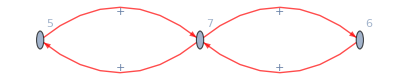
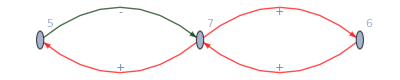
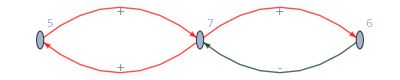
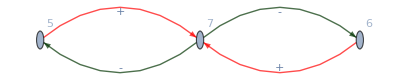
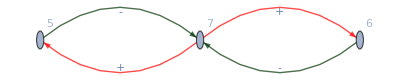
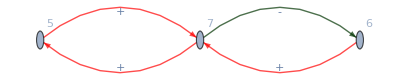
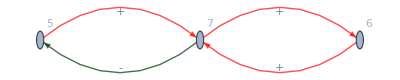
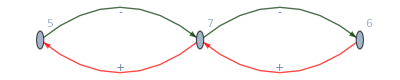
The function returns one representative of each equivalence class of all update schedules implicit to interaction digraph intG. Each representative is taken as the one with the minimal number of blocks in the class. 

Implementation notes:
1) All algorithms are from: J. Aracena, J. Demongeot, E.Fanchon and M. Montalva. “On the number of different dynamics in Boolean networks with deterministic update schedules”, Mathematical Biosciences 242(2):188-194, 2013.
2) The UDSReps function is equivalent to EqClass(G) from Algorithm 1 of the paper above.
3) UDSReps relies on the auxiliary functions DigraphUD, MoveVerticesQ, SameDigraphsQ and Subdigraph, all described below.

Examples of usage:
1) UDSReps[Graph[{5->7, 7->5, 7->6, 6->7}]]
{{{5, 6, 7}}, {{5}, {6, 7}}, {{6}, {5, 7}}, {{7}, {5, 6}}, {{5, 6}, {7}}, {{5, 7}, {6}}, {{6, 7}, {5}}, {{5}, {7}, {6}}, {{6}, {7}, {5}}}

2) Graphs of every update schedule in the previous example.
LabelledInteractionGraph[Graph[{5->7, 7->5, 7->6, 6->7}], #] & /@ UDSReps[Graph[{5->7, 7->5, 7->6, 6->7}]]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

3) Representatives of each update schedule class for a radius-1 CA running over a configuration of length 5. There are 181 independent update schedules.
UDSReps[] // Length  ⇒ 181

```mathematica
UDSReps[intG_Graph]:=
Module[{graphWeights=Flatten[Normal@WeightedAdjacencyMatrix[intG]]},
If[MemberQ[graphWeights,"+"]∨MemberQ[graphWeights,"-"],"Input has to be the interaction graph with no labels.",
DigraphUD[intG,{},{},Sort[VertexList[intG]]]]];
```

```mathematica
(*
DigraphUD: As described in Algorithm 2, the function...
*)
DigraphUD[G_Graph,UDS_List,A_List,B_List]:=
Module[{UD={},U=If[UDS≠{},Last[UDS],{}]},
If[U=={}&&A=={},
UD=Join[UD,{{B}}];
Table[UD=Union[UD,DigraphUD[G,{},x,Complement[B,x]]],{x,SortBy[Cases[Subsets[B],x_/;x≠{}&&x≠B],-Length[#]&]}];
,
If[!MoveVerticesQ[G,U,A],
If[!MoveVerticesQ[G,A,B],UD=Join[UD,{Join[UDS,{A},{B}]}]];
If[Length[B]>1,Table[UD=Union[UD,DigraphUD[G,Join[UDS,{A}],x,Complement[B,x]]],{x,SortBy[Cases[Subsets[B],x_/;x≠{}&&x≠B],-Length[#]&]}]
];
];
];
UD
];

(*
MoveVerticesQ: Predicate that returns True if it is possible to move vertices from D to C,without changing the update digraph induced by C∪D;otherwise,False is returned.This corresponds to Algorithm 3 in the paper.
*)
MoveVerticesQ[G_Graph,C_List,D_List]:=Module[{flag=If[D=={},True,False],subsets=SortBy[Cases[Subsets[D],x_/;x≠{}],-Length[#]&],i=1},
If[C=={},False,
While[!flag&&i≤Length[subsets],
If[SameDigraphsQ[Subdigraph[G,C,D],Subdigraph[G,Union[C,subsets⟦i⟧],Complement[D,subsets⟦i⟧]]],flag=True];
i++
];
flag
]
];

(*
 SameDigraphsQ: Given two digraphs,the predicate yields True if they have the same labeling.
*)
SameDigraphsQ[g1_Graph,g2_Graph]:=
With[{order1=Flatten[Ordering[EdgeList[g1]]],order2=Flatten[Ordering[EdgeList[g2]]]},
If[order1=={}||order2=={},If[order1=={}&&order2=={},True,False],If[(EdgeList[g1]⟦order1⟧==EdgeList[g2]⟦order2⟧)&&(Last[Last[AbsoluteOptions[g1,EdgeWeight]]]⟦order1⟧==Last[Last[AbsoluteOptions[g2,EdgeWeight]]]⟦order2⟧),True,False]]
];

(*
 Subdigraph: Gives the subdigraph generated from interaction digraph G and subsets C and D of vertices of G,as described in Definition 4.
Example of usage: Subdigraph[CAInteractionGraph[1,5], {1,3,5}, {2,4}]
*)
Subdigraph[intG_Graph,C_List,D_List]:=If[C=={}||D=={},If[C=={}&&D=={},Graph[{}],With[{elist=Sort[Intersection[EdgeList[intG],Flatten[Table[DirectedEdge[x,y],{x,Union[C,D]},{y,Union[C,D]}],1]]]},Graph[elist,EdgeWeight->Table["+",{Length[elist]}],EdgeLabels->"+",EdgeStyle->Red,VertexLabels->"Name"]]],With[{m=Table[Flatten[{x,If[MemberQ[C,First[x]]&&MemberQ[D,Last[x]],{"-",Darker[Green,0.8]},{"+",Red}]}],{x,Sort[Intersection[EdgeList[intG],Flatten[Table[DirectedEdge[x,y],{x,Union[C,D]},{y,Union[C,D]}],1]]]}]},
If[m≠{},Graph[Transpose[m]⟦1⟧,EdgeWeight->Transpose[m]⟦2⟧,EdgeLabels->MapThread[Rule,{Transpose[m]⟦1⟧,Transpose[m]⟦2⟧}],EdgeStyle->MapThread[Rule,{Transpose[m]⟦1⟧,Transpose[m]⟦3⟧}],VertexLabels->"Name"],Graph[{}]]]];
```

### [Serious bug here: not to be used yet!] The minimal block update schedule that yields a given labelled interaction digraph

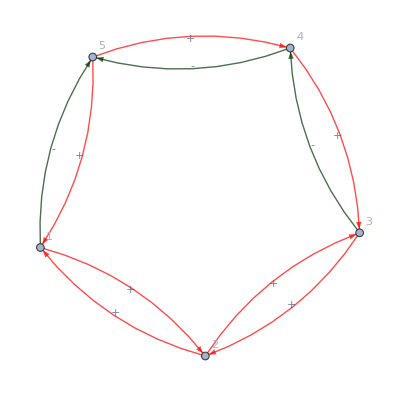
UDSFromLabIntGraph gives the minimal update schedule (in terms of the number of blocks in it) that generates the given labelled interaction digraph labG. It does so by sorting the vertices of labG using PriorityOrdering, and then computing the update priority of each cell. UDSfromPriorityList converts such a priority list to an update schedule.
Example of usage:
UDSFromLabIntGraph[-Graphics-]  ⇒  {{1, 2, 3}, {4}, {5}}

```mathematica
UDSFromLabIntGraph[labG_Graph]:=Module[{ordering=Sort[VertexList[labG],PriorityOrdering[labG,#1,#2]&],priority=1,prioritylist=Table[1,{VertexCount[labG]}]},
Table[
If[PriorityOrdering[labG,ordering⟦i⟧,ordering⟦i+1⟧]==1,priority=priority+1];
prioritylist⟦i+1⟧=priority;
,
{i,1,VertexCount[labG]-1}];
UDSFromPriorityList[prioritylist]
];
```

PriorityOrdering is an ordering function (as described in the documentation of the Sort function) for vertices in a labelled interaction digraph, in terms of their update priority. It uses RemovePositiveEdges and FindPath in order to verify whether or not there is a negative path from v1 to v2 or from v2 to v1: in the first case, v1 is updated before v2, whereas in the latter, v2 is updated before v1. If there are no negative paths connecting v1 and v2, both vertices have the same update priority. Summing up, these are the possible outputs of the function:
               1, if v1 is updated before v2
Output:   0, if v1 and v2 are updated at the same time
              -1, if v1 is updated after v2

```mathematica
PriorityOrdering[labG_Graph,v1_Integer,v2_Integer]:=If[FindPath[RemovePositiveEdges[labG],v1,v2]≠{},1,If[FindPath[RemovePositiveEdges[labG],v2,v1]≠{},-1,0]];
```

Given the labelled interaction digraph labG, the function RemovePositiveEdges prunes labG by removing its edges with positive labels. It is used in PriorityOrdering as an auxiliary function in order to establish whether or not a vertex v_i is updated before a vertex v_j.

```mathematica
RemovePositiveEdges[labG_Graph]:=
Module[{elist=EdgeList[labG],wlist=Last[Last[AbsoluteOptions[labG,EdgeWeight]]],vpos},
vpos=Flatten[Position[wlist,"-"]];
Graph[VertexList[labG],elist⟦vpos⟧,EdgeWeight->wlist⟦vpos⟧]
];
```

Given a list containing the update priorities of each of the n vertices in a labelled interaction digraph, the function yields the update schedule induced by prioritylist.
The i-th element of the list is the update priority of vertex i.

```mathematica
UDSFromPriorityList[prioritylist_List]:=Table[Sort[First[#]&/@x],{x,GatherBy[SortBy[MapThread[List,{Range[1,Length[prioritylist]],prioritylist}],Last],Last]}];
```

### Generation of interaction digraphs (labelled or not) for asynchronous CAs, and the labelled interaction digraph of an arbitrary (Boolean) network

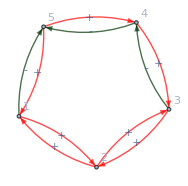
LabelledInteractionGraph (or the shorter version LabIntGraph) returns the labelled interaction digraph generated from (unlabelled) interaction digraph intG and update schedule UDS. In other words, it assigns the edges of intG with the labels “+” and “-” defined by the UDS.
The UDS must be written in block form; for instance, {{1, 2, 3}, {4}, {5, 6}} updates vertices 1, 2 and 3 first, at the same time, then vertex 4, and finally, vertices 5 and 6, simultaneously.
Example of usage: 
Labelled interaction digraph of an ECA rule running on a configuration of length 5 with update schedule {{1, 2, 3}, {4}, {5}}.
LabelledInteractionGraph[Graph[{1->2, 2->3, 3->4, 4->5, 5->1, 1->5, 5->4, 4->3, 3->2, 2->1}], {{1, 2, 3}, {4}, {5}}]
-Graphics-

```mathematica
LabelledInteractionGraph[intG_Graph,UDS_List]:=With[{m=Transpose@Table[If[Position[UDS,First[x]]⟦1,1⟧≥Position[UDS,Last[x]]⟦1,1⟧,{"+",Red},{"-",Darker[Green,.8]}],{x,Sort[EdgeList[intG]]}],elist=Sort[EdgeList[intG]]},Graph[elist,EdgeWeight->m⟦1⟧,EdgeStyle->MapThread[Rule,{elist,m⟦2⟧}],EdgeLabels->MapThread[Rule,{elist,m⟦1⟧}],EdgeLabelStyle->Larger,VertexLabels->"Name",VertexLabelStyle->Larger]];

LabIntGraph[intG_Graph,UDS_List]:=LabelledInteractionGraph[intG,UDS];
```

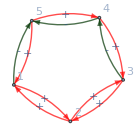
CALabelledInteractionGraph (or the shorter version CALabIntGraph) gives the labelled interaction digraph generated from the (unlabelled) interaction digraph of the r-radius CA rule running over a configuration of length configLen and update schedule UDS (written in block form). 
CAInteractionGraph (or the shorter version CAIntGraph) generates only the corresponding interaction graph.
Examples of usage: 
1) Labelled interaction digraph of an ECA rule running on a configuration of length 5, with a given update:
CALabelledInteractionGraph[1, 5, {{1, 2, 3}, {4}, {5}}]
-Graphics-
2) (Unlabelled) Interaction digraph of a CA rule of radius 1.5 running on a configuration of length 8, with no given update schedule:
CAInteractionGraph[1.5, 8]
-Graphics-

```mathematica
CALabelledInteractionGraph[r_:1,configLen_Integer,UDS_List]:=LabelledInteractionGraph[Graph[Flatten[Table[(First[x]->#)&/@Drop[x,1],{x,RotateLeft[#,⌈r⌉]&/@Partition[Range[1,configLen],IntegerPart[2*r+1],1,1]}]]],UDS];

CALabIntGraph[r_:1,configLen_Integer,UDS_List]:=CALabelledInteractionGraph[r,configLen,UDS];

CAInteractionGraph[r_:1,configLen_Integer]:=Graph[Flatten[Table[(First[x]->#)&/@Drop[x,1],{x,RotateLeft[#,⌈r⌉]&/@Partition[Range[1,configLen],IntegerPart[2*r+1],1,1]}]]];

CAIntGraph[r_:1,configLen_Integer]:=CAInteractionGraph[r,configLen];
```

### Generation of the weight adjacency matrix of a labelled interaction digraph

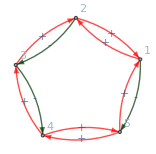
The native function WeightAdjacencyMatrix[labGraph] outputs the matrix according to the sequence of vertices given by VertexList[labGraph], which relies on how the graph has been originally constructed. For instance, in the example below, VertexList[labGraph] yields {1, 2, 5, 3, 4}, which means that the 3rd, 4th and 5th rows of the matrix correspond, respectively, to vertices 5, 3 and 4. But this is awkward, as it would be more direct that rows 3, 4 and 5 would correspond, respectively, to vertices 3, 4 and 5. WeightAdjacencyMatrixLabelledGraph makes this correction.

Example of usage: 
WeightAdjacencyMatrixLabelledGraph[-Graphics-]//MatrixForm
(0 | "+" | 0 | 0 | "-"
"+" | 0 | "-" | 0 | 0
0 | "+" | 0 | "-" | 0
0 | 0 | "+" | 0 | "+"
"+" | 0 | 0 | "+" | 0)

```mathematica
WeightAdjacencyMatrixLabelledGraph[labG_Graph]:=
Module[{orderedVertices},
orderedVertices=Range[1,Length[VertexList[labG]]];
Fold[
ReplacePart[#1,#2]&,
Normal@WeightedAdjacencyMatrix[labG],
MapThread[(#1->#2)&,
{Flatten[Outer[List[#1,#2]&,orderedVertices,orderedVertices],1]/.MapThread[Rule,{orderedVertices,VertexList[labG]}],Flatten[Take[Normal@WeightedAdjacencyMatrix[labG],{#⟦1⟧},{#⟦2⟧}]&/@Flatten[Outer[List[#1,#2]&,orderedVertices,orderedVertices],1]]}
]]];
```

### Time evolution of an arbitrary Boolean network with asynchronous block sequential update schedules

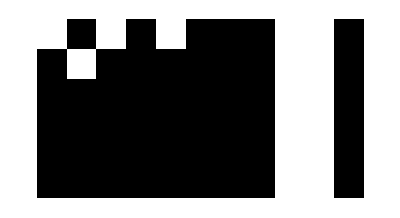
AsynchronousBN yields the time evolution of an arbitrary Boolean network, defined as a Mathematica graph object, via the specified asynchronous block sequential update. 

These are arguments of AsynchronousBN:

-- rulefunction: Any function f[self, slist] which receives the state of the vertex (self) as well as those of the neighbouring vertices (slist), and outputs a state. Notice that there is no “positional structure” in slist.
-- g: A directed graph that must be given in the form Graph[vertexlist, edgelist, EdgeWeight → edgeweights]. The vertexlist is used as a reference to the names of the vertices so as not to depend on their Mathematica ordering. Also, edgeweights is the list of states of each vertex, given according to the order they appear in vertexlist. The suggestion is to use vertexlist = Range[1, L].
-- tsteps: number of iterations.
-- UDS: Block sequential update schedule given as usual. For example, {{1,3}, {2,4,5}} means that vertices 1 and 3 are updated first, followed by the update of vertices 2, 4 and 5.
-- includeself: Whether or not to include the state of the vertex itself in slist described above.
-- returngraphs: If set to True, it will return the time evolution of the network as a list of graph objects. Otherwise, it returns only the states along the time evolution.
-- colours: Whether or not to colour the vertices according to colourfunction in the output.
-- colourfunction: How to color the vertices according to their states. The default function comprises binary states (White for 0 and Black for 1).

Implementation note: 
The same functionality could have been obtained by an implementation based on CASpatialComposition (which relies on CellularAutomaton); however, it would not operate on a graph object, as AsynchronousBN does.

Example of usage: 
Generation of a random binary IC and a graph with the same structure as an one-dimensional grid.

rand = RandomInteger[1, 11];
radius1examplegraph = Graph[Range[1,11], EdgeList[CAInteractionGraph[1,11]], VertexWeight→rand]

The time evolution of the Boolean network and of the equivalent CA:

AsynchronousBN[MajorityRuleBN, radius1examplegraph, 5, {{1,2,3}, {4,5,6}, {7,8,9}, {10,11}}, True, True, True, (If[#==1, Black, White]&)]
AsynchronousCA[{232,2,1}, rand, 5, {{1,2,3}, {4,5,6}, {7,8,9}, {10,11}}] // ArrayPlot

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
AsynchronousBN[rulefunction_,g_Graph,tsteps_Integer,UDS_List,includeself_Symbol:True,returngraphs_Symbol:True,colours_Symbol:True,colourfunction_:(If[#==1,Black,White]&)]:=
Module[{initialstatelist=AbsoluteOptions[g,VertexWeight]⟦1,2⟧,neighbourslist=If[includeself,Union[{#},VertexInNeighbours[g,#]]&/@VertexList[g],VertexInNeighbours[g,#]&/@VertexList[g]],timeevo=Table[-1,{tsteps+1},{Length[VertexList[g]]}]},
timeevo⟦1⟧=initialstatelist;
Do[timeevo⟦i⟧=timeevo⟦i-1⟧;
Do[timeevo⟦i,u⟧=rulefunction[timeevo⟦i,#⟧,timeevo⟦i⟧⟦neighbourslist⟦#⟧⟧]&/@u,
{u,UDS}],
{i,2,tsteps+1}];
If[¬returngraphs,
timeevo,
If[¬colours,
Graph[VertexList[g],EdgeList[g],VertexWeight->#]&/@timeevo,
Graph[VertexList[g],EdgeList[g],VertexWeight->#,VertexStyle->MapThread[Rule,{VertexList[g],Table[colourfunction[i],{i,#}]}]]&/@timeevo]]];

(*
Given a graph g and a vertex v, VertexInNeighbours gives the list of vertices u in g such that u -> v is an edge of v (that is, the list of "incoming" vertices).
*)

VertexInNeighbours[g_Graph,v_]:=First[#]&/@Cases[EdgeList[g],_->v];
```

### Further reduction of the set of representatives of all block sequential update schedule classes, when all configurations of a given length are considered and/or when taking into account symmetrical rules (only valid for CA type networks)

Examples of usage: 
Notice the reductions with respect to UDSReps:
{UDSReps[CAInteractionGraph[1,5]] // Length, UDSRepAllICs[CAInteractionGraph[1,5]] // Length}  ⇒  {181, 37}
{UDSReps[CAInteractionGraph[1,5]] // Length, UDSRepSymRules[CAInteractionGraph[1,5]] // Length}  ⇒  {181, 95}
{UDSReps[CAInteractionGraph[1,5]] // Length, UDSRepAllICsAndSymRules[CAInteractionGraph[1,5]] // Length}  ⇒  {181, 37}
Implementation note:
If required to access the entire class of equivalent update schedules, it suffices to drop the mapping of function First that appears in the beginning of each function body.

```mathematica
UDSRepsAllICs[intG_]:=
First/@GatherBy[UDSReps[intG],CanonicalRotationUDSForm[#]&];
```

```mathematica
UDSRepsSymRules[intG_]:=
First/@Union[Sort[{#,ReflectedUDS[#]}]&/@UDSReps[intG]];
```

```mathematica
UDSRepsAllICsAndSymRules[intG_]:=
First/@Union[Sort[{#,ReflectedUDS[#]}]&/@(First[#]&/@(Sort[#]&/@GatherBy[UDSReps[intG],CanonicalRotationUDSForm[#]&]))];
```

### Measures of the degree of asynchronism of a block sequential update schedule

Given the update schedule UDS, the function defines an asynchronism degree associated to every individual node of the corresponding labelled interaction digraph, and combines them in distinct fashions, so as to yield measures of the degree of asynchronism of the given UDS. Three possibilities are currently implemented, defined by the maximal, mean or total of the values of the individual nodes.

```mathematica
MaximalAsynchronismDegree[r_,UDS_List]:=
Max[VertexAsynchronismDegree[r,UDS]];

MeanAsynchronismDegree[r_,UDS_List]:=
Mean[VertexAsynchronismDegree[r,UDS]];

TotalAsynchronismDegree[r_,UDS_List,normalised_Symbol:False]:=
With[{len=Length[Flatten[UDS]],max=Total[VertexAsynchronismDegree[r,Partition[Range[1,Length[Flatten[UDS]]],1]]]},If[¬normalised,Total[VertexAsynchronismDegree[r,UDS]]-len,(Total[VertexAsynchronismDegree[r,UDS]]-len)/max]];

VertexAsynchronismDegree[r_,UDS_List]:=
Module[{depthlist=Table[If[MemberQ[First[UDS],i],1,0],{i,1,Length[Flatten[UDS]]}],len=Length[Flatten[UDS]],uds=UDS,aux},
uds=Drop[uds,1];
While[uds≠{},
aux=depthlist;
Table[aux⟦i⟧=1+Total[depthlist⟦GetNeighbours[Range[1,len],i,r]⟧],{i,First[uds]}];
depthlist=aux;
uds=Drop[uds,1];
];
depthlist
];
```

## 18. Asynchronous deterministic neighbourhood update schedules

### All possible independent asynchronous updates by neighbourhood priority

AllUdsNFromRule gives all independent UdsN lists (UdsN meaning Update schedule by Neighbourhood priority) for the given rule, leaving all inactive neighbourhoods with irrelevant update priority (i.e., the underscore symbol; see explanation of this in the description of function AsynchronousCAUdsN).

Examples of usage: 
AllUdsNFromRule[184, 2, 1]  ⇒  {{_,1,1,1,_,1,_,_}, {_,1,1,1,_,2,_,_}, {_,1,1,2,_,1,_,_}, ... , {_,4,3,1,_,2,_,_}, {_,4,3,2,_,1,_,_}}
% // Length  ⇒  75

Implementation notes:
1) A valid update must display all priorities from 1 to p, p ≤ k^(2r+1).
2) The notion of an independent update comes from two aspects: (1) A set of updates becomes the same when their inactive state transitions are replaced by the underscore; (2) Updates with the same priorities over all neighbourhoods are the same, the synchronous case.
3) The functions AllUdsNFromNTerms, UdsNFromSumList, SumsFromNTerms and SumsFromCharList are all auxiliary to AllUdsNFromRule.

```mathematica
AllUdsNFromRule[rnum_Integer,k_Integer:2,r_:1]:=
Module[{activenhspos=ActiveNeighbourhoodPositions[rnum,k,r],nhmax=IntegerPart[k^(2r+1)],aux,ans},
If[Length@activenhspos≠0,
If[Length@activenhspos≠nhmax,
aux=Table[AllUdsNFromNTerms[Length[activenhspos],i],{i,1,Length[activenhspos]}];
aux=Flatten[aux,1];
ans=Table[Table[_,{nhmax}],{Length[aux]}];
Table[ans⟦i,activenhspos⟦j⟧⟧=aux⟦i,j⟧,{i,1,Length[aux]},{j,1,Length@activenhspos}];
ans,
Flatten[Table[AllUdsNFromNTerms[Length[activenhspos],i],{i,1,Length[activenhspos]}],1]],
{Table[_,{nhmax}]}]];

(* 
AllUdsNFromNTerms yields all UdsN lists with terms distinct update priorities among a total number of neighbourhoods. 
Example: AllUdsNFromNTerms[4,2] yields all radius-0.5 (4 neighbourhoods) UdsN lists in which there are 2 distinct update priorities.More precisely,AllUdsNFromNTerms[4,2] yields {{1,1,1,2},{1,1,2,1},{1,1,2,2},{1,2,1,1},{1,2,1,2},{1,2,2,1},{1,2,2,2},{2,1,1,1},{2,1,1,2},{2,1,2,1},{2,1,2,2},{2,2,1,1},{2,2,1,2},{2,2,2,1}}. 
*)

AllUdsNFromNTerms[total_Integer,terms_Integer]:=
Sort[Flatten[UdsNFromSumList[#]&/@SumsFromNTerms[total,terms],1]]

(* 
UdsNFromSumList gives the update by neighbourhood priority induced bysumlist. 
Example: UdsNFromSumList[{3,1}] yields all the valid UdsN lists in which 3 neighbourhoods have priority 1 and 1 neighbourhood has priority 2. More precisely,UdsNFromSumList[{7,1}] yields {{1,1,1,2},{1,1,2,1},{1,2,1,1},{2,1,1,1}}. 
*)

UdsNFromSumList[sumlist_]:=
Permutations[Flatten[Table[Table[i,{sumlist⟦i⟧}],{i,1,Length[sumlist]}]]]

(* 
SumsFromNTerms gives the ways to obtain total by adding terms positive integer.
Example:SumsFromNTerms[4,2]={{3,1},{2,2},{1,3}} 
*)

SumsFromNTerms[total_Integer,terms_Integer]:=
If[total==terms,
{Table[1,{total}]},
If[terms==1,
{{total}},
(1+SumsFromCharList[#])&/@Permutations[Join[Table["*",{total-terms}],Table["|",{terms-1}]]]]];

(* SumsFromCharlist decodes a sequence of unities (“*”) and separators (“|”).  For instance,{“*”,”|”,”*”,”*”,”*”,”*”,”*”} represents one unity in the first variable and five unities in the second variable; thus SumsFromCharList yields {1,5}. This is an auxiliary function used in SumsFromNTerms below. 
*)


SumsFromCharList[charlist_List]:=
Module[{terms,sumlist,pos=1},
terms=1+Length[Cases[charlist,"|"]];
sumlist=Table[0,{terms}];
Table[If[charlist⟦i⟧=="*",sumlist⟦pos⟧=sumlist⟦pos⟧+1,pos=pos+1],{i,1,Length[charlist]}];
sumlist];
```

### Equivalent synchronous rule of any asynchronous rule with update by neighbourhood priority

FindUdsNCompositeRule gives the synchronous rule equivalent to applying the given rule asynchronously, according to the neighbourhood priorities in udsn. It uses four auxiliary functions, as listed below.

Example of usage:
FindUdsNCompositeRule[{184, 2, 1}, {_, 4, 3, 1, _, 2, _, _}]
{13401251411981641777428922396732228914681976960595095160900264105250873609824198848228495543004022124770843395298265375360968492197018576691326740409024512,2,4}

```mathematica
FindUdsNCompositeRule[{rnum_Integer,k_Integer:2,r_:1},udsn_List]:=With[{rule=CompositeRule[Reverse[{ActiveNeighbourhoodsToRNum[{rnum,k,r},#],r}&/@GetNeighbourhoodsProgression[{k,r},udsn]],k]},If[Length[rule]==2,{rule⟦1⟧,k,rule⟦2⟧},rule]];

(* 
ActiveNeighbourhoodsToRnum gives the resulting rule number from applying the given rule only to the neighbourhoods in neighbourhoodlist.
Example of usage:
ActiveNeighbourhoodsToRNum[{184,2,1},{{1,1,0},{1,1,1}}]  ⇒  140
*)

ActiveNeighbourhoodsToRNum[{rnum_Integer,k_Integer:2,r_:1},neighbourhoodlist_List]:=RnumFromRuleTable[If[MemberQ[neighbourhoodlist,#],{#,CellularAutomaton[{rnum,k,r},#]⟦⌈r⌉+1⟧},{#,#⟦⌈r⌉+1⟧}]&/@Tuples[Reverse[Range[0,k-1]],IntegerPart[2r+1]]];

(*
GetNeighbourhoodsProgression organises the k-ary neighbourhoods of radius r  according to their priorities, as defined in udsn.
Example of usage:
GetNeighbourhoodsProgression[{2,1},{_,3,3,1,_,2,_,_}]  ⇒  {{{1,0,0}},{{0,1,0}},{{1,1,0},{1,0,1}}}
*)

GetNeighbourhoodsProgression[{k_Integer:2,r_:1},udsn_List]:=
With[{M=Max[Select[udsn,NumberQ]]},GetNeighbourhoodsFromPriorities[{k,r},udsn,#]&/@Range[1,M]];

(* 
GetNeighbourhoodsFromPriorities gives the list of k-ary neighbourhoods of radius r  with the priorities, as defined in udsn.
Example of usage;
GetNeighbourhoodsFromPriorities[{2, 1}, {_, 3, 3, 1, _, 2, _, _}, 3]  ⇒ {{1,1,0}, {1,0,1}};
GetNeighbourhoodsFromPriorities[{2, 1}, {_, 3, 3, 1, _, 2, _, _}, {1, 3}] ⇒ {{{1,0,0}}, {{1,1,0},{1,0,1}}};
GetNeighbourhoodsFromPriorities[{2, 1}, {_, 3, 3, 1, _, 2, _, _}, {3, 1}] ⇒ {{{1,1,0},{1,0,1}}, {{1,0,0}}}
*)

GetNeighbourhoodsFromPriorities[{k_Integer,r_},udsn_List,priority_]:=With[{ans=Tuples[Reverse[Range[0,k-1]],IntegerPart[2r+1]]},If[IntegerQ[priority],ans⟦Flatten[Position[udsn,priority]]⟧,ans⟦Flatten[Position[udsn,#]]⟧&/@priority]];
```

## 19. Rule table properties

### Linearity (or Additivity)

Predicate that establishes whether the given k-colour, r-radius rule is linear or additive, in the sense that the rule can be expressed as a linear combination (modulo k) of the cell states in the neighbourhood (weighed by the possible k states). Formally: f(x_1, x_2, ..., x_n) = Mod[(s_1x_1+ s_2 x_2 + ... + s_⌈2r+1⌉x_⌈2r+1⌉), k] , s_i∈ {0, 1, ..., k-1}.

This definition is in tune with additivity on page 952 NKS and additivity or linearity in Ed Powley’s PhD Thesis. Therefore, it doesn’t correspond to the definitions of additivity and linearity in P. Pal Chaudhuri, D. Roy Chowdhury, S. Nandi, and S. Chatterjee. Additive Cellular Automata: Theory and Applications, VOL. 1. IEEE Computer Society Press, Los Alamitos, California, ISBN-0-8186-7717-1, 1997, nor to the definitions in Burt Voorhees. “Additive Cellular Automata”, In: R.A. Myers, editor. Encyclopedia of Complexity and Systems Science, pp.63-80, 2009 (by the way, additivity and linearity are individually defined in [Chaudhuri et. al, 1997] in exactly the opposite way of [Voorhees, 2009]).

Implementation note:
1) The linear algebraic expressions are given as in the following example:  S_-1+2 S_0+2 S_1.
2) The number of linear rules of a given space is k^⌊2r+1⌋.
3) LinearSolve is the core of LinearRuleAlgebraicRepresentation, since the given rule is assumed to be linear, that is, the only condition LinearSolve manages to find the target linear combination, which is returned as a vector; otherwise LinearSolve gives a beep to indicate an error.
4) A version of AllLinearRules could be implemented analogously to AllStrictlyLinearRules; this was carried out as a test, but the current version of AllLinearRules is way faster than that analogous version.

```mathematica
LinearRuleQ[rnum_Integer,k_Integer: 2,r_: 1]:=
If[Module[{neighbourhoods,outputs,variables,operatedVariables,equations},
{neighbourhoods,outputs}=Transpose[RuleTable[rnum,k,r]];
variables=MapThread[Subscript[#1,#2]&,{Table[x,{⌊2r+1⌋}],Range[-⌈r⌉,⌊r⌋,1]}];
operatedVariables=Total/@(MapThread[Times[#1,#2]&,{variables,#}]&/@neighbourhoods);
equations=And@@MapThread[(#1==#2)&,{operatedVariables,outputs}];
Solve[equations,variables,Modulus->k]]=={},False,True];
```

```mathematica
AllLinearRules[k_Integer: 2,r_: 1]:=
Sort[FromLinearAlgebraicRepresentationToRnum[#,k,r]&/@AllLinearAlgebraicRepresentations[k,r]];

FromLinearAlgebraicRepresentationToRnum[algebraicRep_,k_Integer: 2,r_: 1]:=
Module[{algebraicRepPieces,variablesInRep,variableCoefficientsInRep,neighbourhoods,outputs},
If[algebraicRep===0,0,
algebraicRepPieces=If[Head[#]===Subscript∨Head[#]===Times,List@#,List@@#]&[algebraicRep];
variablesInRep=If[Head[#]===Times,#⟦2,-1⟧,#⟦-1⟧]&/@algebraicRepPieces;
variablesInRep=variablesInRep+⌈r+1⌉;
variableCoefficientsInRep=If[Head[#]===Times,#⟦1⟧,1]&/@algebraicRepPieces;
neighbourhoods=Reverse@Tuples[Range[0,k-1],⌊2r+1⌋];
outputs=Mod[Total[#],k]&/@(Module[{neigh=#},MapThread[#1 neigh⟦#2⟧&,{variableCoefficientsInRep,variablesInRep}]]&/@neighbourhoods);
RnumFromRuleTable[Transpose[{neighbourhoods,outputs}],k]]];

AllLinearAlgebraicRepresentations[k_Integer: 2,r_: 1]:=
Module[{neighbourhoods,variables,equations},
neighbourhoods=Tuples[Range[0,k-1],⌊2r+1⌋];
variables=MapThread[Subscript[#1,#2]&,{Table[S,{⌊2r+1⌋}],Range[-⌈r⌉,⌊r⌋,1]}];
SortBy[Total/@(MapThread[Times[#1,#2]&,{variables,#}]&/@neighbourhoods),Depth[#]&]];
```

```mathematica
LinearRuleAlgebraicRepresentation[rnum_Integer,k_Integer: 2,r_: 1]:=
Total@MapThread[Times,{LinearRuleEqs[rnum,k,r],MapThread[Subscript[#1,#2]&,{Table[S,{⌊2r+1⌋}],Range[-⌈r⌉,⌊r⌋,1]}]}];

LinearRuleEqs[rnum_Integer,k_Integer: 2,r_: 1]:=
LinearSolve[#⟦1⟧,#⟦2⟧,Modulus->k]&[Transpose@RuleTable[rnum,k,r]];
```

```mathematica
AdditiveRuleQ[rnum_Integer,k_Integer: 2,r_: 1]:=LinearRuleQ[rnum,k,r];

AllAdditiveRules[k_Integer: 2,r_: 1]:=AllLinearRules[k,r];

FromAdditiveAlgebraicRepresentationToRnum[algebraicRep_,k_Integer: 2,r_: 1]:=FromLinearAlgebraicRepresentationToRnum[algebraicRep,k,r];

AllAdditiveAlgebraicRepresentations[k_Integer: 2,r_: 1]:=AllLinearAlgebraicRepresentations[k,r];

AdditiveRuleAlgebraicRepresentation[rnum_Integer,k_Integer: 2,r_: 1]:=LinearRuleAlgebraicRepresentation[rnum,k,r];
```

### Strict linearity

Predicate that establishes whether the given k-colour, r-radius one-dimensional rule is strictly linear, meaning that the rule can be expressed as a linear combination (modulo k) of the cell states in the neighbourhood (weighed by the possible k states) plus an independent state value. Formally: f(x_1, x_2, ..., x_n) = Mod[(s_1x_1+ s_2 x_2 + ... + s_⌈2r+1⌉x_⌈2r+1⌉ + s_(⌈2r⌉+2)), k] , s_i∈ {0, 1, ..., k-1}.

Implementation note:
The predicate relies on native Mathematica function Solve.

```mathematica
StrictlyLinearRuleQ[rnum_Integer,k_Integer: 2,r_: 1]:=
If[Module[{neighbourhoods,outputs,variables,operatedVariables,equations},
{neighbourhoods,outputs}=Transpose[RuleTable[rnum,k,r]];
variables=MapThread[Subscript[#1,#2]&,{Table[x,{⌊2r+1⌋}],Range[-⌈r⌉,⌊r⌋,1]}];
operatedVariables=Sequence@@{#+x}&/@(Total/@(MapThread[Times[#1,#2]&,{variables,#}]&/@neighbourhoods));
equations=And@@MapThread[(#1==#2)&,{operatedVariables,outputs}];
variables=Prepend[variables,x];
Solve[equations,variables,Modulus->k]]=={},False,True];
```

```mathematica
AllStrictlyLinearRules[k_Integer:2,r_:1]:=
Module[{coefficients,neighbourhoodsAndcoefficients,neighbourhoodsAndoutputs},
coefficients=Join[#⟦1⟧,{#⟦2⟧}]&/@Flatten[Outer[List,Tuples[Range[0,k-1],⌈2r+1⌉],Range[0,k-1],1],1];
neighbourhoodsAndcoefficients=Flatten[Outer[List,Tuples[Range[k-1,0,-1],⌈2r+1⌉],coefficients,1],1];
neighbourhoodsAndoutputs=Transpose@GatherBy[{#⟦1⟧,Mod[Total[Join[Table[Times[#⟦1,i⟧#⟦2,i⟧],{i,1,⌈2r+1⌉}],{#⟦2,-1⟧}]],k]}&/@neighbourhoodsAndcoefficients,First];
{#,k,r}&/@Sort[RnumFromRuleTable[#,k]&/@neighbourhoodsAndoutputs]];
```

### Quiescence

Predicate that establishes whether any homogeneous neighbourhood of the given k-colour, r-radius one-dimensional rule respects f(s, s, ..., s) = s,  s_i ∈ {0, 1, ..., k-1}.

```mathematica
QuiescentRuleQ[rnum_Integer,k_Integer:2,r_:1]:=
If[Union[Module[{indivQuiescentTransition},
(indivQuiescentTransition=#;
MemberQ[RuleTable[rnum,k,r],indivQuiescentTransition])]&/@({Table[#,{⌈2r 1+1⌉}],#}&/@Range[0,k-1])]=={True},True,False];

QuiescentRuleQ[{rnum_Integer,k_Integer:2,r_:1}]:=
QuiescentRuleQ[rnum,k,r];
```

### Symmetry Scoring (for k=2 only, as yet)

CountSymmetry does the actual counting of symmetry scores.
Example of usage:  
CountSymmetry[#, 2, 1, {stBWTransform, stLRTransform, stBWLRTransform}]& /@ {110, 137, 124, 193}

```mathematica
CountSymmetry[rnum_Integer,k_Integer:2,r_:1,fn_List]:= CountSymmetry[rnum,k,r,#]& /@ fn;
CountSymmetry[rnum_Integer,k_Integer:2,r_:1,fn_]:= Length[Intersection[fn /@ #,#]]& [RuleTable[rnum,k,r]];
```

### Colour Blindness

Colour blind CAs are those which are invariant to any permutation of the states; in other words, they are those with maximum conjugate symmetry. The concept was defined in V.O. Salo and I.A. Törmä. “Color blind cellular automata”. Journal of Cellular Automata, 9(5-6):477-509, 2014.

```mathematica
ColourBlindRuleQ[rnum_Integer,k_Integer:2,r_:1]:=
If[ConjugateRules[rnum,k,r]==={rnum},True,False];
```

### Typhlotic rules

Typhlotic CAs CAs are those which are invariant to any mapping of the states (they are, therefore, a subset of the blind colour CAs). The concept was defined in V.O. Salo and I.A. Törmä. “Color blind cellular automata”. Journal of Cellular Automata, 9(5-6):477-509, 2014.

```mathematica
TyphloticRuleQ[rnum_Integer,k_Integer:2,r_:1]:=
Module[{typhloticStateTransitions=SortBy[Union[Flatten[Transpose[TyphloticTransform[#,k,r]& /@ RuleTable[rnum,k,r]],1]],k-#⟦1⟧&]},
If[Length[typhloticStateTransitions]===k^⌊2r+1⌋∧RnumFromRuleTable[typhloticStateTransitions,k]===rnum,True,False]];

TyphloticTransform[statetransition_,k_Integer:2,r_:1]:= (statetransition /.#)&/@ AllSymbolMappings[k] ;

AllSymbolMappings[k_Integer:2]:=
MapThread[Thread[#1->#2]&,{Table[Range[0,k-1],{k^k}],Flatten[Outer[List,Sequence@@Table[Range[0,k-1],{i,0,k-1}]],k-1]}];
```

### Balancedness

A binary rule is balanced if the number of (output bit) 1s is the same as the number of 0s. Balancedness is normalised with respect to half of the number of possible neighbourhoods,  yielding values from 0 to 2, meaning, respectively, that, no output bit in the rule is 1, and all output bits in the rule are 1. A balanced rule thus has Balancedness=1.0, meaning that half of the output bits in the rule are 1. AbsoluteRuleBalance just provides a frequency of occurrence of each output state.
Implementation note: It only works for k=2. Maybe it can generalised. But the general definition of balancedness should be checked (it may be worth bearing in mind Corollary 2.2, of [Boccara & Fuks, 2002]).

```mathematica
BalancedQ[rnum_Integer,k_Integer:2,r_:1]:= If[Total[IntegerDigits[rnum,k,k^⌊2r+1⌋]]===k^⌊2r+1⌋/2,True,False];
```

```mathematica
Balancedness[rnum_Integer,k_Integer:2,r_:1]:=2 N[Total[IntegerDigits[rnum,k,k^⌊2r+1⌋]]/k^(2r+1)];
```

```mathematica
AbsoluteRuleBalance[rnum_Integer,k_Integer:2,r_:1]:=Tally[Last/@RuleTable[rnum,k,r]];
```

Works for any k. Check!!

```mathematica
GKBalancedQ[rnum_Integer,k_Integer:2,r_:1]:=If[Length[Cases[Count[IntegerDigits[rnum,k],#]&/@Range[1,k-1],Round[k^(2r+1)/k]]]===k -1 &&Count[IntegerDigits[rnum,k],0]≤ k^(2r+1)/k,True,False];
```

### Density Balancedness

This provides a measure of how balanced is a rule, in respect to the number of neighbourhoods with a certain (absolute) density of 1s that map to 1s (or, equivalently, the number of neighbourhoods with a certain (absolute) density of 0s that map to 0s).
Implementation note: It only works for k=2. Maybe it can be generalised.
Example of usage:
In: DensityBalancedness[337607298446901146542393000444934784552, 2, 3]
Out: {True, {1, 7, 15, 20, 20, 15, 7, 1}}
This means that, in that rule, there is exactly 1 neighbourhood with 7 ones mapping to one (or, equivalently, 1 neighbourhood with 7 zeros mapping to zero); there are exactly 7 neighbourhoods with 6 ones mapping to one (or, equivalently, 7 neighbourhoods with 6 zeros mapping to zero); and so on...

```mathematica
DensityBalancedness[rnum_Integer,k_Integer:2,r_:1]:=
{If[#⟦1⟧===#⟦2⟧,True,False]&[{#⟦1⟧,Reverse@#⟦2⟧}&[Partition[#,Length[#]/2]]],#}&[Flatten[{Count[#,1]&/@#⟦1⟧,Count[#,0]&/@#⟦2⟧}]&[((#⟦2⟧&/@#)&/@#)&/@(Partition[#,Length[#]/2]&[GatherBy[RuleTable[rnum,k,r],Count[#⟦1⟧,1]&]])]];
```

```mathematica
DensityBalancedQ[rnum_Integer,k_Integer:2,r_:1]:=First@DensityBalancedness[rnum,k,r];
```

### Conservation (Boccara-Fukš.b4 algorithm) and Conservation Degree

BFConservativeQ is a predicate that says whether rnum (radius r, k colours) is conservative, according to the algorithm described in N. Boccara and H. Fukš, “Number-conserving cellular automaton rules”, Fundamenta Informaticae 52:1-13, 2002.
BFConservativeQ derives from the simplification of BF's algorithm, due to [Schranko and de Oliveira, 2010], which states that it is tautological to check the state transitions f(0, x2, ..., xn), since they necessarily hold for any number-conserving CA; also, that if f(0, ..., 0) ≠ 0, the rule is not number conserving.
The second option for BFConservativeQ, that has the additional argument N, is a straightforward modification that allows checking whether a rule conserves the sum ModN of the states in the initial configuration (so, in particular, for binary rules and N=k=2, it checks whether the rule is parity preserving).
Notes:
1) The simplifications don’t make sense for working out the ConservationDegree. Do they really apply for the extension to ModN?
2) In fact, it is also true (from Corollary 2.1, of [Boccara & Fukš, 2002]) that, for any number-conserving rule, f(si, ..., si) = si for any state si. This should also be introduced in the function to speed up rejection of non-number-conserving rules.

```mathematica
BFConservativeQ[rnum_Integer,k_Integer:2,r_:1]:=
If[False===Catch[If[RuleOutputFromNeighbourhood[Table[0,{2r+1}],rnum,k,r]≠0,Throw[False],
If[RuleOutputFromNeighbourhood[#,rnum,k,r]≠ 
First[#]+∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{2,2r-i+2}]],rnum,k,r]-RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{1,2r-i+1}]],rnum,k,r]),Throw[False]]&/@ Cases[AllNeighbourhoods[k,r],{x_/;x≠0,___}]]],False,True];
```

```mathematica
BFConservativeQ[rnum_Integer,k_Integer:2,r_:1,N_Integer]:=
If[False===Catch[If[RuleOutputFromNeighbourhood[Table[0,{2r+1}],rnum,k,r]≠0,Throw[False],
If[Mod[RuleOutputFromNeighbourhood[#,rnum,k,r],N]≠ 
Mod[First[#]+∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{2,2r-i+2}]],rnum,k,r]-RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{1,2r-i+1}]],rnum,k,r]),N],Throw[False]]&/@ Cases[AllNeighbourhoods[k,r],{x_/;x≠0,___}]]],False,True];
```

The following yields the conservation degree of a rule, as defined in [Schranko & de Oliveira, 2010], but modified, in that the two become the same, by replacing the Union operation in Eqs. 13 and 14 with a MultisetUnion operation.
ConservationDegree is normalised with respect to the number of possible neighbourhoods, so that a conservative rule yields ConservationDegree=1, meaning that the test described in the algorithm holds true for all neighbourhoods.
Implementation note: 
1) Like the the definition in [Schranko & de Oliveira, 2010], ConservationDegree also conserves the parameter value across dynamically equivalent rules. But it has more granularity in the conservation degree values, entails more discrimination between the top 3000 rules of [Wolz & de Oliveira, 2008] and a sample of random radius 3 rules; and is much faster to run.
2) The granularity of the function for radius 1 is 14 values. I still have to work out this value in general.

```mathematica
ConservationDegree[rnum_Integer,k_Integer:2,r_:1]:=
Count[Flatten[{
RuleOutputFromNeighbourhood[#,rnum,k,r]== 
First[#]+∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{2,2r-i+2}]],rnum,k,r]-RuleOutputFromNeighbourhood[Join[Table[0,{i}],Take[#,{1,2r-i+1}]],rnum,k,r])
, (* Reflection *)
RuleOutputFromNeighbourhood[Reverse@#,rnum,k,r]== 
First[#]+∑_(i=1)^(2r) (RuleOutputFromNeighbourhood[Reverse@Join[Table[0,{i}],Take[#,{2,2r-i+2}]],rnum,k,r]-RuleOutputFromNeighbourhood[Reverse@Join[Table[0,{i}],Take[#,{1,2r-i+1}]],rnum,k,r])
, (* Conjugate *)
k-1-RuleOutputFromNeighbourhood[k-1-#,rnum,k,r]== 
First[#]+∑_(i=1)^(2r) ((k-1-RuleOutputFromNeighbourhood[k-1-Join[Table[0,{i}],Take[#,{2,2r-i+2}]],rnum,k,r])-(k-1-RuleOutputFromNeighbourhood[k-1-Join[Table[0,{i}],Take[#,{1,2r-i+1}]],rnum,k,r]))
,  (* Reflection∘Conjugate *)
k-1-RuleOutputFromNeighbourhood[Reverse[k-1-#],rnum,k,r]== 
First[#]+∑_(i=1)^(2r) ((k-1-RuleOutputFromNeighbourhood[Reverse[k-1-Join[Table[0,{i}],Take[#,{2,2r-i+2}]]],rnum,k,r])-(k-1-RuleOutputFromNeighbourhood[Reverse[k-1-Join[Table[0,{i}],Take[#,{1,2r-i+1}]]],rnum,k,r]))}
&/@ AllNeighbourhoods[k,r],1],True]/(4. k^(2r+1));
```

### Reversibility (OBS: There’s a bug in InverseRule, as in InverseRule[3915, 2, 1.5].)

Predicate that says whether rnum (radius r, k colour) is reversible. Adapted from the NKS book, page 1017. 
NB: All reversibility related functions should also work for Real-valed (multiple of 0.5) r-radius. 
Example of usage:
ReversibleRuleQ[3097483878567, 3, 1]  is  True

```mathematica
ReversibleRuleQ[rnum_Integer,k_Integer:2, r_:1]:=
Module[{maxlen=k^(2r)},
Catch[Do[If[Length[Union[Table[CellularAutomaton[{rnum,k,FlexRadius[r]},IntegerDigits[i,k,len]], {i,0,k^len-1}]]]≠k^len,Throw[False]],{len,maxlen}];True]];
```

Yields a reversibility measure of the r-radius, k-colour rnum rule, either as normalised value (default argument type "norm"), or as the absolute value (argument type "abs")
Implementation notes:
1) The algorithm is directly derived from the ReversibleRuleQ algorithm above, and relies on the idea of summing the actual values of  Length[etc] that is compared to k^len, instead of simply taking into account the number of True's that come out of the comparisons.
2) For k=2, the number of possible values for r=0.5 is 4, for r=1 is 17, and for r=1.5 is 331 (what's the general form?). With the proven upperbound maxlen =k^(2r)(k^(2r)-1)+2r+1 (see the NKS book, page 1017), a wider range of ReversibilityDegree values would be possible; however, this is not practical, since, for instance, k=2 r=2 would entail testing all initial configurations of length up to 245.
3) Non-reversible rules have ReversibilityDegree < ∑_(len=1)^maxlen k^len. But the ReversibleRuleQ predicate is faster to compute whether a rule is not reversible, since it usually does not go over all possible initial configurations.
4) Dyamically equivalent rules seem to yield the same ReversibilityDegree value.
5) No rule is totally non-reversible, the worst case being for rnum = 0.

```mathematica
ReversibilityDegree[rnum_Integer,k_Integer:2, r_:1,type_Symbol:norm]:=
Module[{maxlen=k^(2r)},
Switch[type,
norm,N[#/∑_(len=1)^maxlen k^len],
abs,#]&[Total[Reap[
Do[Sow@Length[Union[Table[CellularAutomaton[{rnum,k,FlexRadius[r]},IntegerDigits[i,k,len]], {i,0,k^len-1}]]],{len,1,maxlen}]]⟦2,1⟧]]];
```

Predicate that tells whether the k-colour rules rnum1 and rnum2, possibly with different radii (r1 and r2, respectively), are inverse to each other.
Example of usage:
InverseRulesQ[{3097483878567, 3, 1}, {3863160847143, 3, 1}]  yields  True
Implementation note:
The algorithm just compares the outcomes of the rules on a sufficiently long lattice, over a sufficiently high number of timesteps. The default values for length and timesteps have so far been sufficient, but I cannot guarantee they will remain so for any rule, which may entail an increase in their values.

```mathematica
InverseRulesQ[{rnum1_Integer,k_Integer:2,r1_:1},{rnum2_Integer,k_Integer:2,r2_:1},length_Integer:10000,timesteps_Integer:1000]:=Module[{forward=CellularAutomaton[{rnum1,k,FlexRadius[r1]},RandomInteger[{0,k-1},length],timesteps]},If[forward===Reverse[CellularAutomaton[{rnum2,k,FlexRadius[r2]},Last[forward],timesteps]],True,False]];
```

Yields the inverse rule (if any) of the given rnum, r-radius, k-colour reversible rule; the function returns the number of the inverse rule, followed by k and its radius, which, by the way, may be larger than that of the given rule (as happens in the 2nd example below). NB: This function hasn't been tested extensively; see the implementation notes below.
Example of usage:
InverseRule[3097483878567, 3, 1]  is  {3863160847143, 3, 1}
InverseRule[#, 2, 0.5]& /@ {3, 5, 10, 12} yields  {{85, 2, 1}, {5, 2, 0.5}, {10, 2, 0.5}, {170, 2, 1}}
Implementation notes:
1) This is an heuristic implementation, and, as such, it may yield an incorrect answer. Therefore, it is advisable to use InverseRulesQ for checking.
2) The core of the algorithm is based upon evolving the given rule for 1 timestep, over an initial configuration defined by a DeBruijn sequence. The idea is that this sequence might be smaller as a state sequence sample for the derivation of the inverse rule than the sample that would come out from a random sequence. I didn't check whether this is really true, but if this is correct, this algorithm should be faster than that with the randomly generated sequence. 
3) In case of incorrect answer, one possible workaround may be to increase the value of the 2nd argument of the BinaryDeBruijnSequence function. Currently, it's being assumed to be 2r+3, an heuristic value that has worked fine so far.
4) The other workaround is already accounted for in the code, which is the progressive increase of the radius of the inverse rule.

```mathematica
InverseRule[rnum_Integer,k_Integer:2, r_:1]:=
If[ReversibleRuleQ[rnum,k, r]===True,
Module[{neighbourhoods,outputs,transitions,rinv=r,smallrinv=True},
While[smallrinv==True,
{outputs,neighbourhoods}={#1,Join[Take[#2,-⌈rinv⌉],#2,Take[#2,⌊rinv⌋]]}&[Sequence@@CellularAutomaton[{rnum,k,FlexRadius[r]},DeBruijnSequence[k,⌊2r+1+2⌋],1]];
transitions=Union[{Take[neighbourhoods,{#,#+2rinv}],outputs⟦#⟧}&/@ Range[Length[outputs]]];
If[Length@Union[#⟦1⟧&/@transitions]==Length[#⟦1⟧&/@transitions]==k^(2rinv+1),smallrinv=False,rinv=0.5+rinv]];
{RnumFromRuleTable[Reverse@transitions,k],k,If[Floor[rinv]<rinv,rinv,Floor[rinv]]}],
"The given rule is not reversible."];
```

Partial reversibility classes (PRC) of the elementary space: under development...

```mathematica
(* OBS: OutputConjugateRule@NeighbourhoodConjugateRule == NeighbourhoodConjugateRule@OutputConjugateRule == BWEquivalent *)

NeighbourhoodConjugateTransform[statetransition_]:={statetransition⟦1⟧/.{1->0,0->1},statetransition⟦2⟧};
OutputConjugateTransform[statetransition_]:={statetransition⟦1⟧,1-statetransition⟦2⟧};

OutputConjugateRule[rnum_Integer,k_Integer:2,r_:1]:=RnumFromRuleTable[OutputConjugateTransform/@RuleTable[rnum,k,r],k];

NeighbourhoodConjugateRule[rnum_Integer,k_Integer:2,r_:1]:=RnumFromRuleTable[Reverse[NeighbourhoodConjugateTransform/@RuleTable[rnum,k,r]],k];

PRC[rnum_Integer,k_Integer: 2,r_: 1,type_Symbol: reps]:=
Switch[type,
reps,{rnum,First@Sort[DynamicalEquivalenceClass@NeighbourhoodConjugateRule[rnum,k,r]]},
full,Sort@Append[DynamicalEquivalenceClass@NeighbourhoodConjugateRule[rnum,k,r],rnum]];
```

### Totality

A rule is totalistic if the output of all state transitions depend only on the sum of the states in all cells of the neighbourhood.

```mathematica
TotalisticQ[rnum_Integer,k_Integer:2,r_:1]:=
If[{1}===Union[Length/@(Union/@GatherBy[{Total@First@#,Last[#]}&/@RuleTable[rnum,k,r],#⟦1⟧&])],True,False];
```

### Outer Totality

Outer totalistic rules are those that depend jointly on the state of the central cell and on the sum of the states in the remaining cells; in other words, they are totalistic in the neighbourhood, except for the central cell.
Implementation note: Although it is working for the elementary space, further tests are required for other values of k and r.

```mathematica
OuterTotalisticQ[rnum_Integer,k_Integer:2,r_:1]:=
If[{k}===Union[Length/@Union/@GatherBy[{{Total@Drop[First[#],{⌈r+1⌉}],#⟦1,⌈r+1⌉⟧},Last[#]}&/@RuleTable[rnum,k,r],#⟦1,1⟧&]],True,False];
```

### Captivity

Captive CA: for state set S and neighbourhood with n cells (i.e., (s_1,..., s_n), s_i∈ S), all state transitions must respect f(s_1,..., s_n) ∈ {s_1, ..., s_n}.

```mathematica
CaptiveQ[rnum_Integer,k_Integer:2,r_:1]:=If[MemberQ[MemberQ[#⟦1⟧,#⟦2⟧]&/@RuleTable[rnum,k,r],False],False,True];
```

### Multiset

A CA rule is said to be Multiset if, for state set S and neighbourhood with n cells (i.e., (s_1,..., s_n), s_i∈ S), all state transitions must respect f(s_1,..., s_n) =  f[Permutation(s_1, ..., s_n)]. For k=2, this equates to the rule being Totalistic, but, in general, Totalistic rules are a subset of the Multiset rules.

```mathematica
MultisetQ[rnum_Integer,k_Integer:2,r_:1]:= 
If[{1}===Union[Length[Union[#]]&/@((Last/@#)&/@GatherBy[RuleTable[rnum,k,r],Sort[#⟦1⟧]&])],True,False];
```

### Spreading State

Spreading state: for state set S and neighbourhood with n cells (i.e., (s_1, ..., s_n), s_i∈ S), s_s is a spreading state ⇔ f(s_1, ..., s_n) = s_s, when s_s∈ {s_1, ..., s_n} and f(s_1, ..., s_n) ≠ s_s, when s_s ∉ {s_1, ..., s_n}.
OBS: There can only exist a single spreading state, for any CA.
Spreading state CA: it’s the one that has a spreading state.

Examples of usage: 
SpreadingStateQ[128] => True
SpreadingStateQ[19485, 3, 0.5] => True

```mathematica
SpreadingStateQ[rnum_Integer,k_Integer:2,r_:1]:=
MemberQ[Module[{outState=#⟦2⟧},
{Union[MemberQ[#,outState]&/@#⟦1⟧],
Union[¬MemberQ[#,outState]&/@Complement[Tuples[Range[0,k-1],⌊2r+1⌋],#⟦1⟧]]}]&
/@RuleTablePartitioned[rnum,k,r],{{True},{True}}];

SpreadingState[rnum_Integer,k_Integer:2,r_:1]:=
Module[{pos=Position[Module[{outState=#⟦2⟧},
{
Union[MemberQ[#,outState]&/@#⟦1⟧],
Union[¬MemberQ[#,outState]&/@Complement[Tuples[Range[0,k-1],⌊2r+1⌋],#⟦1⟧]]
}]&/@Reverse@RuleTablePartitioned[rnum,k,r],{{True},{True}}]},
If[pos≠{},pos⟦1,1⟧-1,{}]];
```

### Permutiveness

The CA rule f: S^n → S with state set S is left-permutive, if for any s ∈ S and all (s_1, s_2, ..., s_(n-1)) S^(n-1), the map s ↦ f(s,s_1, s_2, ..., s_(n-1)) is a permutation of S. Analogously, the rule is right-permutive when the map is s ↦ f(s_1, s_2, ..., s_(n-1), s). The rule is bipermutive when it is both left- and right-permutive.

Examples of usage: 
In: Select[Range[0,255], PermutiveQ[#,2,1,left]&];
     GatherBy[%,Sort@DynamicalEquivalenceClass[#,2,1]&]
Out: {{15},{30,135},{45,75},{60,195},{90,165},{105},{120,225},{150},{180,210},{240}}

In: Select[Range[0,255], PermutiveQ[#,2,1,right]&];
     GatherBy[%,Sort@DynamicalEquivalenceClass[#,2,1]&]
Out: {{85},{86,149},{89,101},{90,165},{102,153},{105},{106,169},{150},{154,166},{170}}

In: Select[Range[0,255], BiPermutiveQ[#,2,1]&];
     GatherBy[%,Sort@DynamicalEquivalenceClass[#,2,1]&]
Out: {{90,165},{105},{150}}

```mathematica
BiPermutiveQ[rnum_Integer,k_Integer: 2,r_: 1]:=
If[PermutiveQ[rnum,k,r,left]∧PermutiveQ[rnum,k,r,right],True,False];

PermutiveQ[rnum_Integer,k_Integer: 2,r_: 1,direction_/;MemberQ[{left,right},direction]]:=
Module[{tuples,outputs,perms},
tuples=GatherBy[Tuples[Range[k-1,0,-1],⌈2r+1⌉],Switch[direction,left,Rest[#],right,Most[#]]&];
outputs=Sort/@Map[RuleOutputFromNeighbourhood[#,rnum,k,r]&,tuples,{2}];
perms=If[Range[0,k-1]==#,True,False]&/@outputs;
If[Union[perms]=={True},True,False]];
```

### Dynamical Behaviour

#### AAlpha

The parameter from: A. Schranko and P.P.B. de Oliveira. “Relationships between local dynamics and global reversibility of multidimensional cellular automata with hyper-rectangular neighbourhoods” (unpublished).
Example of usage:
Alpha[77, 2, 1] is 0.40625
Alpha[77, 2, {{0}, {1}, {2}}] is 0.40625
Alpha[6, 2, {{-1}, {0}}] is 0.25
Alpha[184, 2, {{-1}, {3}, {5}}] is 0.375
Implementation note: These are the implementations made by Angelo. Both versions are generalised, for any radius, the second one being general even for non-local neighbourhoods.

```mathematica
AAlpha[rnum_Integer, k_Integer:2, r_:1]:=N[Total[Union[Count[Take[#,{⌈r⌉+1,⌈r⌉+2r+1}]&/@(CellularAutomaton[{rnum,k,Table[{i}, {i,0,2r}]},#]&/@Tuples[Range[0,k-1],4r+1]), #]&/@ Tuples[Range[0,k-1],2r+1]]]/ k^(4r+1)];
```

```mathematica
AAlpha[rnum_Integer, k_Integer:2, neighbourhood_List]:=Module[{neighlen=Length[neighbourhood]},N[Total[Union[Count[Take[#,{⌈(neighlen-1)/2⌉+1,⌈(neighlen-1)/2⌉+neighlen}]&/@(CellularAutomaton[{rnum,k,neighbourhood},#]&/@Tuples[Range[0,k-1],4((neighlen-1)/2)+1]), #]&/@ Tuples[Range[0,k-1],neighlen]]]/ k^(4((neighlen-1)/2)+1)]];
```

#### Lambda

Chris Langton.b4s "temperature" or "activity" parameter.

```mathematica
Lambda[rnum_Integer,k_Integer:2,r_:1]:= Total[RuleTable[rnum,k,r]⟦All,2⟧];
```

```mathematica
LambdaNorm[rnum_Integer,k_Integer:2,r_:1]:= N[Lambda[rnum,k,r]/k^(2r + 1)];
```

#### Z

Andy Wuensche.b4s Z parameter, according to the formula presented in Classifying cellular automata automatically, Santa Fe Institute Working Paper 98-02-018, 1998 (with the correction I spotted that Rleft⟦kk-1⟧ and Rright⟦kk-1⟧ should be replaced, respectively, by Rleft⟦kk-i⟧ and Rright⟦kk-i⟧). Works for integer or fractional radius r. The function ZZ is just the output of {Z, Zleft, Zright}
Implementation note: Only works for k=2. For a correction, ZPatterns should be checked for whether Range[0, k-1] is general enough, for k>2.
Here are some rules for future test, with k=3:
r=1, k=3: 111021012100211002220210010
Zleft=0.518519, Zright=0.37037

ZZ[FromDigits[IntegerDigits[111021012100211002220210010],3],3,1]
{0.222222, 0.}

r=2, k=3: 122210020011020021201200110200211021102122200221011022010221100122122211012221202212011200120221110022222121221111012102202002010000120111100220020000220020002220212002012111210100000120022001110100011222122121002022222221212102011102120220210
Zleft=0.436214, Zright=0.465021

ZZ[FromDigits[IntegerDigits[122210020011020021201200110200211021102122200221011022010221100122122211012221202212011200120221110022222121221111012102202002010000120111100220020000220020002220212002012111210100000120022001110100011222122121002022222221212102011102120220210],3],3,2]
{0.0740741, 0.0740741}

```mathematica
NeighPatterns[k_Integer:2,r_:1]:=
(Join[#,Table[_,{2r+1-Length[#]}]]&/@#)&/@(AllNeighbourhoods[k,#]&/@Range[0,r,0.5]);
```

```mathematica
EquivNeighPatterns[k_Integer:2,r_:1]:=
Module[{i=#⟦1⟧},GatherBy[#⟦2⟧,Drop[#,{i}]&]]&/@MapThread[List,{Range[1,2r+1],NeighPatterns[k,r]}];
```

```mathematica
ZPatterns[k_Integer:2,r_:1]:=
Flatten[#,1]&/@(({MapThread[List,{#,Range[0,k-1]}],MapThread[List,{#,Reverse@Range[0,k-1]}]}&/@#)&/@EquivNeighPatterns[k,r]);
```

```mathematica
R[rnum_Integer,k_Integer:2,r_:1,dir_]:=
Total[Flatten[#]]/k^(2r+1)&/@MapThread[Module[{neighbsizeref=#1,rtableentriesofpattern=#2},If[Length[Flatten[#,1]]===neighbsizeref,neighbsizeref,0]&/@rtableentriesofpattern]&,{Table[⌈k^i⌉,{i,2r+1,1,-1}],((Cases[RuleTable[rnum,k,r],#]&/@#)&/@#)&/@Switch[dir,
left,ZPatterns[k,r],
right,(({Reverse[#⟦1⟧],#⟦2⟧}&/@#)&/@#)&/@ZPatterns[k,r]]}];
```

```mathematica
Z[rnum_Integer,k_Integer:2,r_:1]:=
Module[{Rleft=R[rnum,k,r,left], Rright=R[rnum,k,r,right], kk=2r+1,Zleft,Zright},
Zleft=N[Rleft⟦kk⟧+∑_(i=1)^(kk-1) (Rleft⟦kk-i⟧∏_(j=kk-i+1)^kk (1-Rleft⟦j⟧))];
Zright=N[Rright⟦kk⟧+∑_(i=1)^(kk-1) (Rright⟦kk-i⟧∏_(j=kk-i+1)^kk (1-Rright⟦j⟧))];
Max[Zleft,Zright]];
```

```mathematica
ZZ[rnum_Integer,k_Integer:2,r_:1]:=
Module[{Rleft=R[rnum,k,r,left], Rright=R[rnum,k,r,right], kk=2r+1,Zleft,Zright},
Zleft=N[Rleft⟦kk⟧+∑_(i=1)^(kk-1) (Rleft⟦kk-i⟧∏_(j=kk-i+1)^kk (1-Rleft⟦j⟧))];
Zright=N[Rright⟦kk⟧+∑_(i=1)^(kk-1) (Rright⟦kk-i⟧∏_(j=kk-i+1)^kk (1-Rright⟦j⟧))];
{Max[Zleft,Zright],Zleft,Zright}];
```

#### Sensitivity

Implementation Note: Does not work for k>2, because BooleanDerivative uses Flip, which is not defined for k>2. Requires generalisation.

```mathematica
Sensitivity[rnum_Integer,k_Integer:2,r_:1]:= 
Total[∑_(pos=1)^(2r+1) BooleanDerivative[#,pos,rnum,k,r]&  /@ RuleTable[rnum,k,r]];
```

```mathematica
SensitivityNorm[rnum_Integer,k_Integer:2,r_:1]:= N[Sensitivity[rnum,k,r]/(k^(2r + 1) (2r+1))];
```

#### Neighbourhood Dominance

```mathematica
NDominance[rnum_Integer,k_Integer:2,r_:1]:=Total[Binomial[2r+1, Total[#⟦1⟧]+(r+1)]If[Total[#⟦1⟧]<(r+1) ∧ RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]==0, 1,0]&  /@ RuleTable[rnum,k,r]] + Total[Binomial[2r+1, Total[#⟦1⟧]-(r+1)]If[Total[#⟦1⟧]≥(r+1) ∧ RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]==1, 1,0]& /@ RuleTable[rnum,k,r]];
```

```mathematica
NDominanceNorm[rnum_Integer,k_Integer:2,r_:1]:= N[NDominance[rnum,k,r]/(2∑_(pos=0)^r Binomial[2r+1,pos]Binomial[2r+1,pos+r+1])];
```

#### Absolute Activity

```mathematica
AbsoluteActivity[rnum_Integer,k_Integer:2,r_:1]:=Total[If[RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]≠#⟦1,r+1⟧, 1, 0] +∑_(pos=1)^r If[RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]≠#⟦1,pos⟧ ∨ RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]≠#⟦1,2r+2-pos⟧, 1, 0]&
/@ RuleTable[rnum,k,r]];
```

```mathematica
AbsoluteActivityNorm[rnum_Integer,k_Integer:2,r_:1]:= 
Module[{AAmin,AAmax},
AAmin =Total[Min[∑_(pos=1)^(r+1) If[#⟦1,pos⟧==0 ∨ #⟦1,2r+2-pos⟧==0, 1, 0],∑_(pos=1)^(r+1) If[#⟦1,pos⟧==1 ∨ #⟦1,2r+2-pos⟧==1, 1, 0]]&  /@ RuleTable[rnum,k,r]];
AAmax = Total[Max[∑_(pos=1)^(r+1) If[#⟦1,pos⟧==0 ∨ #⟦1,2r+2-pos⟧==0, 1, 0],∑_(pos=1)^(r+1) If[#⟦1,pos⟧==1 ∨ #⟦1,2r+2-pos⟧==1, 1, 0]]&  /@ RuleTable[rnum,k,r]];
N[(AbsoluteActivity[rnum,k,r]-AAmin)/(AAmax - AAmin)]];
```

#### Activity Propagation

Implementation Note: Does not work for k>2, because BooleanDerivative uses Flip, which is not defined for k>2. Requires generalisation.

```mathematica
ActivityPropagation[rnum_Integer,k_Integer:2,r_:1]:=Total[∑_(pos=1)^(2r+1) If[(Total[#⟦1⟧]<(r+1) ∧ RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]==1 ∨ Total[#⟦1⟧]≥(r+1) ∧ RuleOutputFromNeighbourhood[#⟦1⟧,rnum,k,r]==0) ∧ ((Total[#⟦1⟧]-2#⟦1,pos⟧<r ∧ RuleOutputFromNeighbourhood[Flip[#⟦1⟧,pos],rnum,k,r]==1) ∨  (Total[#⟦1⟧]-2#⟦1,pos⟧≥r ∧ RuleOutputFromNeighbourhood[Flip[#⟦1⟧,pos],rnum,k,r]==0)),1,0]&  /@ RuleTable[rnum,k,r]];
```

```mathematica
ActivityPropagationNorm[rnum_Integer,k_Integer:2,r_:1]:= N[ActivityPropagation[rnum,k,r]/(k^(2r + 1) (2r+1))];
```

#### Wentian Li.b4s Z

```mathematica
Zwl[rnum_Integer,k_Integer:2,r_:1]:= 
Max[Total[∑_(pos=1)^r BooleanDerivative[#,pos, rnum,r,k]&  /@ RuleTable[rnum,k,r]]/2,
Total[∑_(pos=r+2)^(2r+1) BooleanDerivative[#,pos, rnum,r,k]&  /@ RuleTable[rnum,k,r]]/2];
```

```mathematica
ZwlNorm[rnum_Integer,k_Integer:2,r_:1]:= N[Zwl[rnum,k,r]/(k^r(2r))];
```

### Boolean representation of a (one-dimensional) binary rule

#### DNF with lists of bits and don’t-cares

Boolean minimisation of a binary cellular automaton rule, with the result given in Disjunctive Normal Form. The option stateRef allows to select the set of state transitions that should be taken into account for minimisation: if it’s simply a state (as, by default 1), only the state transitions leading to it are minimised; it it’s a list, either {0,1} or {1,0}, then all active state transitions from 0 to 1 or from 1 to 0, respectively, are considered. 
Since the function relies upon the native Mathematica function BooleanMinimize, which only yields a single result, out of others generally possible, RuleMinDNF also has the same restriction.
It works by converting the binary format into the Boolean format (based on Boolean variables) required by BooleanMinimize, which is the real responsible for the minimisation. After that, VarsToBits converts the Boolean format back to the binary format.
Examples of usage:
RuleMinDNF[{254, 1}, 1]  ==> {{1, _, _}, {_, 1, _}, {_, _, 1}}
RuleMinDNF[{254, 1}, 0]  ==> {{0, 0, 0}}
RuleMinDNF[{254, 1}, {0,1}]  ==> {{1, 0, _}, {_, 0, 1}}
RuleMinDNF[{254, 1}, {1,0}]  ==> {}

```mathematica
RuleMinDNF[{rnum_Integer,r_:1},stateRef_:1]:=
If[stateRef==={},"Option {} makes no sense and therefore is invalid!",
Module[{k=2,vars=Symbol/@(FromCharacterCode[96+#]&/@Range[⌊2r+1⌋])},
VarsToBits[
BooleanMinimize[
Or@@((And@@#)&/@
(Table[Switch[#⟦I⟧,
0,¬vars⟦I⟧,
1,vars⟦I⟧],{I,1,Length@vars}]&/@
(#⟦1⟧&/@
If[¬ListQ[stateRef],
Select[RuleTable[rnum,k,r],(#⟦2⟧===stateRef)&],
ActiveStateTransitions[{rnum,k,r},stateRef]])))],r]]];
```

VarsToBits converts the Boolean format back to the binary format (for additional clarification, refer to comments written above for RuleMinDNF). The following examples represent all (hopefully!) possibilities that had to be accounted for:
RuleMinDNF[{0, 1}] ==> False
RuleMinDNF[{1, 1}] ==> ! a && ! b && ! c
RuleMinDNF[{15, 1}] ==> ! a
RuleMinDNF[{85, 1}] ==> a
RuleMinDNF[{184, 1}] ==> (a && ! b) || (b && c)
RuleMinDNF[{254, 1}] ==> a || b || c
RuleMinDNF[{255, 1}] ==> True

```mathematica
VarsToBits[booleanExp_,r_:1]:=
Switch[booleanExp,
True,{Table[_,{⌊2r+1⌋}]},
False,{},
_,
Module[{k=2,vars=Symbol/@(FromCharacterCode[96+#]&/@Range[⌊2r+1⌋]),instantiatedPart,uninstantiatedPart},
Switch[Head[booleanExp],
Or,
instantiatedPart=If[Head[#]===And,Apply[List,#],#]& /@(Apply[List,booleanExp]/.Join[(#->(¬#)[0])&/@(Not/@vars),(#->#[1])&/@vars]);
uninstantiatedPart=(#[_]&/@#)&/@Apply[List,Complement[vars,BooleanVariables[#]]&/@booleanExp],
And,
instantiatedPart=Apply[List,#]& /@(List[booleanExp]/.Join[(#->(¬#)[0])&/@(Not/@vars),(#->#[1])&/@vars]);
uninstantiatedPart=(#[_]&/@#)&/@Apply[List,{Complement[vars,BooleanVariables[booleanExp]]}],
x_/;MemberQ[{Symbol,Not},x],
instantiatedPart=List[booleanExp]/.Join[(#->(¬#)[0])&/@(Not/@vars),(#->#[1])&/@vars];
uninstantiatedPart=(#[_]&/@#)&/@Apply[List,{Complement[vars,BooleanVariables[booleanExp]]}]];
(First@Level[#,1]&/@#)&/@(Union@Flatten[#,1]&/@MapThread[List,{instantiatedPart,uninstantiatedPart}])]];
```

Checks whether the minimisation is really working. It just checks whether the given rule rnum can be minimised and regenerated back. Just like in MinimisedFormToRnum, it only makes sense here to have stateRef as a direct state, not a list.

```mathematica
RuleMinimisationCorrectQ[{rnum_Integer,r_:1},stateRef_:1]:=
If[ListQ[stateRef],"It makes no sense to have a list as an option and therefore it is invalid!",MinimisedFormToRnum[RuleMinDNF[{rnum,r},stateRef],stateRef,r]===rnum];
```

Used only by RuleMinimisationCorrectQ. This function is the reverse of RuleMinDNF: yields the rule number represented by minimisedForm. Here, it only makes sense to have stateRef as a direct state, not a list.

```mathematica
MinimisedFormToRnum[minimisedForm_List,stateRef_:1,r_:1]:=
If[ListQ[stateRef],"It makes no sense to have a list as an option and therefore it is invalid!",
Module[{k=2,tuplesToOne,tuplesToZero,allTuples,allSTs},
allTuples=Tuples[{0,1},⌈2r+1⌉];
Switch[stateRef,
1,
tuplesToOne=Union[Flatten[Cases[allTuples,#]&/@minimisedForm,1]];
tuplesToZero=Complement[allTuples,tuplesToOne],
0,
tuplesToZero=Union[Flatten[Cases[allTuples,#]&/@minimisedForm,1]];
tuplesToOne=Complement[allTuples,tuplesToZero]];
allSTs=Reverse@Union[Join[{#,1}&/@tuplesToOne,{#,0}&/@tuplesToZero]];
RnumFromRuleTable[allSTs,k]]];
```

#### Full Boolean form (in ANF and in DNF)

RuleMinDNF and RuleMinANF are analogous to the previous (bit and don’t-care list) form, but the output is generated as a real Boolean expression in DNF or in ANF (although only for stateRef=1). This has been done to replicate the table on pages 516-521, of “Tables of Cellular Automaton Properties”, in https://content.wolfram.com/uploads/sites/34/2020/07/cellular-automaton-properties.pdf, which is in DNF. DNF is the Boolean “Disjunctive Normal Form”, whereas ANF is the Boolean “Algebraic Normal Form”.
Examples of usage:
RuleMinDNF[254, 1]  ==> x_-1||x_0||x_1 
RuleMinDNF[150, 1]  ==>(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)
RuleMinANF[254, 1]  ==> (x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1 
RuleMinANF[150, 1]  ==>(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)
Implementation notes: 
1) The symbol ⊻ that appears in ANF represents the XOR operation.
2) Notice that the name RuleMinDNF is the same as the one defined earlier, but not the format of its arguments. Notice also that it relied on the original RuleMinDNF[{rnum,r},1].
3) The native function BooleanConvert can be used to convert the output to various other Boolean forms. But there seems to be a problem with BooleanConvert, as I noticed in the following conversion: BooleanConvert[RuleMinDNF[150], “ESOP”] , which should be (x_-1⊻ x_0⊻ x_1), but is not what comes out of the conversion.

```mathematica
RuleMinDNF[rnum_Integer,r_:1]:=
Module[{ruleMinDNFwithVariables=MapThread[Switch[#3,0,#2,1,#1,_,_]&,{Subscript[x,#]&/@CellIndices[r],Subscript[¬x,#]&/@CellIndices[r],#}]&/@RuleMinDNF[{rnum,r},1]},
Or@@(Apply[And,#]&/@ (Select[#,(Head@#==Subscript∨Head@#==Not)&]&/@ruleMinDNFwithVariables))];

RuleMinANF[rnum_Integer,r_:1]:=
Module[{xVariables=MapThread[Subscript[#1,#2]&,{Table[x,{⌈2r+1⌉}],CellIndices[r]}]},
(BooleanConvert[BooleanFunction[rnum,⌈2r+1⌉],"ANF"])[Sequence@@xVariables]];

CellIndices[r_:1]:=
Module[{raux=If[⌊r⌋<r,r,⌊r⌋]},
Flatten@If[¬IntegerQ[raux],List/@Range[-⌈r⌉,⌊r⌋],List/@Range[-⌊r⌋,r]]];
```

### Algebraic representation of a (one-dimensional) binary rule

It takes the full Boolean representation of the rule, either the outcome of functions RuleMinDNF or RuleMinANF above), and turns it into an algebraic representation. 
Notice that ANF2AlgebraicForm[RuleMinANF[rnum, r]] leads to more compact expressions than DNF2AlgebraicForm[RuleMinDNF[rnum, r]].
Examples of usage:
In:  DNF2AlgebraicForm[RuleMinDNF[150]]
Out:  Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]
In: ANF2AlgebraicForm[RuleMinANF[150]]
Out: x_-1+x_0+x_1
Implementation note: 
The algebraic expressions in http://atlas.wolfram.com/01/01/views/173/TableView.html is essentially those obtained with ANF2AlgebraicForm[RuleMinANF[rnum, 1]].

```mathematica
AlgebraicRepresentation[rnum_Integer,r_:1,form_Symbol]:=
Switch[form,
DNF,DNF2AlgebraicForm[RuleMinDNF[rnum,r]],
ANF,ANF2AlgebraicForm[RuleMinANF[rnum,r]]];
```

```mathematica
DNF2AlgebraicForm[dnfForm_]:=
If[MemberQ[{True,False},dnfForm],dnfForm,Mod[dnfForm/.{Or->Plus,And->Times,¬x_->(1-x)},2]];
```

```mathematica
ANF2AlgebraicForm[anfForm_]:=
FullSimplify[Fold[ReplaceAll[#1,#2]&,anfForm,{{And-> Times},{Xor->Plus},{¬x_->(1+x)}}]];
```

## 20. Rule analyses

### Comparison between Rule Tables

Checks how each k-ary ouput representing a k-colour, r-radius rule number rnum compares to the corresponding k-ary output from rule number rnumref. When the compaired outputs are the same, the number identifying the neighbourhood at issue (its position) is returned associated to the output value; otherwise, it is returned associated to the symbol x. With the default nonclassified type, the neighbourhood identifiers are returned in decreasing order, from (k^(2r+1)-1) down to 0; otherwise (i.e., with the classified type), the neighbourhood identifiers are sorted in classes of the number of 1s involved in the neighbourhood, and each class is interspersed by the dummy separator pair {_, s}. Within each class (delimited by the separators), the neighbourhood identifiers are sorted in decreasing order of their values.
Examples of usage:
RnumComparison[150, MajorityRule[1], 2, 1, nonclassified]		Out: {{7, 1}, {6, x}, {5, x}, {4, x}, {3, x}, {2, x}, {1, x}, {0, 0}}
RnumComparison[150, MajorityRule[1], 2, 1, classified]		Out:  {{7, 1}, {_, s}, {6, x}, {5, x}, {3, x}, {_, s}, {4, x}, {2, x}, {1, x}, {_, s}, {0, 0}}
Implementation note: The implementation is currently biased for k=2. That is why the classification is made in terms of the number of 1s, instead of the number of an arbitrary colour.

```mathematica
RnumComparison[rnum_Integer,rnumref_Integer,k_Integer:2,r_:1,type_:nonclassified]:=
Switch[type,
nonclassified,
If[#⟦2⟧===#⟦3⟧,{#⟦1⟧,#⟦2⟧},{#⟦1⟧,x}]&/@MapThread[List,{Range[k^(2r+1)-1,0,-1],IntegerDigits[rnum,k,k^⌊2r+1⌋],IntegerDigits[rnumref,k,k^⌊2r+1⌋]}],
classified,Most@Flatten[MapThread[List,{GatherBy[RnumComparison[rnum,rnumref,k,r,nonclassified],Count[IntegerDigits[#⟦1⟧,k,⌊2r+1⌋],1]&],Table[{{_,s}},{2r+2}]}],2]];
```

Displays the comparison between the k-ary ouput representing a k-colour, r-radius rule number rnum compares to the corresponding k-ary output from rule number rnumref. Colour map utilised: black for common output 1; white for common output 0; red for distinct outputs; and yellow for the dummy separator pair {_, s}.
Examples of usage: 
DisplayRnumComparison[{150}, MajorityRule[1], 2, 1, classified]
DisplayRnumComparison[150, MajorityRule[1], 2, 1, classified]
Implementation note: The colour map is currently accounting only for k=2.

```mathematica
DisplayRnumComparison[rnumlist_List,rnumref_Integer,k_Integer:2,r_:1,type_:nonclassified]:=ArrayPlot[((#1⟦2⟧&)/@#1&)/@(RnumComparison[#1,rnumref,k,r,type]&)/@rnumlist,Mesh->True,ColorRules->{0->White,1->Black,x->Red,s->Yellow}]

DisplayRnumComparison[rnumlist_Integer,rnumref_Integer,k_Integer:2,r_:1,type_:nonclassified]:=DisplayRnumComparison[{rnumlist},rnumref,k,r,type];
```

### Hamming Distance between Binary Rule Tables

Yields the Hamming distance between 2 rule numbers with 2 colours and any radius.

```mathematica
RuleHammingDistance[rnum1_Integer,rnum2_Integer]:=
Total[IntegerDigits[BitXor[rnum1,rnum2],2]];
```

### Various Analyses between Rule Tables

Argument rnumdata can be either a list of rule numbers, or a list of pairs of the type {rnum, evaluation}, where evaluation refers to the efficacy of rnum in some task (say, DCT).

```mathematica
AnalyseRules[rnumdata_List,k_Integer:2,r_:1]:=
If[Depth@rnumdata===2,
{{Rule,Bal,DensBal,BFCons,DistToMaj,Sensit,NeighbDom,AbsAct,ActProp,BW,LR,BWLR,EqClassLen},Sequence@@({#,Balancedness[#,k,r],DensityBalancedness[#,k,r],BFConservationDegree[#,k,r],RuleHammingDistance[#,MajorityRule[r]],SensitivityNorm[#,k,r],NDominanceNorm[#,k,r],AbsoluteActivityNorm[#,k,r],ActivityPropagationNorm[#,k,r],Sequence@@CountSymmetry[#,k,r,{stBWTransform,stLRTransform,stBWLRTransform}],Length@DynamicalEquivalenceClass[#,k,r]}&/@rnumdata)},
{{Rule,Eval,Bal,DensBal,BFCons,DistToMaj,Sensit,NeighbDom,AbsAct,ActProp,BW,LR,BWLR,EqClassLen},Sequence@@({#⟦1⟧,#⟦2⟧,Balancedness[#⟦1⟧,k,r],DensityBalancedness[#⟦1⟧,k,r],BFConservationDegree[#⟦1⟧,k,r],RuleHammingDistance[#⟦1⟧,MajorityRule[r]],SensitivityNorm[#⟦1⟧,k,r],NDominanceNorm[#⟦1⟧,k,r],AbsoluteActivityNorm[#⟦1⟧,k,r],ActivityPropagationNorm[#⟦1⟧,k,r],Sequence@@CountSymmetry[#⟦1⟧,k,r,{stBWTransform,stLRTransform,stBWLRTransform}],Length@DynamicalEquivalenceClass[#⟦1⟧,k,r]}&/@rnumdata)}];
```

### Rule Sorting According to their Parameter Values

Returns a list of all k-colour, r-radius rules referred to in the argument rulespec, that share the same values of the parameters specified in the pars list. By default, rulespec refers to the entire space at issue, in which case the results are given in terms of the representatives of each class of dynamical behaviour (instead of in terms of each and every individual rule of the space). However, rulespec can also be given as a list of specific rule numbers of the space at issue. With the default value output = sorted, the returned list is sorted; the unsorted option can be set by output = unsorted.  
The pars list may include a parameter name only, a condition that is valid only for parameters whose arguments have the form [rnum, k, r]. Otherwise, the general case should be used, in which the parameter may have any other type or quantity of arguments, with the only constraint being that the rule number field in the parameter specification be filled in by the slot # symbol, and that the & symbol be appended to the parameter specification (as happens in SortPars[{Alpha[#, 2, 1, 2]&}]).  
Note: It is reccomended to append the command with // MatrixForm, so as to obtain an organised display of the results.
Examples of usage:
SortPars[{Alpha, Z}] and SortPars[{Alpha, Z}, 2, 1] are equivalent forms that sort all rules of the elementary space in terms of those that share the same values of Alpha and Z, organised from the smallest to the highest values of Alpha and Z, respectively.  
SortPars[{Z}, 2, 1] or SortPars[{Z}] both yield the dynamical classes of the ECA space, according to the Z values of the rules from each class.  
SortPars[{Alpha, Alpha[#, 2, 1, 2]&, Alpha[#, 2, 1, 3]&}] sorts the entire ECA space according to the values of Alpha of 1st, 2nd and 3 order, respectively. 
Implementation notes: 
1) The sorting of the rules is given according to the parameter sequence specified in the pars list. Therefore, SortPars[{Alpha, Z}] yields a different display of the sorted ECA space from SortPars[{Z, Alpha}].
2) The redundancy for k and r in  SortPars[{Alpha[#, 2, 0.5, 2]&}, 2, 0.5] is not elegant and would rather be ammended.
3) The code List[#1, If[Depth[#2] === 2, #2, #2⟦1⟧]]&  is required for generality of the function, so that it can also account for parameters that are defined in terms of a list of values (e.g., CyclicPreimagePattern), instead of a single value (e.g., Z).

```mathematica
SetAttributes[SortPars,HoldFirst];
SortPars[pars_List,k_Integer:2, r_:1, rulespec_:All,output_Symbol:sorted]:=
Module[{rules,rulesandpars},
rules=If[rulespec===All,First[#]&/@AllEquivalenceRuleClasses[k,r],rulespec];
rulesandpars=MapThread[List[#1,If[Depth[#2]===2,#2,#2⟦1⟧]]&,{rules,Transpose@Outer[If[Depth[#1]>1,#1[#2,k,r],#1[#2]]&,pars,rules,1]}];
Switch[output,
sorted,SortBy[{#⟦1⟧&/@#,#⟦1,2⟧}&/@GatherBy[rulesandpars,Rest@#&],#⟦2⟧&],
unsorted,{#⟦1⟧&/@#,#⟦1,2⟧}&/@GatherBy[rulesandpars,Rest@#&],
_,"Unknown selection option!"]];
```

## 21. Evaluation of binary, one-dimensional cellular automata

### Master functions

Evaluates a list of (Lato Sensu) rule number specifications on the specified problem, when run with the CA-type function fCA from a list of ICs. The fCA type functions are CellularAutomaton,  CASpatialComposition and ECATemporalComposition, and they can run with any of their possible arguments (collectively assigned to args); naturally, since each function requires their rule numbers to be organised in a certain way, that's why I'm referring to them Lato Sensu.
The current problems are the DCT and the PP tasks (although others can be easily accounted for). The result is a list {rnum, score} which is written in outfile and on the screen; if outfile "screen" specified, the result is only be printed on the screen. In either case, the results are printed provided that score achieved by the rule is at least as many as minscore (in %). If no printing on the screen is required, it suffices to add a semi-colon (;) to the end of the function call.
The problem name is enclosed in a list, together with its (0 or more) arguments, defined in probargs. The scoringtype  argument is f or p, representing full (the default) or partial scoring, respectively.  Partial scoring means that an IC may entail a score to the rule at issue, even if it the problem is not perfectly solved for that IC; notice that, while in full scoring each IC may entail 0 or 1score increase, with partial scoring the increase can be any number in the interval [0, 1]. The way partial scoring is implemented, scoring occurs basically through a stair function, such that the number of stairs (argument nstairs), all with the same size, entail that every (aproximately) len/nstairs 1s in the final configuration contributes (aproximately) 1/(nstairs-1) in the scoring count. For instance, for an odd-parity IC, len stairs mean that every 1 in the final configuration contributes (aproximately) 1/len in the scoring count; 11 stairs mean that  every len/10 1s in the final configuration contributes 1/10 in the scoring count; and 5 stairs mean that every len/5 1s in the final configuration contributes 1/4 in the scoring count. Full scoring is specified, for instance, by {DCT, f} or simply {DCT}; on its part, partial scoring is achieved with {DCT, p, nstairs}.
ICs can be a list, or should have the form IntervalICs[ICmin, ICmax,nbits,filters_List], in which case all nbits-long ICs in the interval {ICmin, ICmax}that pass the list of filters are enumeratively taken, where ICmin and ICmax are expressed in terms of their numbers in the space of possible ICs (from 0 up to 2^nbits-1). A filter works by allowing to pass through it only the IC that is the last one, in lexicographic order, of its equivalence class.  By default, filters=={} and icweight==1, which means that all ICs in the interval are taken.
Implementation notes:
1) If scoringtype is p, but nstairs is not specified, evaluation behaves as in full scoring.
2) I haven’t tested yet the following, but it should work: 
EvalRules[{AsynchronousCA, {{33357284, 2, 2}, {226, 2, 1}}, UniformICs[1000,55], 200}, {DCT}, {100, “screen”}]
Examples of usage (notice that the rule number is expressed as {n, k, r}):
EvalRules[{CellularAutomaton, {{33357284, 2, 2}, {226, 2, 1}}, UniformICs[1000,55], 200}, {DCT}, {100, "screen"}]
EvalRules[{CASpatialComposition, {Table[Random[Integer, {14, 89}], {55}], Table[Random[Integer, {30, 157}], {55}]}, UniformICs[10, 55], 200}, {DCT, f}, {100, "screen"}]
EvalRules[{ECATemporalComposition, {{{184, 30}, {232, 30}}, {{184, 30}, {232, 30}}}, UniformICs[1000,55]}, {DCT, p, 11}, {100, "screen"}]
EvalRules[{CellularAutomaton, {{33357284, 2, {1, 1}}, {226, 2, {1, 1}}}, HNDfamilies, 200}, {HNDP, 1*10^-10}, {100, "screen"}]
EvalRules[{CellularAutomaton, {{33357284, 2, {1, 1}}, {226, 2, {1, 1}}}, HNDfamilies, 200}, {HNDP}, {100}]

```mathematica
EvalRules[{fCA_Symbol,args__},{problem_Symbol,probargs___},{minscore_Integer,outfile_String:"screen"}]:=
Module[{score,ICs={args}⟦2⟧},
(Switch[problem,
PP,   score= EvalRuleInPP[{fCA,#,Sequence@@Rest[{args}]},{probargs}],
DCT, score=EvalRuleInDCT[{fCA,#,Sequence@@Rest[{args}]},{probargs}],
HNDP,score=EvalRuleInHNDP[{fCA,#,Sequence@@Rest[{args}]},{probargs}]];
Switch[problem,
HNDP,If[score≥minscore,(If[outfile==="screen", Print[{#, score}], PutAppend[{# , score}, outfile]];{# , score}),
{# , score}],
_,   If[score≥(If[Head[ICs]===IntervalICs,(ICs⟦2⟧-ICs⟦1⟧+1),Length[ICs]]*minscore/100), 
(If[outfile==="screen", Print[{#, score}], PutAppend[{# , score}, outfile]];{# , score}),
{# , score}]])& 
/@ {args}⟦1⟧];
```

NewScore is used by DCT and PP for computing the score count due to an IC that is being probed. It is basically the StairFunction, except that, for full scoring it simply returns 1 or 0, depending on the problem being (fully) solved or not for the IC at issue. This is just a way to allow for full and partial scoring to be handled in the same way.

```mathematica
NewScore[x_,nstairs_,xmax_,ymax_]:=If[nstairs>0,StairFunction[x,nstairs,xmax,ymax],If[x===xmax,1,0]];
```

Used in DCT and PP, the function yields the weight of an IC, when IntervalICs is being used, according to the list of filters. If icweight==0 the IC is simply skipped over (that is, it is not used as input to evaluate a CA rule); icweight==1 correspond to the standard usage of the IC; all icweight>1 entail that the IC at issue has been considered the representative of the class jointly expressed by the list of filters, its weight being the number of members in that class. At the moment, only CyclicClass is known that can be used for filtering out ICs (even though filters was conceived as a list).
NB: Depending on the Length[bitsequence] and the number of time steps an IC is to be iterated, it may not be worth to filter it out, as the time to compute its class may be comparatively as time consuming as using the IC at issue as input of a rule.

```mathematica
ICWeight[filters_List,bitsequence_List]:=
(* 'Cases[]' act over a list with: the classes in which bitsequence is the last member, or Null otherwise. *)
Length@Union[Flatten[Cases[If[bitsequence===Last[#],#]&/@(Union[Apply[#,{bitsequence}]]&/@filters),Except[Null]],1]];
```

### DCT: evaluation in the Density Classification Task

The function evaluates a single rule number specification (in any of its various possible forms) on the DCT, when run with the CA-type function fCA from a list of ICs. It can also be called by the master function EvalRules (see details in the description of the EvalRules). It simply returns the score of the rule under evaluation.
Examples of usage:
EvalRuleInDCT[{CellularAutomaton, {33357284, 2, 3}, UniformICs[1000, 55], 200}, {}]
EvalRuleInDCT[{CellularAutomaton, {33357284, 2, 3}, IntervalICs[0, 2^13-1,13,{CyclicClass}], 200}, {}]
EvalRuleInDCT[{CellularAutomaton, {33357284, 2, 3}, UniformICs[1000, 55], 200}, {f}]
EvalRuleInDCT[{CASpatialComposition, Table[Random[Integer, {14, 89}], {55}], UniformICs[10, 55], 200}, {p, 5}]
EvalRuleInDCT[{ECATemporalComposition, {{184, 30}, {232, 30}}, UniformICs[1000, 55]}, {p, 11}]
EvalRuleInDCT[{AsynchronousCA,{WdO1,2,3},Tuples[{0,1},7],100,{{1},{2},{3},{4},{5},{6},{7}}},{}]
EvalRuleInDCT[{AsynchCASpatialComposition, {{232, 2, 1}, {4276676736, 2, 2}, {232, 2, 1}, {4276676736, 2, 2}, {232, 2, 1}}, Tuples[{0, 1}, 5], 35, {{2, 4}, {1, 3, 5}}}, {}]
Implementation note: It is a very general function and, therefore, can be made faster with a more specific code. See just below for an example.

```mathematica
EvalRuleInDCT[{fCA_Symbol,args__},{scoringtype_Symbol:f,nstairs_Integer:0}]:=
Module[{rnum={args}⟦1⟧,ICs={args}⟦2⟧,aux=Take[{args},{3,-1}],len,score=0,icnumber,ic,initblacks,finalblacks,ns=If[scoringtype===f,0,nstairs],filters,icweight},
If[Head[ICs]===IntervalICs,
len=ICs⟦3⟧;
filters=If[Length[ICs]===4,ICs⟦4⟧,{}];
For[icnumber=ICs⟦1⟧,icnumber≤ICs⟦2⟧,icnumber++,
ic=IntegerDigits[icnumber,2,len];
icweight=If[filters==={},1,ICWeight[filters,ic]];
If[icweight>0,
initblacks=Count[ic,1];
finalblacks=Total[Last[fCA[rnum, ic,Sequence@@aux]]];
If[(len-initblacks)>initblacks,score+=NewScore[len-finalblacks,ns,len,1]icweight,If[initblacks>(len-initblacks), score+=NewScore[finalblacks,ns,len,1]icweight]]]],
len=Length[First[ICs]];
(initblacks=Count[#,1]; 
finalblacks=Total[Last[fCA[rnum, #,Sequence@@aux]]];
If[(len-initblacks)>initblacks,score+=NewScore[len-finalblacks,ns,len,1],If[initblacks>(len-initblacks), score+=NewScore[finalblacks,ns,len,1]]])& /@ ICs];
N@score];
```

Just a fast evaluation of a specific rule in DCT, with asynchronous update.
Example of usage: fastAsynchronousEvalRuleInDCT[{WdO1, 2, 3}, Tuples[{0,1}, 7], 100, {{1,2,3,4}, {5,6,7}}] 
Implementation note: 
1) It could be made even faster, by using fastAsynchronousCA...

```mathematica
fastAsynchronousEvalRuleInDCT[rule_List,iclist_List,tsteps_Integer,UDS_List]:=With[{ans=Union[#]&/@(FixedPoint[AsynchronousCA[rule,#,UDS]&,#,tsteps]&/@iclist),pre=Commonest[#]&/@iclist},Total[If[ans⟦#⟧==pre⟦#⟧,1,0]&/@Range[1,Length[pre]]]];
```

### PP: evaluation in the Parity Problem

Parity Problem: if the number of 1s in an IC is even the CA has to converge to all 0s; otherwise, it has to converge to all 1s. 
The function evaluates a single rule number specification (in any of its various possible forms) on the Parity Problem (PP), when run with the CA-type function fCA from a list of ICs. It can also be called by the master function EvalRules (see details in the description of the EvalRules).
See also further details in the description of the functions EvalRules and EvalRuleInDCT.

```mathematica
EvalRuleInPP[{fCA_Symbol,args__},{scoringtype_Symbol:f,nstairs_Integer:0}]:=
Module[{rnum={args}⟦1⟧,ICs={args}⟦2⟧,aux=Take[{args},{3,-1}],len,score=0,icnumber,ic,initblacks,finalblacks,ns=If[scoringtype===f,0,nstairs],filters,icweight},
If[Head[ICs]===IntervalICs,
len=ICs⟦3⟧;
filters=If[Length[ICs]===4,ICs⟦4⟧,{}];
For[icnumber=ICs⟦1⟧,icnumber≤ICs⟦2⟧,icnumber++,
ic=IntegerDigits[icnumber,2,len];
icweight=If[filters==={},1,ICWeight[filters,ic]];
If[icweight>0,
initblacks=Count[ic,1];
finalblacks=Total[Last[fCA[rnum, ic,Sequence@@aux]]];
If[EvenQ[initblacks],score+=NewScore[len-finalblacks,ns,len,1]icweight,If[OddQ[initblacks],score+=NewScore[finalblacks,ns,len,1]icweight]]]],
len=Length[First[ICs]];
(initblacks=Count[#,1]; 
finalblacks=Total[Last[fCA[rnum, #,Sequence@@aux]]];
If[EvenQ[initblacks],score+=NewScore[len-finalblacks,ns,len,1],If[OddQ[initblacks],score+=NewScore[finalblacks,ns,len,1]]])& /@ ICs];
N@score];
```

### HNDP: evaluation in Handwritten Numerical Digit Prototyping

The evaluation of a rule for HNDP relies upon the prototypes derived from the HND families used to evaluate it. The closer these prototypes follow the criteria below, the better the rule:
1) Every prototype should be a good representative of the family it refers to. This means that if some HND family has N instances, the prototype should be based on, ideally, N spectral fixed points, achieved by every instance. This  is why, when a prototype is drawn from an HND family, its value is multiplied by the number of instances in the family. 
2) Every prototype should be representative only of a single family. This means that they should be very distinct from each other.
3) The number of prototypes should be the closer the possible to the number of HND families used in the evaluation of the rule. This is why Total[Mean[Flatten[#]]& /@ allprototypes] is divided by 10, so that rules with less prototypes are penalised. 
Implementation notes:
1) The Total[Mean[]] function ensures that rules with better prototypes also tend to yield larger value.
2) The Variance function measures dispersion of the prototypes. It is multiplied by a factor that is much larger than the variance values (between 0 and 1). The Mean function may not be required, but it is a way to decrease that factor, so as to balance it to the variance values.
3) When a rule has 0 or only 1 or 2 prototypes, it is evaluated to zero. This is due to the fact that, in these three cases, Variance is undefined. 
4) Total[Mean[Flatten[#]]& /@ allprototypes] takes the average inside each individual prototype, then sums them all.
Examples of usage:
EvalRuleInHNDP[{CellularAutomaton, {33357284, 2, {1, 1}}, HNDfamilies, 200}, {1*10^-10}]
EvalRuleInHNDP[{CellularAutomaton, {33357284, 2, {1, 1}}, HNDfamilies, 200}]
EvalRuleInHNDP[{CrossedECA, {32, 108}, HNDfamilies, 100}]

```mathematica
EvalRuleInHNDP[{fCA_Symbol,args__},{delta_Real:1.*10^-10}]:=
Module[{rnum={args}⟦1⟧,hndfamilies={args}⟦2⟧,aux=Take[{args},{3,-1}],allprototypes},
allprototypes=Cases[GetPrototype[{fCA,rnum,#,Sequence@@aux},delta]⟦2⟧& /@ hndfamilies,x_/;x≠{}];
If[Length[allprototypes]≤2,0.,Variance[FunctionOverPairs[SpectralDist,allprototypes]]Total[Mean[Flatten[#]]& /@ allprototypes]/10.]];
```

## 22. Input-output

Opens the existing filename, appends every element of dataList in it, and closes it. If the file already exists it is erased before the writing process begins. The version AppendToExistingFile save the entire dataList and finishes the process.

```mathematica
AppendListToExistingFile[filename_String,dataList_List]:=
(OpenAppend[filename];
Write[filename,#]&/@dataList;
Close[filename]);
```

```mathematica
AppendToExistingFile[filename_String,dataList_List]:=
(OpenAppend[filename];
Write[filename,dataList];
Close[filename]);
```

Creates and open filename, writes every element of dataList in it, and closes it. The version SaveToNewFile save the entire dataList and finishes the process.

```mathematica
SaveListToNewFile[filename_String,dataList_List]:=
(OpenWrite[filename];
Write[filename,#]&/@dataList;
Close[filename]);
```

```mathematica
SaveToNewFile[filename_String,dataList_List]:=
(OpenWrite[filename];
Write[filename,dataList];
Close[filename]);
```

Takes the representation of a rule and works out its corresponding rule number, in Wolfram.b4s lexicographic order (from neighbourhood 11...1 to 00...0). It is assumed that the given rule representation is in the opposite sequence of Wolfram.b4s lexicographic order, given to the function as a string (possibly with blank characters in it), followed by the base the input is in, given either as a string or an integer. Usually, this function has been used for k=2 rules, in hexa (base=16) or binary (base=2) representations. 
Examples of usage (with JP1 in hexa and in binary):
ToRnumInWolframLexOrder["1451305C0050CE5F1711FF5F0F53CF5F", 16]
ToRnumInWolframLexOrder["1451 305C 0050 CE5F 1711 FF5F 0F53 CF5F", "16"]
ToRnumInWolframLexOrder["00010100010100010011000001011100000000000101000011001110010111110001011100010001111111110101111100001111010100111100111101011111", 2]
ToRnumInWolframLexOrder["00010100010100010011000001011100000000000101000011001110010111110001011100010001111111110101111100001111010100111100111101011111", "2"]

```mathematica
ToRnumInWolframLexOrder[digitsequence_String,inputbase_,k_Integer:2,r_:3]:=
FromDigits[Reverse[IntegerDigits[ToExpression[If[StringQ[inputbase],inputbase,ToString[inputbase]]<>"^^"<>StringReplace[digitsequence," "->""]],k,k^⌈2r + 1⌉]],k];
```